```mathematica
SetDirectory[NotebookDirectory[]];SetOptions[SelectedNotebook[],PrintPrecision->10]
```

Disable current notebook FileOutlineCache and TrackCellChangeTimes (set CellChangeTimes -> {}).  See: https://stackoverflow.com/questions/2816628/version-control-of-mathematica-notebooks

```mathematica
(* Disable "evaluate notebook" *)
FrontEndExecute[FrontEndToken["EvaluatorAbort"]];
```

## Library

For parallelization, I had to go to menu Evaluation->Parallel Kernel Configuration and set the number manually.  Automatic launching of additional kernels is broken?  Note that the parallelization is based on the leading dimension of the table.

```mathematica
<<"mma-lib/groups.m";<<"mma-lib/xml.m";Needs["ErrorBarPlots`"]
```

```mathematica
<<"mma-lib/covariant-fit.m";<<"mma-lib/value-error.m";<<"mma-lib/point-potential2.m";<<"mma-lib/point-potential3.m";<<"mma-lib/lattice.m";<<"mma-lib/linear-algebra.m";
```

```mathematica
<<"mma-lib/trajectory.m";<<"mma-lib/teper-results.m";<<"mma-lib/plot.m";
```

Lattice Saddle Point

```mathematica
<<"mma-lib/minres1.m";<<"mma-lib/minresqlp0.m";<<"mma-lib/minres.m"
```

```mathematica
<<"mma-lib/saddle-point.m";<<"mma-lib/gauge.m";
```

```mathematica
journalStyle={PointSize[0.0075],FontSize->10(* Physical Review font size > 2mm *)};
figureWidth=72 (3+3/8) (* APS: width is one column.  Can add multiplier of 1.5 or 2 for large figures. *);
```

## Testing

## matrixPower, SU(N) generators, group stuff

```mathematica
x=centerSUMatrix[1,7]
```

{{ⅇ^((2 ⅈ π)/7),0,0,0,0,0,0},{0,ⅇ^((2 ⅈ π)/7),0,0,0,0,0},{0,0,ⅇ^((2 ⅈ π)/7),0,0,0,0},{0,0,0,ⅇ^((2 ⅈ π)/7),0,0,0},{0,0,0,0,ⅇ^((2 ⅈ π)/7),0,0},{0,0,0,0,0,ⅇ^((2 ⅈ π)/7),0},{0,0,0,0,0,0,ⅇ^((2 ⅈ π)/7)}}

```mathematica
x=randomSUMatrix[7];
```

```mathematica
x=gaugeField[[3,15]]
```

```mathematica
SUMatrixQ[x]
```

Take the root

```mathematica
z=SUPower[x,0.2];
```

```mathematica
SUMatrixQ[z]
```

```mathematica
Norm[z.z.z.z.z-SUPower[x,1],Infinity]
```

```mathematica
N[x=centerSUMatrix[1,3]]
```

{{-0.5+0.866025 ⅈ,0.,0.},{0.,-0.5+0.866025 ⅈ,0.},{0.,0.,-0.5+0.866025 ⅈ}}

```mathematica
Chop[z=SUPower[x,0.2,"center"->True]]
```

{{1.,0,0},{0,1.,0},{0,0,1.}}

```mathematica
matrixEqual[z.z.z.z.z,x]
```

Matrices not equal, norm:  1.73205

False

```mathematica
Do[Block[{x=randomSUMatrix[3],z},z=SUPower[x,0.2,"center"->True];matrixEqual[z.z.z.z.z,x,Tolerance->10*$MachineEpsilon]],{10}]
```

Matrices not equal, norm:  1.59285

Matrices not equal, norm:  1.44336

Matrices not equal, norm:  1.50845

Matrices not equal, norm:  1.53557

Matrices not equal, norm:  1.41639

Matrices not equal, norm:  1.24122

Test normalization & orthogonality of the SU(N) generators

```mathematica
TableForm[Block[{x=SUGenerators[4]},Table[Tr[x[[i]].x[[j]]],{i,Length[x]},{j,Length[x]}]]]
```

Verify map from group onto adjoint tangent space and back.

```mathematica
Block[{nc=6,w,u},u=randomSUMatrix[];Print[Chop[Tr[w=SULog[u]]]];matrixEqual[MatrixExp[I(2 *Im[Map[Tr,SUGenerators[].w]]).SUGenerators[]],u]]
```

0

True

Test SUPower and SULog versus analogous Mathematica routines.  We see that they are often equal, but differ in cases where a different branch in the complex plane is chosen.  Also verify that the inverse is correct.

```mathematica
Do[Block[{u=randomSUMatrix[4],ur},ur=SUPower[u,0.5,"debug"->True];matrixEqual[ur.ur,u,Tolerance->10 $MachineEpsilon,"prefix"->"inverse:  "];matrixEqual[MatrixPower[u,0.5],ur,Tolerance->10 $MachineEpsilon, "prefix"->"Mma"]],100]
```

Mma:  Matrices not equal, norm:  1.16305

Mma:  Matrices not equal, norm:  0.670351

Mma:  Matrices not equal, norm:  0.854384

Mma:  Matrices not equal, norm:  1.06588

```mathematica
Do[Block[{u=randomSUMatrix[4],ul},ul=SULog[u, "debug"->True];matrixEqual[MatrixExp[ul],u,Tolerance->10 $MachineEpsilon, "prefix"->"inverse"];matrixEqual[MatrixLog[u],ul,Tolerance->10 $MachineEpsilon, "prefix"->"mma"]],100]
```

mma:  Matrices not equal, norm:  3.16563

mma:  Matrices not equal, norm:  2.44245

mma:  Matrices not equal, norm:  3.93793

mma:  Matrices not equal, norm:  2.39234

### Test maxSURotation[]

```mathematica
uu=Table[SUPower[randomSUMatrix[3],0.2],{3}];
Map[Total[Im[Diagonal[SULog[#]]]^2]&,uu]
```

{0.174434,0.265724,0.0359722}

```mathematica
vv=maxSURotation[uu]
```

```mathematica
uu2=Map[ConjugateTranspose[vv].#.vv&,uu]
```

```mathematica
Map[Total[Im[Diagonal[SULog[#]]]^2]&,uu2]
```

{0.276194,0.470883,0.12172}

### Test SUNorm[] and latticeDistance[]

Various forms of distance between two elements of the group:

```mathematica
Block[{u1=randomSUMatrix[3],u2=randomSUMatrix[3]},Map[SUNorm[#,"center"->False]&,{u1.ConjugateTranspose[u2],u2.ConjugateTranspose[u1],ConjugateTranspose[SUPower[u1,0.5]].u2.ConjugateTranspose[SUPower[u1,0.5]]}]]
```

{{2.71099,0},{2.71099,0},{2.71099,0}}

```mathematica
Block[{nc=3},Histogram[Transpose[Table[{First[SUNorm[#,"center"->True]],First[SUNorm[#,"center"->False]]}&[randomSUMatrix[]],{10000}]],{0.1}]]
```

```mathematica
nc=4;u0=IdentityMatrix[nc];
u1=(* This  breaks down for norm>2 Pi *)Block[{norm=0.5,r=RandomReal[{-1,1},nc^2-1]},r=norm r/Norm[r];Print[r];MatrixExp[I r.SUGenerators[]]];u2=randomSUMatrix[];
```

{0.14361,0.105314,0.127004,0.121471,-0.0624466,-0.121713,0.179924,-0.0727133,-0.00608569,-0.0628834,0.179379,0.14651,0.172367,0.2006,-0.0586709}

Verify u1 :

```mathematica
Map[Tr,2 Im[SUGenerators[].SULog[u1]]]
```

{0.14361,0.105314,0.127004,0.121471,-0.0624466,-0.121713,0.179924,-0.0727133,-0.00608569,-0.0628834,0.179379,0.14651,0.172367,0.2006,-0.0586709}

```mathematica
SUNorm[u1]
```

{0.353553,0}

```mathematica
Table[SUNorm[u1 Exp[2 Pi I k/nc],"center"->True],{k,0,nc-1}]
```

{{0.353553,0},{0.353553,1},{0.353553,2},{0.353553,3}}

```mathematica
{latticeDistance[{{u1}},{{u0}}],latticeDistance[{{u0}},{{u1}}],latticeDistance[{{u2}},{{u1.u2}}]}
```

{0.353553,0.353553,0.353553}

### Verify cleanPhases[] and getPhases[] handle boundary correctly.

```mathematica
nc=4;
Print[z=cleanPhases[Table[2 Pi/nc,{nc}]]];
Print[center=Block[{q=Table[0,{nc}]},Table[q=cleanPhases[q+z],{nc}]]];
(* There are 14 vertices on the exterior of the surface *)
Length[center2=Union[Flatten[Map[Function[p,Map[#[[p]]&,center]],Permutations[{1,2,3,4}]],1]]]
```

{-(3 π)/2,π/2,π/2,π/2}

{{-(3 π)/2,π/2,π/2,π/2},{-π,-π,π,π},{-π/2,-π/2,-π/2,(3 π)/2},{0,0,0,0}}

15

But only some are distinct :

```mathematica
Union[center2,SameTest->equalPhase]
```

{{0,0,0,0},{-(3 π)/2,π/2,π/2,π/2},{-π,-π,π,π},{-π/2,-π/2,-π/2,(3 π)/2}}

cleanPhases pulls out the center :

```mathematica
Union[Map[cleanPhases,center2]]
```

{{0,0,0,0},{-(3 π)/2,π/2,π/2,π/2},{-π,-π,π,π},{-π,π,-π,π},{-π,π,π,-π},{-π/2,-π/2,-π/2,(3 π)/2},{-π/2,-π/2,(3 π)/2,-π/2},{-π/2,(3 π)/2,-π/2,-π/2},{π/2,-(3 π)/2,π/2,π/2},{π/2,π/2,-(3 π)/2,π/2},{π/2,π/2,π/2,-(3 π)/2},{π,-π,-π,π},{π,-π,π,-π},{π,π,-π,-π},{(3 π)/2,-π/2,-π/2,-π/2}}

```mathematica
edges=Union[Flatten[Table[(center[[i]]+center[[j]])/2,{i,nc-2},{j,i+1,nc-1}],1]]
```

{{-(5 π)/4,-π/4,(3 π)/4,(3 π)/4},{-π,0,0,π},{-(3 π)/4,-(3 π)/4,π/4,(5 π)/4}}

```mathematica
Length[edges2=Union[Flatten[Map[Function[p,Map[#[[p]]&,edges]],Permutations[{1,2,3,4}]],1]]]
```

36

```mathematica
Graphics3D[{{PointSize[0.01],Map[Point[Take[#,3]]&,edges2]},{Opacity[0.25],Map[Function[p,Simplex[Map[#[[p]]&,center]]],Map[Take[#,3]&,Permutations[{1,2,3,4}]]]}},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"λ_1","λ_2","λ_3"}]
```

There are 14 distinct edges :

```mathematica
Block[{x=Union[edges2,SameTest->equalPhase]},Print[Length[x]];x]
```

14

{{0,0,-π,π},{0,-π,0,π},{0,-π,π,0},{-(5 π)/4,-π/4,(3 π)/4,(3 π)/4},{-(5 π)/4,(3 π)/4,-π/4,(3 π)/4},{-(5 π)/4,(3 π)/4,(3 π)/4,-π/4},{-π,0,0,π},{-π,0,π,0},{-π,π,0,0},{-(3 π)/4,-(3 π)/4,π/4,(5 π)/4},{-(3 π)/4,-(3 π)/4,(5 π)/4,π/4},{-(3 π)/4,π/4,-(3 π)/4,(5 π)/4},{-π/4,-(5 π)/4,(3 π)/4,(3 π)/4},{π/4,-(3 π)/4,-(3 π)/4,(5 π)/4}}

```mathematica
Length[Union[Map[cleanPhases,edges2]]]
```

36

```mathematica
faces=Union[Flatten[Table[(center[[i]]+center[[j]]+center[[k]])/3,{i,nc-3},{j,i+1,nc-2},{k,j+1,nc-1}],2]]
```

{{-π,-π/3,π/3,π}}

```mathematica
Length[faces2=Union[Flatten[Map[Function[p,Map[#[[p]]&,faces]],Permutations[{1,2,3,4}]],1]]]
```

24

```mathematica
Graphics3D[{{PointSize[0.01],Map[Point[Take[#,3]]&,faces2]},{Opacity[0.25],Map[Function[p,Simplex[Map[#[[p]]&,center]]],Map[Take[#,3]&,Permutations[{1,2,3,4}]]]}},Axes->True,AxesOrigin->{0,0,0},AxesLabel->{"λ_1","λ_2","λ_3"}]
```

There are 12 distinct faces :

```mathematica
Block[{x=Union[faces2,SameTest->equalPhase]},Print[Length[x]];x]
```

12

{{-π,-π/3,π/3,π},{-π,-π/3,π,π/3},{-π,π/3,-π/3,π},{-π,π/3,π,-π/3},{-π,π,-π/3,π/3},{-π,π,π/3,-π/3},{-π/3,-π,π/3,π},{-π/3,-π,π,π/3},{-π/3,π/3,-π,π},{π/3,-π,-π/3,π},{π/3,-π,π,-π/3},{π/3,-π/3,-π,π}}

```mathematica
Length[Union[Map[cleanPhases,faces2]]]
```

24

## Compare Mathematica mean plaquette against chroma value

Compare with chroma output xml file.

These should match plane_ij_plaq.

```mathematica
InputForm[Table[If[dir1<dir2,Mean[Table[Re[plaquette[dir1,dir2,latticeCoordinates[i]]]/nc,{i,latticeVolume[]}]]],{dir1,2},{dir2,dir1+1,3}]]
```

This should match w_plaq

```mathematica
InputForm[Mean[Flatten[%]]]
```

## Compare the mean plaquette against Teper’s results

Teper reports average plaquette values for L^3 lattices in the 1998 and 2002 papers.  I could not find any results for non-cube lattices.

"w_plaq" is average of all plaquettes.

```mathematica
expr=Import["../data/3-4/periodic-16-28-out.xml"];
```

```mathematica
expr=Import["../data/3-4/periodic-16-33-out.xml"];
```

```mathematica
expr=Import["../data/3-3/periodic-24-21-out.xml"];
```

Pull out the average plaquette from the production lattice updates.

```mathematica
Length[wp=Flatten[xmlFilter[expr[[2]],{"purgaug","doHB","MCUpdates","elem","Update","InlineObservables","elem","Plaquette","w_plaq"}]]]
```

Mean and standard error, ignoring autocorrelations.  
For SU(4), 2+1 dimensions, L=16^3 lattice, beta=28 and 33, the average plaquette values match Teper’s result.  See arXiv:hep-lat/0206027v1, 24 Jun 2002.

```mathematica
{Mean[wp],StandardDeviation[wp]/Sqrt[Length[wp]]}
```

What is the effect of autocorrelations on the error estimate?  Using https://en.wikipedia.org/wiki/Unbiased_estimation_of_standard_deviation
Find a model for the autocorrelation function (ACF), fitting to an exponential:

```mathematica
data=Block[{cutoff=20},Transpose[{Table[k,{k,0,cutoff}],Log[CorrelationFunction[wp,{cutoff}]]}]];
```

```mathematica
ff=Fit[Take[data,5],{x},x]
```

```mathematica
Show[ListPlot[data,PlotRange->All],Plot[ff,{x,0,20}]]
```

From the Wikipedia article, the correction to the standard error is Sqrt[gamma2/gamma1], where :

```mathematica
gamma1[n_]:=1-2/(n-1) Sum[(1-x/n) Exp[ff],{x,1,n-1}]
```

```mathematica
gamma2[n_]:=1+2 Sum[(1-x/n) Exp[ff],{x,1,n-1}]
```

Since n is large, look at leading order in n :

```mathematica
{gamma1[Infinity],gamma2[Infinity]}
```

```mathematica
2/(1-Exp[ff])-1/.x->1
```

There is a modest impact on the standard error, with the error estimate now matching Teper’s error estimate.  Good agreement for both SU(3) and SU(4).

```mathematica
{Mean[wp],StandardDeviation[wp] Sqrt[gamma2[Infinity]/Length[wp]]}
```

## Polyakov loop

### Compare simple loops with chroma result

Chroma can give the average Polyakov loop for a given direction.  Thus, we can verify the Mma non-cube calculation against chroma for this quantity on a non-cube lattice.  Create lattice configurations where the Polyakov loop is measured and compare “periodicp-12.16.20-28-out.xml” with the Mma calculation below.  It works!

```mathematica
<<"../data/3-3/periodicp-12.16.20-28-5.m"
```

```mathematica
Map[Mean,polyakovLoopTallies["simple"]]
```

<|12→-0.110721-0.182609 ⅈ,16→0.0364406+0.058032 ⅈ,20→-0.0178557-0.00623144 ⅈ|>

### Smeared loops

Test with trivial lattice.

```mathematica
nc=3;nd=3;latticeDimensions={4,6,8};makeTrivialLattice[]
```

Modify lattice to have constant links in two directions.  Smeared Polyakov loop should give the same result as the simple Polyakov loop.

```mathematica
gaugeField=Block[{uu1=randomSUMatrix[],uu2=randomSUMatrix[]},Print["Traces:  ",{Tr[uu1],Tr[uu2]}/nc];uu1=SUPower[uu1,1/latticeDimensions[[1]]];uu2=SUPower[uu2,1/latticeDimensions[[2]]];Table[Which[dir==1,uu1,dir==2,uu2,True,IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}]];
```

Traces:  {0.295901+0.10033 ⅈ,0.0207879-0.287063 ⅈ}

Apply a random gauge transform to lattice.

```mathematica
Do[Block[{coords=latticeCoordinates[i],u=randomSUMatrix[]},Do[setLink[dir,coords,u.getLink[dir,coords]];
setLink[dir,shift[dir,coords,-1],getLink[dir,shift[dir,coords,-1]].ConjugateTranspose[u]],{dir,nd}]],{i,latticeVolume[]}]
```

```mathematica
polyakovLoop[1,{2,1,3},1]
```

0.295901+0.10033 ⅈ

```mathematica
polyakovLoop[1,3,{2,5,7},3,-Log[0.5],1]
```

0.295901+0.10033 ⅈ

Make a random lattice

```mathematica
gaugeField=Map[randomSUMatrix[]&,gaugeField,{2}];
```

Case x = 0 is same as average of simple Polyakov loops.

```mathematica
ColumnForm[{polyakovLoop[1,2,{1,1,1},2,0,1],(polyakovLoop[1,{1,1,1},1]+polyakovLoop[1,{1,2,1},1]+polyakovLoop[1,{1,3,1},1])/3}]
```

-0.159672-0.118471 ⅈ
-0.159672-0.118471 ⅈ

Moving the anchor in the longitudinal direction should not affect results:

```mathematica
ColumnForm[{polyakovLoop[1,2,{1,1,1},2,0.5,1],polyakovLoop[1,2,{2,1,1},2,0.5,1]}]
```

-0.0505028-0.0383291 ⅈ
-0.0505028-0.0383291 ⅈ

Applying a random gauge transform should not affect results:

```mathematica
ColumnForm[{ polyakovLoop[1,2,{1,1,1},2,0.5,1],Do[Block[{coords=latticeCoordinates[i],u=randomSUMatrix[]},Do[setLink[dir,coords,u.getLink[dir,coords]];
setLink[dir,shift[dir,coords,-1],getLink[dir,shift[dir,coords,-1]].ConjugateTranspose[u]],{dir,nd}]],{i,latticeVolume[]}];polyakovLoop[1,2,{1,1,1},2,0.5,1]}]
```

-0.0505028-0.0383291 ⅈ
-0.0505028-0.0383291 ⅈ

## Gauge choices

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-20-28-5.m";
```

```mathematica
<<"../data/3-4/periodic-12.16.20-48-5.m";averagePlaquette[]
```

0.892647

Project onto gauge group

```mathematica
gaugeField=Map[SUPower[#,1]&,gaugeField,{2}];avgP=averagePlaquette[]
```

0.892647

Application of axial gauge in successive directions has the most error of all the gauge fixing strategies

```mathematica
setAxialGauge[1,"center"->False,"abelian"->False];averagePlaquette[]-avgP
```

-1.11022×10^-16

```mathematica
setAxialGauge[2,"center"->False,"abelian"->False];averagePlaquette[]-avgP
```

3.33067×10^-16

```mathematica
setAxialGauge[3,"center"->False,"abelian"->False];averagePlaquette[]-avgP
```

0.

Apply all the transforms :

```mathematica
Table[applyGaugeTransforms[{i}];averagePlaquette[]-avgP,{i,nStrategies}]
```

{-1.11022×10^-16,0.,0.,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16}

```mathematica
Table[applyGaugeTransforms[{i}];averagePlaquette[]-avgP,{i,nStrategies}]
```

{-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,0.,0.,-2.22045×10^-16}

```mathematica
{applyGaugeTransforms[{1,2,3,4,5,6}],averagePlaquette[]-avgP}
```

{0.767053,3.33067×10^-16}

```mathematica
{applyGaugeTransforms[{1,2,3,4,5,6}],averagePlaquette[]-avgP}
```

{0.733018,3.33067×10^-16}

## staples

```mathematica
<<"test-3-3-5.m"
```

Get::noopen: Cannot open test-3-3-5.m.

$Failed

```mathematica
xxx=averagePlaquette[]
```

1.

Set all links to the identity

```mathematica
gaugeField=Array[IdentityMatrix[nc]&,{nd,latticeVolume[]}];
```

```mathematica
sumStaples[1,{1,1,1}]
```

{{4,0,0},{0,4,0},{0,0,4}}

```mathematica
stapleTest[]
```

1

## nearest stationary point for single link and sum of staples

Test stationary point routine against an explicit calculation for a random staple and starting matrix.  To compare,  remove cutoffs by setting ignoreCutoff -> True.

```mathematica
makeRandomStaple[]:=Sum[randomSUMatrix[],{2 nd-2}];
```

```mathematica
nd=3;nc=3; 
Clear[bb,bVector];bVector=Table[bb[i],{i,nc^2-1}].SUGenerators[]
```

### Run test

Make random staple and starting link.

```mathematica
testStaple=makeRandomStaple[];uu=randomSUMatrix[];sqrtU=SUPower[uu,0.5];
```

Explicitly find the second order expansion of the exponential.

```mathematica
expr=Re[Expand[Tr[testStaple.sqrtU.Simplify[IdentityMatrix[nc]+I bVector-bVector.bVector/2!].sqrtU]]]//.{Re[a_+b_]->Re[a]+Re[b],Re[a_ bb[i_]]->Re[a] bb[i],Re[a_ bb[i_]^n_]->Re[a] bb[i]^n}
```

Find the stationary point, based on this :

```mathematica
sp=Solve[Table[D[expr,bb[i]]==0,{i,nc^2-1}],Table[bb[i],{i,nc^2-1}]][[1]]
```

```mathematica
v1=sqrtU.MatrixExp[I bVector/.sp].sqrtU
```

```mathematica
centerPhases[v1]
```

Now, compare this with the library routine (with damping factors removed) :

```mathematica
u2=linkSaddlePointStep[sqrtU.testStaple,sqrtU,ignoreCutoff->True]
```

```mathematica
v2=u2.sqrtU
```

```mathematica
centerPhases[v2]
```

## nearest stationary point for entire lattice

Test stationary point routine against an explicit calculation for a random lattice.  Tested for nd=3 and SU(2), SU(3) with multiple sites, and SU(4) with one site.

Create Random lattice :

```mathematica
nd=3;nc=3;latticeDimensions={3,3,3};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];
(* Switch order to verify we are not dependent on latticeCoordinates[] indexing. *)Do[linearSiteIndex[latticeCoordinates[i]]=If[True,i,latticeVolume[]-i+1],{i,latticeVolume[]}];averagePlaquette[]
```

0.0044685

```mathematica
Clear[bb,bVector];bVector[dir_,site_]:=(Table[bb[dir,site,i],{i,nc^2-1}].SUGenerators[])
```

Create links with second order perturbation.  Variables have same lattice index as links.

```mathematica
uu=Table[Simplify[SUPower[gaugeField[[dir,i]],0.5].(IdentityMatrix[nc]+I bVector[dir,i]-bVector[dir,i].bVector[dir,i]/2!).SUPower[gaugeField[[dir,i]],0.5]],{dir,nd},{i,latticeVolume[]}];
```

Sum of plaquettes, not taking the real part yet:

```mathematica
rp=Sum[Block[{coords=latticeCoordinates[i]},Tr[uu[[k1,linearSiteIndex[coords]]].uu[[k2,linearSiteIndex[shift[k1,coords]]]].ConjugateTranspose[uu[[k1,linearSiteIndex[shift[k2,coords]]]]].ConjugateTranspose[uu[[k2,linearSiteIndex[coords]]]]]]//.{Conjugate[a_ b_]->Conjugate[a]Conjugate[b],Conjugate[a_+b_]->Conjugate[a]+Conjugate[b],Conjugate[bb[a__]]->bb[a]},{k1,nd-1},{k2,k1+1,nd},{i,latticeVolume[]}];(* Average plaquette should be same as above. *)2/(nc nd (nd-1) latticeVolume[]) Re[rp/.bb[__]->0]
```

-0.047416

Calculate gradient and Hessian at bb[dir,i,k] = 0.

```mathematica
Length[gradientA=Flatten[Table[Re[D[rp,bb[dir,i,k]]/.bb[__]->0],{dir,nd},{i,latticeVolume[]},{k,nc^2-1}]]]
```

243

```mathematica
Dimensions[hessA=Flatten[ParallelTable[Re[D[rp,bb[dir1,i1,k1],bb[dir2,i2,k2]]/.bb[__]->0],{dir1,nd},{i1,latticeVolume[]},{k1,nc^2-1},{dir2,nd},{i2,latticeVolume[]},{k2,nc^2-1}],{{1,2,3},{4,5,6}}]]
```

{243,243}

Find the saddle point.

```mathematica
Length[deltaA=-LinearSolve[hessA,gradientA]]
```

243

Equivalently, find the saddle point using the eigensystem.

```mathematica
{valsA,ooA}=Eigensystem[hessA];
deltaA=(-ooA.gradientA/valsA).ooA
```

Substitute shift back into links :

```mathematica
gaugeFieldA=Table[SUPower[gaugeField[[dir,i]],0.5].MatrixExp[I Take[deltaA,{1,nc^2-1}+(nc^2-1)((i-1)+latticeVolume[](dir-1))].SUGenerators[]].SUPower[gaugeField[[dir,i]],0.5],{dir,nd},{i,latticeVolume[]}];
```

```mathematica
Block[{gaugeField=gaugeFieldA},Print[averagePlaquette[]]];
```

-0.0303075

Now, compare this with the library routine (with damping factors removed) :

```mathematica
libGaugeField=latticeSaddlePointStep[fixedDir->-1,allLinks->True,fullMatrix->True,dampingFactor->1,ignoreCutoff->True];
```

Constructed hess, grad

Constructed gauge

shifts norms and rescale:  {23.0269,12.4721,1.}

latticeSaddlePointStep times:
    matrices=0.17226 s, findDelta=0.01795 s, applyDelta=0.009204 s

```mathematica
Tally[Chop[Flatten[gaugeFieldA-libGaugeField],10^-7]]
```

{{0,324}}

## nearest stationary point for entire lattice, one direction fixed

Test stationary point routine against an explicit calculation for a random lattice in Axial gauge

Create Random lattice :

```mathematica
nd=3;nc=2;fDir=1;
latticeDimensions={2,2,2};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];setAxialGauge[fDir];averagePlaquette[]
```

Create lattice with minimal non-trivial links.

```mathematica
nd=3;nc=2;latticeDimensions={2,1,1};
latticeBC="PERIODIC_GAUGEBC";If[True,makeTrivialLattice[randomGauge->False];
setLink[1,{1,1,1},MatrixExp[I Pi .3 SUGenerators[][[1]]]];setLink[1,{1,1,1},MatrixExp[I Pi .3 SUGenerators[][[2]]]]; setLink[1,{2,1,1},MatrixExp[I Pi .3 SUGenerators[][[1]]]];setLink[1,{2,1,1},MatrixExp[I Pi .3 SUGenerators[][[2]]]]; setLink[3,{1,1,1},MatrixExp[I Pi .1 SUGenerators[][[2]]]];setLink[3,{2,1,1},MatrixExp[I Pi .05 SUGenerators[][[3]]]];setLink[2,{2,1,1},MatrixExp[I Pi .01 SUGenerators[][[1]]]];setLink[2,{1,1,1},MatrixExp[I Pi 0.001 SUGenerators[][[2]]]],gaugeField=Table[If[dir==1,{{0,1},{1,0}},IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}];Clear[linearSiteIndex];
Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}]];(* setAxialGauge[fDir];*)averagePlaquette[]
```

### Analysis

```mathematica
Clear[bb,bVector];bVector[dir_,site_]:=(Table[bb[dir,site,i],{i,nc^2-1}].SUGenerators[])
```

Constant links in one direction.  Create links with second order perturbation:

```mathematica
uu=gaugeField;Table[Block[{coords=latticeCoordinates[i],c2},c2=coords;If[dir==fDir,c2[[fDir]]=1];uu[[dir,linearSiteIndex[coords]]]=Simplify[SUPower[getLink[dir,coords],0.5].(IdentityMatrix[nc]+I bVector[dir,c2]-bVector[dir,c2].bVector[dir,c2]/2!).SUPower[getLink[dir,coords],0.5]]],{dir,nd},{i,latticeVolume[]}];
```

Sum of plaquettes, not taking the real part:

```mathematica
rp=Sum[Block[{coords=latticeCoordinates[i]},Tr[uu[[k1,linearSiteIndex[coords]]].uu[[k2,linearSiteIndex[shift[k1,coords]]]].ConjugateTranspose[uu[[k1,linearSiteIndex[shift[k2,coords]]]]].ConjugateTranspose[uu[[k2,linearSiteIndex[coords]]]]]]//.{Conjugate[a_ b_]->Conjugate[a]Conjugate[b],Conjugate[a_+b_]->Conjugate[a]+Conjugate[b],Conjugate[bb[a__]]->bb[a]},{k1,nd-1},{k2,k1+1,nd},{i,latticeVolume[]}];(* Average plaquette should be same as above. *)2/(nc nd (nd-1) latticeVolume[]) Re[rp/.bb[__]->0]
```

0.994839

Calculate gradient and Hessian at bb[dir,i,k] = 0.

```mathematica
Clear[gradMap];Chop[gradient1=Block[{dims0=latticeDimensions,gi=1},dims0[[fDir]]=1;Flatten[Table[Block[{coords=latticeCoordinates[i,If[dir==fDir,dims0,latticeDimensions]]},If[k==1,gradMap[dir,coords]=gi];gi+=1;Re[D[rp,bb[dir,coords,k]]]/.bb[__]->0],{dir,nd},{i,latticeVolume[If[dir==fDir,dims0,latticeDimensions]]},{k,nc^2-1}]]]]
```

```mathematica
Dimensions[hess1=Block[{dims=latticeDimensions},dims[[fDir]]=1;Flatten[ParallelTable[Re[D[rp,bb[dir1,latticeCoordinates[i1,If[dir1==fDir,dims,latticeDimensions]],k1],bb[dir2,latticeCoordinates[i2,If[dir2==fDir,dims,latticeDimensions]],k2]]/.bb[__]->0],{dir1,nd},{i1,latticeVolume[If[dir1==fDir,dims,latticeDimensions]]},{k1,nc^2-1},{dir2,nd},{i2,latticeVolume[ If[dir2==fDir,dims,latticeDimensions]]},{k2,nc^2-1}],{{1,2,3},{4,5,6}}]]]
```

Shifts associated with the remaining gauge freedom.

```mathematica
Chop[gtf=gaugeTransformShifts[makeRootLattice[],fDir]]
```

The gradient is orthogonal to the gauge transform shifts :

```mathematica
Chop[gtf.gradient1]
```

{0,0,0}

But the Hessian is not, since it is a quadratic expansion :

```mathematica
MatrixPlot[Chop[gtf.hess1.Transpose[gtf]]]
```

```mathematica
Dimensions[proj1=NullSpace[gtf]]
```

Find the saddle point.

```mathematica
delta1=-LinearSolve[proj1.hess1.Transpose[proj1],proj1.gradient1].proj1
```

Equivalently, find the saddle point using the eigensystem.

```mathematica
{vals1,oo1}=Eigensystem[proj1.hess1.Transpose[proj1]];
delta1=(-oo1.proj1.gradient1/vals1).oo1.proj1
```

{-0.0000171577,0.00896708,0.0307661,0.000288052,-0.0033503,0.0000785092,-0.030517,-0.000207685,0.000089184,0.0000260478,-0.127395,0.00524297,0.0000178544,0.188478,-0.151298}

Substitute shift back into links :

```mathematica
newGaugeField=gaugeField;Do[Block[{coords=latticeCoordinates[i],dims=latticeDimensions,c2},c2=coords;c2[[fDir]]=1;dims[[fDir]]=1;newGaugeField[[dir,linearSiteIndex[coords]]]=SUPower[getLink[dir,coords],0.5].MatrixExp[I Take[delta1,{1,nc^2-1}-1+gradMap[dir,If[dir==fDir,c2,coords]]].SUGenerators[]].SUPower[getLink[dir,coords],0.5]],{dir,nd},{i,latticeVolume[]}];
```

```mathematica
Block[{gaugeField=newGaugeField},Print[averagePlaquette[]]];
```

1.

Now, compare this with the library routine (with damping factors removed) :

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,fixedDir->fDir,dampingFactor->1,ignoreCutoff->True];
```

```mathematica
Tally[Chop[grad0-proj1.gradient1]]
```

```mathematica
Tally[Flatten[Chop[hess0-proj1.hess1.Transpose[proj1]]]]
```

```mathematica
Tally[Chop[Flatten[newGaugeField-libGaugeField]]]
```

## compare lattice and link stationary point

Test single-link stationary point against the lattice-wide stationary point by including only single-link gradients.
Find agreement for single-site and multiple-site lattices for SU(2), SU(3), and SU(4).

The Hessian matrix is block-diagonal in the lattice links.  However, in the case of the full lattice derivative, the eigenvectors may not be, if there are degenerate eigenvalues.  In that case, the rescaled shifts may be different for the full lattice.  This issue goes away if we remove the rescaling.  Also, the single-link calculation does not distinguish shifts associated with gauge transforms, since individual link shifts cannot be gauge transforms.

Create random lattice :

```mathematica
nd=3;nc=2;latticeDimensions={2,3,4};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];
```

```mathematica
{newGaugeField, norm}=singleLinkStep[maxCount->1,ignoreCutoff->True,printDetails->3];
```

```mathematica
Dimensions[libGaugeField=latticeSaddlePointStep[allLinks->False,fullMatrix->True,ignoreCutoff->True,fixedDir->-1]]
```

Constructed hess, grad

Constructed gauge

shifts norms and rescale:  {400.63,51.1588,1.}

latticeSaddlePointStep times:
    matrices=0.14455 s, findDelta=0.009081 s, applyDelta=0.00561 s

{3,24,2,2}

```mathematica
Tally[Chop[Flatten[newGaugeField-libGaugeField],10^-7]]
```

{{0,288}}

## Test saddle point routine

Run this as a group

```mathematica
sqrtU1=SUPower[u1=randomSUMatrix[3],0.25];
phi1=centerPhases[u1]
```

{1.71572,0.993596,-2.70932}

```mathematica
sqrtU2=linkSaddlePointStep[sqrtU1,sqrtU1];maxShift
```

maxShift

```mathematica
phi2=centerPhases[sqrtU2.sqrtU1]
```

{0.857859,0.496798,-1.35466}

```mathematica
Block[{limit=3Pi/2},Show[DensityPlot[diagValue,{x1,-limit,limit},{x2,-limit,limit},Epilog->{Thickness[0.02],Line[{Take[phi1,2],Take[phi2,2]}],PointSize[0.02],Table[Point[{y1,y2}],{y1,-4/3 Pi,2 Pi,2 Pi},{y2,-4/3 Pi,2 Pi,2 Pi}],Table[Point[{y1,y2}],{y1,-2/3 Pi,2 Pi,2 Pi},{y2,-2/3 Pi,2 Pi,2 Pi}],Table[Point[{y1,y2}],{y1,-Pi,Pi,Pi},{y2,-Pi,Pi,Pi}]}],DensityPlot[dh,{x1,-limit,limit},{x2,-limit,limit},PlotRange->{-0.1,0.1}]]]
```

## Test lattice norm hessian and gradient

```mathematica
nd=2;nc=3;latticeDimensions={2,2};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];
Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];latticeNorm[]^2
```

7.32128

```mathematica
{hess0,grad0}=landauGaugeHessian["delta"->0,"debugHessian"->True]
```

Second derivative term (-0.974687 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.186604 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.239816 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.974687 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.186604 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.239816 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

First derivative term (1.52991 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.09501 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.12271 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.52991 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.09501 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.12271 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Sum (0.555227 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.908402 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.88289 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.555227 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.908402 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.88289 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

Numeric dll in diagonal space (0.555227 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.908402 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.88289 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.555227 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.908402 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.88289 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

algebraic dll in diagonal space(0.555227
0.908402
0.88289
0.555227
0.908402
0.88289
1
1)

Numeric dll (0.815515 | 0.0560554 | 0.0788796 | 0.0462881 | 0.10028 | -0.0537628 | -0.00649389 | -0.0352442
0.0560554 | 0.860669 | -0.0290085 | 0.0203774 | -0.0328182 | 0.116948 | 0.0474085 | 0.0880915
0.0788796 | -0.0290085 | 0.813744 | -0.0106794 | -0.12305 | 0.00237988 | -0.018687 | 0.0374597
0.0462881 | 0.0203774 | -0.0106794 | 0.949784 | -0.0274533 | -0.0516225 | -0.0196719 | 0.0153907
0.10028 | -0.0328182 | -0.12305 | -0.0274533 | 0.755256 | -0.0708478 | -0.0540944 | -0.00251061
-0.0537628 | 0.116948 | 0.00237988 | -0.0516225 | -0.0708478 | 0.796166 | -0.113965 | -0.0577969
-0.00649389 | 0.0474085 | -0.018687 | -0.0196719 | -0.0540944 | -0.113965 | 0.803583 | -0.0481916
-0.0352442 | 0.0880915 | 0.0374597 | 0.0153907 | -0.00251061 | -0.0577969 | -0.0481916 | 0.898321)

algebraic dll(0.815515 | 0.0560554 | 0.0788796 | 0.0462881 | 0.10028 | -0.0537628 | -0.00649389 | -0.0352442
0.0560554 | 0.860669 | -0.0290085 | 0.0203774 | -0.0328181 | 0.116948 | 0.0474085 | 0.0880915
0.0788796 | -0.0290085 | 0.813744 | -0.0106794 | -0.12305 | 0.00237988 | -0.018687 | 0.0374597
0.0462881 | 0.0203774 | -0.0106794 | 0.949784 | -0.0274533 | -0.0516225 | -0.0196719 | 0.0153907
0.10028 | -0.0328181 | -0.12305 | -0.0274533 | 0.755256 | -0.0708478 | -0.0540944 | -0.00251061
-0.0537628 | 0.116948 | 0.00237988 | -0.0516225 | -0.0708478 | 0.796166 | -0.113965 | -0.0577969
-0.00649389 | 0.0474085 | -0.018687 | -0.0196719 | -0.0540944 | -0.113965 | 0.803583 | -0.0481916
-0.0352442 | 0.0880915 | 0.0374597 | 0.0153907 | -0.00251061 | -0.0577969 | -0.0481916 | 0.898321)

Numeric dlr in diagonal space (-0.555227 | 0 | 0 | -1.10528 | 0 | 0 | 0 | 0
0 | -0.908402 | 0 | 0 | -0.519434 | 0 | 0 | 0
0 | 0 | -0.88289 | 0 | 0 | 0.585843 | 0 | 0
1.10528 | 0 | 0 | -0.555227 | 0 | 0 | 0 | 0
0 | 0.519434 | 0 | 0 | -0.908402 | 0 | 0 | 0
0 | 0 | -0.585843 | 0 | 0 | -0.88289 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.)

algebraic dlr in diagonal space(-0.555227 | 0 | 0 | -1.10528 | 0 | 0 | 0 | 0
0 | -0.908402 | 0 | 0 | -0.519434 | 0 | 0 | 0
0 | 0 | -0.88289 | 0 | 0 | 0.585843 | 0 | 0
1.10528 | 0 | 0 | -0.555227 | 0 | 0 | 0 | 0
0 | 0.519434 | 0 | 0 | -0.908402 | 0 | 0 | 0
0 | 0 | -0.585843 | 0 | 0 | -0.88289 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1)

Numeric dlr (-0.815515 | -0.0374817 | -0.161156 | -0.126914 | -0.201417 | -0.227727 | -0.638604 | 0.0352442
-0.0746292 | -0.860669 | 0.351557 | -0.121515 | 0.520655 | -0.0142161 | 0.0348684 | 0.0544162
0.00339728 | -0.29354 | -0.813744 | 0.292169 | 0.225782 | 0.566083 | 0.0372608 | -0.0696304
0.0343382 | 0.0807597 | -0.27081 | -0.949784 | 0.046027 | 0.133899 | 0.225135 | -0.0153907
0.000857402 | -0.455018 | 0.0203182 | 0.00887955 | -0.755256 | 0.393397 | 0.335584 | 0.490065
0.335252 | -0.21968 | -0.570843 | -0.0306544 | -0.251701 | -0.796166 | 0.0128284 | 0.232972
0.651591 | -0.129685 | 0.00011326 | -0.185792 | -0.227395 | 0.215103 | -0.803583 | 0.0481916
0.0352442 | -0.230599 | -0.00528907 | -0.0153907 | -0.485044 | -0.117378 | 0.0481916 | -0.898321)

algebraic dlr(-0.815515 | -0.0374817 | -0.161156 | -0.126914 | -0.201417 | -0.227727 | -0.638604 | 0.0352442
-0.0746292 | -0.860669 | 0.351557 | -0.121515 | 0.520655 | -0.0142161 | 0.0348684 | 0.0544162
0.00339728 | -0.29354 | -0.813744 | 0.292169 | 0.225782 | 0.566083 | 0.0372608 | -0.0696304
0.0343382 | 0.0807597 | -0.27081 | -0.949784 | 0.046027 | 0.133899 | 0.225135 | -0.0153907
0.000857397 | -0.455018 | 0.0203182 | 0.00887955 | -0.755256 | 0.393397 | 0.335584 | 0.490065
0.335252 | -0.21968 | -0.570843 | -0.0306544 | -0.251701 | -0.796166 | 0.0128284 | 0.232972
0.651591 | -0.129685 | 0.000113259 | -0.185792 | -0.227395 | 0.215103 | -0.803583 | 0.0481916
0.0352442 | -0.230599 | -0.00528907 | -0.0153907 | -0.485044 | -0.117378 | 0.0481916 | -0.898321)

{SparseArray[…],{-1.02966,-3.90286,-4.9028,1.97149,-1.44985,0.460894,0.218497,-0.644411,-2.02192,4.58688,0.282236,-1.08694,-0.630202,-0.462357,1.0387,5.57865,2.80993,1.85958,1.35622,-0.83051,-0.413004,-0.241696,-3.06283,-5.00895,0.24165,-2.5436,3.26435,-0.0540388,2.49305,0.243159,1.80563,0.0747134}}

```mathematica
{hess00,grad00}=landauGaugeHessian["delta"->0,"debugHessian"->False]
```

{SparseArray[…],{-1.02966,-3.90286,-4.9028,1.97149,-1.44985,0.460894,0.218497,-0.644411,-2.02192,4.58688,0.282236,-1.08694,-0.630202,-0.462357,1.0387,5.57865,2.80993,1.85958,1.35622,-0.83051,-0.413004,-0.241696,-3.06283,-5.00895,0.24165,-2.5436,3.26435,-0.0540388,2.49305,0.243159,1.80563,0.0747134}}

```mathematica
landauGaugeHessian["delta"->10^-6]
```

{SparseArray[…],{-1.02966,-3.90286,-4.9028,1.97149,-1.44985,0.460894,0.218497,-0.644411,-2.02192,4.58688,0.282236,-1.08694,-0.630202,-0.462357,1.0387,5.57865,2.80993,1.85958,1.35622,-0.83051,-0.413004,-0.241696,-3.06283,-5.00895,0.24165,-2.5436,3.26435,-0.0540388,2.49305,0.243159,1.80563,0.0747134}}

```mathematica
{hess3,grad3}=landauGaugeHessian["delta"->10^-3,fullMatrix->False]
```

{SparseArray[…],{-1.02966,-3.90286,-4.9028,1.97149,-1.44985,0.460894,0.218497,-0.644411,-2.02192,4.58688,0.282236,-1.08694,-0.630202,-0.462357,1.0387,5.57865,2.80993,1.85958,1.35622,-0.83051,-0.413004,-0.241696,-3.06283,-5.00895,0.24165,-2.5436,3.26435,-0.0540388,2.49305,0.243159,1.80563,0.0747134}}

```mathematica
Map[Tally[Chop[Abs[Flatten[Normal[#]]]]]&,{hess00-hess0,grad00-grad0}]
```

{{{0,1024}},{{0,32}}}

```mathematica
Histogram[Map[Abs[Flatten[Normal[#]]]&,{hess0-hess3,grad0-grad3}],{"Log",15}]
```

Example gradient term

```mathematica
Block[{gaugeField=gaugeField,norm2=latticeNorm[]^2,delta=10^-6},setSiteGauge[{1,1},MatrixExp[I delta SUGenerators[][[3]]]];((latticeNorm[]^2-norm2))*latticeVolume[]*nd/delta]
```

-4.9028

Diagonal second derivative element

```mathematica
Block[{gaugeField=gaugeField,y1,y2,norm2=latticeNorm[]^2,coords={1,1},color=3,delta=10^-3},setSiteGauge[coords,MatrixExp[I delta SUGenerators[][[color]]]];
y1=latticeNorm[]^2;setSiteGauge[coords,MatrixExp[-2 I delta SUGenerators[][[color]]]];y2=latticeNorm[]^2;
((y1-2*norm2+y2))*latticeVolume[]*nd/delta^2]
```

2.30916

```mathematica
Normal[Diagonal[hess0]]
```

{0.01472,1.59806,2.30916,0.508751,0.792352,1.99552,1.36491,2.24865,2.05399,2.47432,1.85438,2.95498,1.46705,1.78535,2.13373,2.36306,-0.293148,0.659161,2.15287,-0.0300668,-0.148598,1.35867,1.19876,2.03324,1.74612,1.53542,1.69809,2.41616,0.526102,1.1485,1.96757,2.14765}

Second derivative element, two sites

```mathematica
Block[{y,z,norm2=latticeNorm[]^2,coords1={1,2},coords2={1,1},delta=10^-3},MatrixForm[Table[Block[{gaugeField=gaugeField},setSiteGauge[coords1,MatrixExp[I delta SUGenerators[][[color1]]]];
y=latticeNorm[]^2;setSiteGauge[coords2,MatrixExp[I delta SUGenerators[][[color2]]]];
z=latticeNorm[]^2;setSiteGauge[coords1,MatrixExp[-I delta SUGenerators[][[color1]]]];
((-y-latticeNorm[]^2+z+norm2))*latticeVolume[]*nd/delta^2],{color1,nc^2-1},{color2,nc^2-1}]]]
```

(1.51896 | -0.0849973 | -0.159036 | 1.12562 | 2.38828 | 0.708869 | -2.00125 | 0.823309
0.428612 | -0.163466 | 0.414362 | -0.207614 | 0.659362 | -0.5771 | 0.32519 | 0.762365
0.359875 | -0.65422 | -0.904699 | -1.05586 | -0.511522 | 0.507715 | -0.740053 | 0.473596
0.578464 | -1.72325 | 0.636828 | 1.19014 | 0.697853 | -0.443363 | 0.276449 | 0.216416
0.870812 | -1.28563 | 0.327482 | 1.21165 | 0.569291 | 1.05243 | -1.42571 | -1.06555
-0.982432 | 0.261436 | -0.88999 | -0.964058 | -0.0160171 | -0.572399 | 0.0337253 | -1.79078
0.136214 | -0.193298 | -0.225797 | 1.95367 | 0.266195 | -1.48469 | 0.0859805 | -0.00544429
0.823287 | -0.137146 | -0.416067 | 0.217111 | 1.86515 | 0.837408 | -0.00555033 | -0.75376)

```mathematica
MatrixForm[Table[hess0[[coords2gindex[{1,2},color1],coords2gindex[{1,1},color2]]],{color1,nc^2-1},{color2,nc^2-1}]]
```

(1.51896 | -0.0852532 | -0.159889 | 1.12694 | 2.38815 | 0.709165 | -2.00106 | 0.823298
0.428857 | -0.163466 | 0.414466 | -0.206851 | 0.659678 | -0.577157 | 0.325891 | 0.762424
0.359868 | -0.653947 | -0.904699 | -1.05559 | -0.510886 | 0.50777 | -0.740113 | 0.474121
0.5792 | -1.72397 | 0.636137 | 1.19014 | 0.698002 | -0.443722 | 0.275671 | 0.216763
0.871035 | -1.28619 | 0.327611 | 1.21211 | 0.569291 | 1.052 | -1.42553 | -1.06501
-0.982564 | 0.261339 | -0.890362 | -0.96348 | -0.0164123 | -0.572399 | 0.0331479 | -1.79045
0.135765 | -0.193866 | -0.226003 | 1.95266 | 0.266202 | -1.48397 | 0.0859803 | -0.0054973
0.823298 | -0.137822 | -0.416345 | 0.216763 | 1.86515 | 0.83727 | -0.0054973 | -0.75376)

```mathematica
hess0[[coords2gindex[{1,1},2],coords2gindex[{1,2},3]]]
```

0

Second derivative element, one site

```mathematica
Block[{y,z,norm2=latticeNorm[]^2,coords={1,2},color1=3,color2=1,delta=10^-4},MatrixForm[Table[Block[{gf0=gaugeField,gaugeField=gaugeField},setSiteGauge[coords,MatrixExp[I delta SUGenerators[][[color1]]]];
y=latticeNorm[]^2;gaugeField=gf0;setSiteGauge[coords,MatrixExp[I delta SUGenerators[][[color2]]]];
z=latticeNorm[]^2;gaugeField=gf0;setSiteGauge[coords,MatrixExp[I delta (SUGenerators[][[color1]]+SUGenerators[][[color2]])]];
((-y+latticeNorm[]^2-z+norm2))*latticeVolume[]*nd/delta^2],{color1,nc^2-1},{color2,nc^2-1}]]]
```

(-0.293317 | 0.0344251 | -0.222617 | -0.619278 | -1.43494 | 0.400795 | 0.69983 | -0.836593
0.0344251 | 0.659124 | -0.0605382 | 0.75168 | 0.469969 | 0.167405 | 0.380627 | -0.0269203
-0.222617 | -0.0605382 | 2.15284 | 0.253603 | 0.144598 | 0.356198 | 0.614374 | -0.263601
-0.619278 | 0.75168 | 0.253603 | -0.0299295 | -0.827905 | 0.303819 | -1.33823 | -0.143655
-1.43494 | 0.469969 | 0.144598 | -0.827905 | -0.148601 | -0.566706 | 1.11975 | -0.244348
0.400795 | 0.167405 | 0.356198 | 0.303819 | -0.566706 | 1.3587 | 0.714043 | 0.513754
0.69983 | 0.380627 | 0.614374 | -1.33823 | 1.11975 | 0.714043 | 1.19861 | 0.145339
-0.836593 | -0.0269203 | -0.263601 | -0.143655 | -0.244348 | 0.513754 | 0.145339 | 2.03328)

```mathematica
MatrixForm[Table[hess0[[coords2gindex[{1,2},color1],coords2gindex[{1,2},color2]]],{color1,nc^2-1},{color2,nc^2-1}]]
```

(-0.293148 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0344315 | 0.659161 | 0 | 0 | 0 | 0 | 0 | 0
-0.22257 | -0.0605274 | 2.15287 | 0 | 0 | 0 | 0 | 0
-0.619293 | 0.751704 | 0.253612 | -0.0300668 | 0 | 0 | 0 | 0
-1.43488 | 0.469973 | 0.144614 | -0.827904 | -0.148598 | 0 | 0 | 0
0.400808 | 0.16742 | 0.356195 | 0.303869 | -0.566689 | 1.35867 | 0 | 0
0.699821 | 0.380643 | 0.614363 | -1.33826 | 1.11972 | 0.714024 | 1.19876 | 0
-0.836614 | -0.0269371 | -0.263605 | -0.143697 | -0.244364 | 0.513761 | 0.145333 | 2.03324)

## Small perturbations

Verify that small perturbations from a trivial lattice go back to the saddle point.
We see that it doesn’t converge without rescaleCutoff<1 or dampingFactor<1.  A combination works best.

Create Random lattice :

```mathematica
nd=3;nc= 3;latticeDimensions={2,2,1};latticeBC="PERIODIC_GAUGEBC";makeTrivialLattice[randomPerturbation->0.001,randomGauge->True];1-averagePlaquette[]
```

1.42736×10^-7

Apply one saddle-point step :

```mathematica
Do[gaugeField=latticeSaddlePointStep[allLinks->True,fullMatrix->True,dampingFactor->0.5,rescaleCutoff->0.001];
Print[1-averagePlaquette[]],{10}]
```

## Test ersatzLanczos[]

Test against dense calculation using gauge configuration.  Need to understand errors in calculating smallest eigenvalues.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
testCutoff=2;
```

### Project into dynamic (non-gauge-transform) subspace

```mathematica
Block[{hess,grad,proj,shifts,delta,rl=makeRootLattice[],fDir=0},{hess,grad}=actionHessian[getLink[rl],fixedDir->fDir,fullMatrix->True];proj=NullSpace[gaugeTransformShifts[rl,fDir]];projHess0=proj.hess.Transpose[proj];projGrad0=proj.grad;proj0=proj;{valuesd,ood}=Map[Reverse,Eigensystem[projHess0]];applyCutoff3[valuesd,ood.projGrad0,ood.proj0,testCutoff]];
```

Compare with Lanczos.  This case is not so interesting since we cannot perform this projection in a sparse-matrix approach.

```mathematica
slice=Min[6,Length[projGrad0]];{valuese,ooe}=Map[Reverse,ersatzLanczos[projHess0,eigenPairs->-slice,maxIterations->1800,printDetails->True]];applyCutoff3[valuese,ooe.projGrad0,ooe.proj0,testCutoff];
```

```mathematica
Norm[Abs[Take[ood,slice].Transpose[Take[ooe,slice]]]-IdentityMatrix[slice]]
```

```mathematica
Norm[Take[valuesd,slice]-Take[valuese,slice]]
```

```mathematica
Norm[ooe.Transpose[ooe]-IdentityMatrix[Length[valuese]]]
```

### Use full space with projection operator.

In this case, the nullspace of the projection operator is included in the eigensystem.

```mathematica
Block[{hess,grad,proj,shifts,delta,rl=makeRootLattice[],fDir=0},{hess,grad}=actionHessian[getLink[rl],fixedDir->fDir];proj=NullSpace[gaugeTransformShifts[rl,fDir]];
proj=Transpose[proj].proj;projHess00=proj.hess.proj;projGrad00=proj.grad;proj00=proj;{valuesdd,oodd}=Map[Reverse,Eigensystem[projHess00]];applyCutoff3[valuesdd,oodd.projGrad00,oodd.proj00,testCutoff]];
```

With the Krylov method, we never access the nullspace of the projection operator.  Without explicitly projecting out the nullspace, it looks like Lanczos will wander into the nullspace.  Perhaps the stopping criteria needs to be tuned?

```mathematica
slicee=Min[6,Length[projGrad00]];{valuesee,ooee}=Map[Reverse,ersatzLanczos[projHess00,eigenPairs->-slicee,maxIterations->3000,printDetails->True,initialVector->projGrad00,orthoSubspace -> ((proj00.#)&)]];applyCutoff3[valuesee,ooee.projGrad00,ooee.proj00,testCutoff];
```

```mathematica
Norm[Abs[Take[ood.proj0,slicee].Transpose[Take[ooee,slicee]]]-IdentityMatrix[slicee]]
```

```mathematica
Norm[Take[valuesd,slicee]-Take[valuesee,slicee]]
```

```mathematica
Norm[ooee.Transpose[ooee]-IdentityMatrix[Length[valuesee]]]
```

## Compare MINRES/MINRES-QLP versus dense, no cutoff.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

Choose method:

```mathematica
Print[Keys[minresLabels]];
minresMethod=Keys[minresLabels][[1]]
```

### Dynamic/All

```mathematica
gaugeFieldAllDense=latticeSaddlePointStep[storePairs->True,ignoreCutoff->True,fixedDir->-1];
```

```mathematica
gaugeFieldDynamicDense=latticeSaddlePointStep[storePairs->True,ignoreCutoff->True,fixedDir->0];
```

For projecting out the gauge transforms on a Nc=3, 4^3 lattice:
247 seconds for solving squared system using conjugate gradients.
67 seconds for default (dense?) LeastSquares
83 seconds for  LeastSquares Krylov method (tol=Automatic).
515 seconds for LeastSquares Krylov, tolerance=0.01
365 seconds for LeastSquares Krylov, tolerance=100

```mathematica
gaugeFieldAllMinres=latticeSaddlePointStep[storePairs->True,ignoreCutoff->True,fixedDir->-1,Method->{minresMethod,printDetails->False}];
```

```mathematica
gaugeFieldDynamicMinres=latticeSaddlePointStep[storePairs->True,ignoreCutoff->True,fixedDir->0,dynamicPartMethod->{"MINRES",rTolerance->10^-13},Method->{minresMethod,printDetails->False}];
```

```mathematica
Tally[Chop[Flatten[gaugeFieldAllDense-gaugeFieldAllMinres],10^-8]]
```

```mathematica
Tally[Chop[Flatten[gaugeFieldDynamicDense-gaugeFieldDynamicMinres],5 10^-7]]
```

### Axial

Compare for the Axial-constant shifts

```mathematica
axialDirection=2;setAxialGauge[axialDirection];gaugeFieldAxialDense1=latticeSaddlePointStep[storePairs->True,ignoreCutoff->True,fixedDir->axialDirection];
```

```mathematica
gaugeFieldAxialMinres1=latticeSaddlePointStep[storePairs->True,ignoreCutoff->True,fixedDir->axialDirection,Method->minresMethod,dynamicPartMethod->{"MINRES",rTolerance->10^-13}];
```

```mathematica
Tally[Chop[Flatten[gaugeFieldAxialDense1-gaugeFieldAxialMinres1],10^-7]]
```

## Compare MINRES/MINRES-QLP versus dense

MINRES/MINRES-QLP with special handling of large shift eigenvalues, compared to dense calculation.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-8-9-3.m"
```

```mathematica
<<"../data/3-3/winding-4.4.16-28-1-5.m";
```

Create random lattice :

```mathematica
nd=3;nc=3;latticeDimensions={3,3,3};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];averagePlaquette[]
```

-0.0132039

### Dynamic

nd=3, nc=3, 12^3 crashes kernel, but nc=3, 8^3 works.

8^3 lattice 48 large shifts, need 127 N=8192, dense is 7 minutes.
trnlaso is 25 minutes.  Error is 4*10^-5.

```mathematica
{gaugeFieldDynamicDense,shiftsDynamicDense}=Take[latticeSaddlePointStep[fullMatrix->True, returnShifts->True,eigenCutoffMax->0.9,eigenCutoff2->0.35],2];
```

Constructed hess, grad

Constructed gauge

applyCutoff3::count: {total, max, norm, concave} = {135,120,135,Null} of 8192 eigenpairs between {7793,8192}

shifts norms and rescale:  {9.02737,3.63687,1.}

applyCutoff2::rescale: Rescale maxNorm 9.0273745 to 2

latticeSaddlePointStep times:
    matrices=14.46912 s, findDelta=466.02883 s, applyDelta=0.20797 s

```mathematica
{gaugeFieldDynamicMinres1,shiftsDynamicMinres1}=Take[latticeSaddlePointStep[fullMatrix->True,dynamicPartMethod->{"MINRES",rTolerance->10.0^-10,printDetails->False},largeShiftOptions->{eigenPairs->-130,maxIterations->5000,innerInterval->10,rTolerance->10.0^-7,printDetails->1, printsPerDecade -> 10,restartLanczos->False},Method->"MINRES", eigenCutoffMax->0.9,eigenCutoff2->0.35,returnShifts->True],2];
```

Constructed hess, grad

Constructed gauge

dynamicPart memory:  0., gaugeTransform shifts 399.×10^3 (bytes) for MINRES

Enter ersatzLanczos. n=2048 itnlim=2048 rTolerance=1.×10^-7

Exit ersatzLanczos.  istop=1 itn=1130  converged eigenpairs=130

Exit ersatzLanczos.  Anorm=15.0945 rnorm={6.93498×10^-19,8.05908×10^-8}

Exit ersatzLanczos.  time (seconds): M=0, A=9.332, orthogonalization=4.54 inner system=7.5733, total=26.24272

Exit ersatzLanczos.  Requested eigenpairs were found, given rtol

cutoffNullspace:  {total, max, norm} = {0,0,0} of 130 eigenpairs between {Null,Null}

Exit minres.  istop=1 itn=84

Exit minres.  Anorm=33.265 Acond=2.47879

Exit minres.  rnorm=5.53078×10^-12 ynorm=13.3901

Exit minres.  Arnorm=1.17259×10^-11

Exit minres.  time (seconds): M=0, A=0.356, orthogonalization=0.074, total=1.7782

Exit minres.  A solution to Ax=b was found, given rtol

findDelta time (seconds):  dynamic part=13.9, small shifts=0.0003, A=0.3, total=28.09318

findDelta counts:  dynamic part=3478 (gauge transform=83427), small shifts=87, A=2346

latticeSaddlePointStep times:
    matrices=5.77212 s, findDelta=28.09403 s, applyDelta=0.06743 s

```mathematica
compareVectors[shiftsDynamicDense,shiftsDynamicMinres1]
```

{{1.92637,-3.80256×10^-9},{13.3901,-3.32046×10^-12},{1.,2.10734×10^-8}}

```mathematica
latticeDistance[gaugeFieldDynamicDense,gaugeFieldDynamicMinres1]
```

5.36432×10^-9

For small systems, strategy = 3 or 4 is better.
“remoteHost” may be “localhost” or “samson”.

```mathematica
{gaugeFieldDynamicMinres2,shiftsDynamicMinres2}=Take[latticeSaddlePointStep[dynamicPartMethod->{Automatic,maxLanczosVecs->1200,maxIterations->400*1000,rTolerance->10.0^-9,printDetails->1},largeShiftOptions->{eigenPairs->-600,maxIterations->100*1000,maxLanczosVecs->2400,restartStrategy->7,rTolerance->10.0^-9,printDetails->1},Method->{"External",printDetails->1, rTolerance -> 10.0^-9,maxLanczosVecs->1200},eigenCutoffMax->0.9,eigenCutoff2->0.35,externalAction->"remote",remoteHost->"samson",printDetails->1, processes->8,threads->2,returnShifts->True],2];
```

MAXLAN:      1200, Restart:         4,   NED: -       1,      NEC:         1
MATVEC:       256,  Reorth:       256, Nloop:         1,  Nlocked:         0
Ttotal:  0.072543,    T_op:  0.024260, Torth:  0.019116,   Tstart:  0.002189
Gauge matrix extreme eigenvalues found:
  9.813780e-01
MAXLAN:      2400, Restart:         7,   NED: -     600,      NEC:       600
MATVEC:     14131,  Reorth:     14604, Nloop:        18,  Nlocked:       147
Ttotal:308.460977,    T_op:156.676997, Torth: 72.394124,   Tstart: 77.499935
largeShifts: ops=14131, sumNcol=14131, maxNcol=1
largeShifts: 14131 matrix-vector ops, 14604 reorthogonalizations in 193.79 s
cutoffNullSpace:  135 (max 120, norm 135, concave 0) of 600 eigenpairs between [0, 399]
linearSolve:  2056 iterations, 2056 reorthogonalizations in 10.78 s
dynamicProject:  46982 calls (46980 usertol), 934124 matrix-vector ops, max itn 32
                 in 102.69 s
shifts.c:  init and i/o 0.90 s, calculation 204.65 s

applyCutoff2::rescale: Rescale maxNorm 9.0274310 to 2

```mathematica
compareVectors[shiftsDynamicDense,shiftsDynamicMinres2]
```

{{9.0274,6.25988×10^-6},{142.536,2.16507×10^-6},{1.,0.0000221057}}

```mathematica
latticeDistance[gaugeFieldDynamicDense,gaugeFieldDynamicMinres2]
```

0.0000126711

### Axial

```mathematica
axialDirection=2;setAxialGauge[axialDirection];{gaugeFieldAxialDense,shiftsAxialDense}=latticeSaddlePointStep[storePairs->True,fixedDir->axialDirection,returnShifts->True];
```

```mathematica
{gaugeFieldAxialMinres1,shiftsAxialMinres1}=latticeSaddlePointStep[storePairs->True,fixedDir->axialDirection,Method->"MINRES",largeShiftOptions->{eigenPairs->-100,maxIterations->5000,innerInterval->10,printDetails->True},dynamicPartMethod->{"MINRES",rTolerance->10.0^-7,printDetails->False},debugProj->False,returnShifts->True];
```

```mathematica
compareVectors[shiftsAxialDense,shiftsAxialMinres1]
```

```mathematica
Norm[Flatten[gaugeFieldAxialDense-gaugeFieldAxialMinres1]]
```

```mathematica
{gaugeFieldAxialMinres2,shiftsAxialMinres2}=latticeSaddlePointStep[storePairs->True,fixedDir->axialDirection,dynamicPartMethod->{Automatic,maxLanczosVecs->1000,maxIterations->400*1000,rTolerance->10.0^-9,printDetails->2},largeShiftOptions->{eigenPairs->-100,maxIterations->400*1000,maxLanczosVecs->720,restartStrategy->4,rTolerance->10.0^-7,printDetails->2},Method->{"External",printDetails->1, rTolerance -> 10.0^-9},fullMatrix->False,returnShifts->True];
```

```mathematica
compareVectors[shiftsAxialDense,shiftsAxialMinres2]
```

```mathematica
Norm[Flatten[gaugeFieldAxialDense-gaugeFieldAxialMinres2]]
```

### Compare dynamic and axial

```mathematica
comparePlaquettes[gf1_,gf2_]:=Block[{p1,p2},Block[{gaugeField=gf1},p1=Flatten[Table[Re[plaquette[dir1,dir2,latticeCoordinates[k]]],{k,latticeVolume[]},{dir1,2,nd},{dir2,dir1-1}]]];Block[{gaugeField=gf2},p2=Flatten[Table[Re[plaquette[dir1,dir2,latticeCoordinates[k]]],{k,latticeVolume[]},{dir1,2,nd},{dir2,dir1-1}]]];Norm[p1-p2]/Norm[p1]]
```

```mathematica
comparePlaquettes[gaugeFieldAxialDense,gaugeFieldDynamicDense]
```

## Compare lattice norm MINRES versus dense

MINRES with special handling of large shift gauge transforms, compared to dense calculation.
We need at least a bit of minimization so that most eigenvalues of the Hessian are positive.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m";{averagePlaquette[],latticeNorm[],applyGaugeTransforms[{1,1,6,1,5,6}]}
```

{0.596846,3.13682,1.28906}

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m";{averagePlaquette[],latticeNorm[],applyGaugeTransforms[{1,1,6,1,5}]}
```

{0.629932,3.06836,1.31705}

```mathematica
<<"../data/3-3/periodic-8-9-3.m";{averagePlaquette[],latticeNorm[],applyGaugeTransforms[{1,1,6,1,5}]}
```

{0.655794,3.07482,1.33582}

```mathematica
<<"../data/3-3/winding-4.4.16-28-1-5.m";
```

Create random lattice :

```mathematica
nd=3;nc=3;latticeDimensions={2,2,2};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];{averagePlaquette[],latticeNorm[],applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}],averagePlaquette[]}
```

{-0.0337809,3.15857,1.87482,-0.0337809}

Dense case on local machine
Need to test “removeConcave” both False and True.

```mathematica
{gaugeFieldDense,shiftsDense}=Take[minimumNormGaugeStep[fullMatrix->True,dampingFactor->1.5, returnShifts->True,"eigenCutoffMax"->1,"eigenCutoff2"->1,"removeConcave"->True],2];Block[{gaugeField=gaugeFieldDense},{averagePlaquette[],latticeNorm[]}]
```

Constructed hess, grad

Constructed gauge

applyCutoff3::count: {total, max, norm, concave} = {100,42,14,85} of 4088 eigenpairs between {3449,4088}

shifts norms and rescale:  {4.54648,2.10927,1.}

applyCutoff2::rescale: Rescale maxNorm 4.546476 to 2

minimumNormGaugeStep times:
    matrices = 1.61306 s, findDelta = 42.3594 s, applyGaugeTransform = 0.07012 s

{0.655794,1.15115}

For “localhost” (the laptop), there is no performance advantage for multiple processes or threads since the code is memory bandwidth limited.  Because the matrix for the global color rotations is too small for TRLAN, give the associated lowest eigenvalue explicitly and set partitions to n/blockSize=1.

```mathematica
{gaugeFieldMinres2,shiftsMinres2}=Take[minimumNormGaugeStep[dynamicPartMethod->{Automatic,maxLanczosVecs->1200,maxIterations->400*1000,rTolerance->10.0^-9,printDetails->1,"lowestGaugeProductEigenvalue"->1.0},largeShiftOptions->{eigenPairs->-500,maxIterations->10*1000,maxLanczosVecs->2000,restartStrategy->7,rTolerance->10.0^-8,printDetails->1},Method->{"External",printDetails->1, rTolerance -> 10.0^-9,maxLanczosVecs->1200},dampingFactor->1.5,eigenCutoffMax->1,eigenCutoff2->1,"removeConcave"->True,externalAction->"remote",remoteHost->If[False,"localhost","samson"],processes->8,printDetails->2,threads->1,returnShifts->True],2];
```

Setting lowest eigenvalue of gaugeProduct to 1.000000e+00
MAXLAN:      2000, Restart:         7,   NED: -     500,      NEC:       500
MATVEC:      2435,  Reorth:      2435, Nloop:         4,  Nlocked:       408
Ttotal:  7.422966,    T_op:  1.579040, Torth:  1.881899,   Tstart:  3.778756
largeShifts: ops=2435, sumNcol=2435, maxNcol=1
largeShifts: 2435 matrix-vector ops, 2435 reorthogonalizations in 7.57 s
cutoffNullSpace:  100 (max 42, norm 14, concave 85) of 500 eigenpairs between [0, 113]
linearSolve:  101 iterations, 101 reorthogonalizations in 0.12 s
dynamicProject:  5076 calls (0 usertol), 5076 matrix-vector ops, max itn 1
                 in 3.12 s
Matrix hessian ops=2540, localTime=0.10 s, mpiTime=0.05 s
    global 11.9 GFLOP/s, stream=55.0 GB/s
Matrix gauge ops=30456, localTime=0.20 s, mpiTime=0.94 s
    global 10.1 GFLOP/s, stream=46.0 GB/s
Matrix gaugeT ops=30456, localTime=0.17 s, mpiTime=0.52 s
    global 12.0 GFLOP/s, stream=60.2 GB/s
shifts.c:  init and i/o 0.11 s, calculation 7.70 s

applyCutoff2::rescale: Rescale maxNorm 4.5464759 to 2

minimumNormGaugeStep times:
    matrices = 1.31396 s, findDelta = 10.84931 s, applyGaugeTransform = 0.06885 s

```mathematica
compareVectors[shiftsDense,shiftsMinres2]
```

{{4.54648,-1.9924×10^-8},{47.7274,-7.18314×10^-13},{1.,5.37269×10^-8}}

```mathematica
latticeDistance[gaugeFieldDense,gaugeFieldMinres2]
```

3.54436×10^-8

## Test Teper quantities

```mathematica
{Sqrt[valueError[a,b]],valueError[a,b]^2,5 valueError[a,b],6/valueError[a,b]}
```

{valueError[√a,b/(2 √Abs[a])],valueError[a^2,2 b Abs[a]],valueError[5 a,5 b],valueError[6/a,(6 b)/Abs[a]^2]}

```mathematica
ColumnForm[teperTensionData[3]]
```

```mathematica
ColumnForm[teperKstringData[3,4]]
```

These should match Fig. 5 in Athenodorou & Teper 2017:

```mathematica
Block[{beta=4.5,pl=0.8596,nc=2,betai},betai=beta pl/(2 nc^2);{1/betai,teperTension[3,nc,1,beta,pl]betai }]
```

{2,4.5,0.8596,0.483525}

{2.06815,valueError[0.155041,0.000698103]}

```mathematica
Block[{beta=10.2,pl=0.8596,nc=3,betai},betai=beta pl/(2 nc^2);{1/betai,teperTension[3,nc,1,beta,pl]betai }]
```

{3,10.2,0.8596,0.487107}

{2.05294,valueError[0.168213,0.00113262]}

This should also match the "1test" call below :

```mathematica
Block[{beta=40,pl=0.8596,nc=4,betai},betai=beta pl/(2 nc^2);{1/betai,teperTension[3,nc,1,beta,pl]betai }]
```

{4,40,0.8596,1.0745}

{0.930665,valueError[0.180729,0.000954064]}

```mathematica
Block[{beta=40,pl=0.8596,nc=4,betai},betai=beta pl/(2 nc^2);{1/betai,teperTension[3,nc,"1test",beta,pl]*betai}]
```

| Estimate | Standard Error | t-Statistic | P-Value
1/beta0 | 0.189677 | 0.000207837 | 912.623 | 8.64931×10^-12
1/beta0^2 | -0.00799998 | 0.000264427 | -30.254 | 7.10987×10^-6

{chi^2, dof}:  {2.04146,6}

{0.930665,valueError[0.182232,0.000322115]}

```mathematica
Block[{beta=42,pl=0.8596,nc=6,betai},betai=beta pl/(2 nc^2);{1/betai,teperTension[3,nc,1,beta,pl]betai }]
```

{6,42,0.8596,0.501433}

{1.99428,valueError[0.17584,0.00199731]}

```mathematica
Block[{beta=40,pl=0.8596,nc=4,betai},betai=beta pl/(2 nc^2);{1/betai,teperTension[3,nc,"2A",beta,pl]betai }]
```

| Estimate | Standard Error | t-Statistic | P-Value
1/beta0 | 0.221075 | 0.000299788 | 737.439 | 2.02881×10^-11
1/beta0^2 | -0.010023 | 0.000472126 | -21.2294 | 0.0000291072

{chi^2, dof}:  {8.41264,6}

{0.930665,valueError[0.211747,0.000531918]}

2A string tension √σ/(g^2 N) in the continuum limit for SU(4)

```mathematica
valueError[0.18957,0.00016]*valueError[1.1649,0.0011]
```

valueError[0.22083,0.000279683]

Ratios should give back values in Table 20.

```mathematica
teperTension[3, 4, "2A", 48, 0.89]/teperTension[3, 4, 1, 48, 0.89]
```

| Estimate | Standard Error | t-Statistic | P-Value
1/beta0 | 0.221075 | 0.000299788 | 737.439 | 2.02881×10^-11
1/beta0^2 | -0.010023 | 0.000472126 | -21.2294 | 0.0000291072

{chi^2, dof}:  {8.41264,6}

valueError[1.16127,0.00441397]

## Paper plots/calculations

## Illustrations for paper

Link shift

```mathematica
link=Block[{x=0.08},Graphics[{Thickness[0.006],PointSize[0.025],Point[{-1,0}],Point[{1,0}],Line[x {{-1,-1},{1,1}}],Line[x {{-1,1},{1,-1}}],GrayLevel[0.5],Line[{{-1,-0.25},{-1,0.25}}],Line[{{1,-0.25},{1,0.25}}],Line[{{-1.25,0},{1.25,0}}]},ImageSize->figureWidth]]
```

```mathematica
Export["link.pdf",link]
```

link.pdf

Matrix powers for SU(3)

```mathematica
hex3=Block[{r=3 Pi/2+0.5,dx={.4,0},vertices=2 Pi/3 {{1,-2},{2,-1},{1,1},{-1 ,2},{-2,1},{-1,-1}},ticks=Table[If[Mod[x,Pi]==0,{x,x,0.04},{x,"",0.02}],{x,-2 Pi, 2 Pi, Pi/3}]},Plot[Flatten[Table[{x+2 Pi n,-x/2+Pi n,-2 x+2 Pi n},{n,-2,2}]],{x,-2 Pi, 2 Pi},PlotStyle->{Gray,Dashed},AspectRatio->1,Ticks->{ticks,ticks},PlotRange->{{-r,r},{-r,r}},Prolog->{GrayLevel[0.9],Polygon[vertices]},
Epilog->{MapIndexed[Text[If[Mod[First[#2],2]==0,"z^2","z"],#1+If[First[#1]>0,dx,-dx],{If[First[#1]>0,-1,1],0}]&,vertices],{PointSize[0.015],Map[Point,vertices]},{Thickness[0.005],Line[Append[vertices,First[vertices]]]}},AxesLabel->{"λ_1","λ_2"},BaseStyle->journalStyle,ImageSize->figureWidth]]
```

```mathematica
Export["hex3.pdf",hex3]
```

hex3.pdf

## Verify hessian property

Show that the Hessian is not null in space of infinitesimal gauge transforms.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
Block[{hess,vals,oograd,gtf,rl=makeRootLattice[],fDir=0},{hess,grad}=actionHessian[getLink[rl],fixedDir->fDir,fullMatrix->True];
{vals,oo}=Eigensystem[Normal[hess]];
gtf=gaugeTransformShifts[rl,fDir];
ColumnForm[{MatrixPlot[Orthogonalize[gtf].Transpose[oo]],MatrixPlot[gtf.hess.Transpose[gtf]]}]]
```

## Random SU(N) matrix distribution

Verify normalization of SU(2) distribution function.

```mathematica
Integrate[(1-Cos[2 x])/ Pi,{x,0,Pi}]
```

1

For SU(2), verify distribution of phases for random matrix

```mathematica
Show[Histogram[Table[Last[Sort[Arg[Eigenvalues[randomSUMatrix[2]]]]],{100000}],{Pi/20}],Plot[(1-Cos[2 x])*100000*(Pi/20)/Pi,{x,0,Pi}]]
```

```mathematica
Block[{nc=2},plotPhaseFunction[Function[{x, y}, (1-Cos[x-y])/Pi]]]
```

Verify normalization of SU(3) distribution function.

```mathematica
Integrate[If[x>=y&&x+2y>=0&&2x+y≤2Pi,(1-Cos[x-y])(1-Cos[2x+y])(1-Cos[x+2 y]) 2/(Pi^2),0],{x,0,4Pi/3},{y, -2 Pi/3,2 Pi/3}]
```

1

Mean value

```mathematica
randomMean=Integrate[If[x>=y&&x+2y>=0&&2x+y≤2Pi,{x,y,-x-y}(1-Cos[x-y])(1-Cos[2x+y])(1-Cos[x+2 y]) 2/(Pi^2),0],{x,0,4Pi/3},{y, -2 Pi/3,2 Pi/3}]
```

{(2 π)/3,0,-(2 π)/3}

Deviation

```mathematica
random2=Integrate[If[x>=y&&x+2y>=0&&2x+y≤2Pi,{x,y,-x-y}^2(1-Cos[x-y])(1-Cos[2x+y])(1-Cos[x+2 y]) 2/(Pi^2),0],{x,0,4Pi/3},{y, -2 Pi/3,2 Pi/3}]
```

{1/54 (-27+28 π^2),1/54 (-27+4 π^2),1/54 (-27+28 π^2)}

```mathematica
Sqrt[Simplify[random2-randomMean^2]]
```

{√(-1/2+(2 π^2)/27),√(-1/2+(2 π^2)/27),√(-1/2+(2 π^2)/27)}

```mathematica
Integrate[If[x>=y&&x+2y>=0&&2x+y≤2Pi,x*y(1-Cos[x-y])(1-Cos[2x+y])(1-Cos[x+2 y]) 2/(Pi^2),0],{x,0,4Pi/3},{y, -2 Pi/3,2 Pi/3}]
```

1/108 (27-4 π^2)

Verify SU(3) random matrix distribution of phases.

```mathematica
Show[Histogram3D[Table[Take[Sort[cleanPhases[Arg[Eigenvalues[randomSUMatrix[3]]]],Greater],2],{100000}],{Pi/20},PlotRange->{{0,4 Pi/3},{-2 Pi/3,2Pi/3},Automatic}],Plot3D[(1-Cos[x-y])(1-Cos[2x+y])(1-Cos[x+2 y])*100000 Pi^2 2/( Pi^2*20^2),{x,0,4Pi/3},{y, -2 Pi/3,2 Pi/3},RegionFunction->Function[{x,y},x>=y&&x+2y>=0&&2x+y≤2Pi]]]
```

Verify Peak at {2 Pi/3, 0, -2 Pi/3}

```mathematica
expr3=(1-Cos[x1])(1-Cos[x2])(1-Cos[x3])
```

(1-Cos[x1]) (1-Cos[x2]) (1-Cos[x3])

```mathematica
D[expr3,x1,NonConstants->{x3}]/.D[a_,b_,NonConstants->{a_}]->-1/.x3->-x1-x2/.{x1->2 Pi/3, x2->0}
```

0

Plot for paper

```mathematica
Block[{nc=3},polyDistR=plotPhaseFunction[randomPhaseDistribution,True,BaseStyle->journalStyle,ImageSize->1.0*figureWidth]]
```

{{0,1,2},True,{0,0,0},{{(2 π)/3,(2 π)/3,-(4 π)/3},{(4 π)/3,-(2 π)/3,-(2 π)/3}},{{1,0,-1},{-1/3,2/3,-1/3}}}

```mathematica
Export["polydistr.pdf",polyDistR[[1,2,1,1,1]]]
```

polydistr.pdf

Verify normalization of SU(4) distribution function.

```mathematica
expr4=Apply[If,Block[{x4=-x1-x2-x3},{x1>x2&&x2>x3&&x3>x4&&x1-x4<2 Pi,(1-Cos[x1-x2])(1-Cos[x1-x3])(1-Cos[x1-x4])(1-Cos[x2-x3])(1-Cos[x2-x4])(1-Cos[x3-x4])*8/(Pi^3),0}]]
```

If[x1>x2&&x2>x3&&x3>-x1-x2-x3&&2 x1+x2+x3<2 π,1/π^3 8 (1-Cos[x1-x2]) (1-Cos[x1-x3]) (1-Cos[x2-x3]) (1-Cos[2 x1+x2+x3]) (1-Cos[x1+2 x2+x3]) (1-Cos[x1+x2+2 x3]),0]

```mathematica
Integrate[expr4,{x1,-2 Pi,2 Pi},{x2,-2 Pi,2Pi},{x3,-2 Pi,2Pi}]
```

1

For SU(2), simplify random matrix distribution in Tr(U)/N space, in terms of phase space variables

```mathematica
Simplify[(1-Cos[2 x])/Sin[x]]
```

2 Sin[x]

For SU(2), verify distribution in Tr(U)/N space for random matrices.  The result is a semi-circle.

```mathematica
Show[Histogram[Table[Re[Tr[randomSUMatrix[2]]]/2,{100000}],{1/20}],ParametricPlot[{Cos[x],(1-Cos[2 x])/Sin[x]*100000*(1/20)/Pi},{x,0.001,Pi-0.001}]]
```

For SU(3), Calculate Jacobian for map from eigenvalue phase space to Tr(U)/N space :

```mathematica
rez=(Cos[x1]+Cos[x2]+Cos[x3])/3;imz=(Sin[x1]+Sin[x2]+Sin[x3])/3;TrigReduce[(D[rez,x1,NonConstants->x3] *D[imz,x2,NonConstants->x3]-D[rez,x2,NonConstants->x3] *D[imz,x1,NonConstants->x3])/.D[a_,b_,NonConstants->{a_}]->-1]
```

1/9 (-Sin[x1-x2]+Sin[x1-x3]-Sin[x2-x3])

For SU(3), simplify Tr(U)/N space distribution, as function of phase space variables.

```mathematica
Simplify[(1-Cos[x1-x2])(1-Cos[x1-x3])(1-Cos[x2-x3])/(Sin[x1-x2]-Sin[x1-x3]+Sin[x2-x3])]
```

2 Sin[(x1-x2)/2] Sin[(x1-x3)/2] Sin[(x2-x3)/2]

For SU(3), verify distribution in Tr(U)/N space for random matrices.

```mathematica
Show[Histogram3D[Table[{Re[#],Im[#]}&[Tr[randomSUMatrix[3]]/3],{100000}],{0.1}],ParametricPlot3D[Block[{x3=-x1-x2},{(Cos[x1]+Cos[x2]+Cos[x3])/3,(Sin[x1]+Sin[x2]+Sin[x3])/3,100000*2*0.1^2 *9(1-Cos[x1-x2])(1-Cos[x1-x3])(1-Cos[x2-x3])/(Sin[x1-x2]-Sin[x1-x3]+Sin[x2-x3])/(Pi^2)}],{x1,0,4 Pi/3},{x2,-2Pi/3,2 Pi/3},RegionFunction->Function[{z1,z2,z3,x1,x2},Block[{x3=-x1-x2},x1≥x2&&x2≥x3&&x1-x3≤2Pi]],PlotRange->All,BoxRatios->{1,1,0.5}]]
```

## Gauge invariance and shifts

Shifts are not gauge invariant, even when cutoffs are removed.  But for physical lattice configurations, they
are approximately gauge invariant for both shift size and plaquette value.

```mathematica
Block[{gaugeField},<<"../data/3-3/periodic-4-7.5-3.m";gaugeField0=gaugeField];
```

```mathematica
Block[{gaugeField},<<"../data/3-3/periodic-6-8.175-3.m";gaugeField0=gaugeField];
```

Create random lattice :

```mathematica
nd=3;nc=2;latticeDimensions={4,5,6};latticeBC="PERIODIC_GAUGEBC";gaugeField0=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];Block[{gaugeField=gaugeField0},averagePlaquette[]]
```

0.0292453

```mathematica
Block[{gaugeField=gaugeField0},{gaugeField1,shifts1}=Take[latticeSaddlePointStep[fullMatrix->True, returnShifts->True,eigenCutoffMax->2200,eigenCutoff2->2200,rescaleCutoff->1000,dampingFactor->0.01],2]];
```

Constructed hess, grad

Constructed gauge

shifts norms and rescale:  {130.995,63.4074,1.}

latticeSaddlePointStep times:
    matrices=0.51825 s, findDelta=0.63196 s, applyDelta=0.03236 s

```mathematica
Block[{gaugeField=gaugeField0},applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6,5,6}];{gaugeField2,shifts2}=Take[latticeSaddlePointStep[fullMatrix->True, returnShifts->True,eigenCutoffMax->2200,eigenCutoff2->2200,rescaleCutoff->1000,dampingFactor->0.01],2]];
```

Constructed hess, grad

Constructed gauge

shifts norms and rescale:  {75.8502,32.542,1.}

latticeSaddlePointStep times:
    matrices=0.48442 s, findDelta=0.63311 s, applyDelta=0.03112 s

```mathematica
{Norm[shifts1],Norm[shifts2]}
```

{1203.07,617.442}

```mathematica
{Block[{gaugeField=gaugeField1},averagePlaquette[]],Block[{gaugeField=gaugeField2},averagePlaquette[]]}
```

{0.0145758,0.011413}

## Analysis

## Quadratic approximation errors

The shifts are approximated as a quadratic.  Use the 2-norm vs. shift magnitude to characterize this error.  The error is approximated by Norm[shift,2]^2/48, but decreases with nc as 1/nc.
Note that the 2-norm of any SU(N) matrix is 1.

```mathematica
nc=2;
randomDirection[]:=RandomVariate[CircularRealMatrixDistribution[nc^2-1]][[1]];
```

For a single generator of the group, we can calculate explicitly. We get the same thing for all matrix norms.

```mathematica
expr=Block[{shift=x SUGenerators[nc][[1]]},Norm[IdentityMatrix[nc]+I shift-shift.shift/2!-MatrixExp[I shift],2]]/.Conjugate[x]->x
```

```mathematica
Simplify[expr/.{Cos[xx_]->(Normal[Series[Cos[yy],{yy,0,3}]]/.yy->xx),Sin[xx_]->(Normal[Series[Sin[yy],{yy,0,3}]]/.yy->xx)}]/.Abs[x]->x
```

```mathematica
Series[expr,{x,0,4}]
```

```mathematica
1/48.
```

For (SU(2), Norm[shift]^3/48 is an exact solution.  We see that, for SU(3) and SU(4), there is a narrow distribution peaked near 1/48.  For SU(5) and above, the peak moves downward.

```mathematica
hh1=Histogram[hdata=ParallelTable[Block[{rd=randomDirection[],x=0.01},Block[{shift=x rd.SUGenerators[nc]},Norm[IdentityMatrix[nc]+I shift-shift.shift/2!-MatrixExp[I shift],2]/Norm[x rd,2]^3]],{10000}],30,Axes->False,Frame->True]
```

```mathematica
Mean[hdata]
```

0.0222924

Mean of the distribution for various 1/nc:

```mathematica
cd={{1/20,0.003987207811923104},{1/16,0.005309460586922509},{1/12,0.007542180302737262},{1/8,0.01195670498036167},{1/6,0.01602903272904034},{1/4,0.022300330376689107},{1/3,0.02572546202970247},{1/2,1/48}};
```

```mathematica
ffcd=Fit[cd,{x,x^2,x^3},x]
```

0.086341 x+0.106938 x^2-0.393132 x^3

```mathematica
Apply[List,ffcd]/.x->1/3
```

{0.0287803,0.011882,-0.0145604}

```mathematica
Show[ListPlot[cd,Axes->False,Frame->True,PlotRange->{{0,0.55},Automatic},FrameLabel->{"1/Nc","Mean coefficient of cubic in shift"}],Plot[ffcd,{x,0,.55}]]
```

Plot error as a function of shift in some random shift direction

```mathematica
maxData=2Pi;data=Block[{rd=randomDirection[]},Table[Block[{shift=x If[False,IdentityMatrix[nc^2-1][[1]],rd],sg},sg=shift.SUGenerators[nc];{Norm[shift,2],Norm[IdentityMatrix[nc]+I sg-sg.sg/2!-MatrixExp[I sg],2]}],{x,0,maxData, maxData/20}]];
```

```mathematica
ff=Fit[data,{x^3,x^4,x^5},x]
```

0.0230392 x^3-0.000232982 x^4-0.0000742129 x^5

```mathematica
Apply[List,ff]/.x->maxData
```

{5.71487,-0.363113,-0.726739}

```mathematica
Show[ListPlot[data],Plot[{ff,x^3/48},{x,0,maxData}]]
```

## Identity staple example, SU(3)

Special case where the sum of staples is proportional to the identity matrix.

```mathematica
diagValue=Cos[x1]+Cos[x2]+Cos[-x1-x2]
```

Cos[x1]+Cos[x2]+Cos[x1+x2]

```mathematica
Solve[{D[diagValue,x1]==0,D[diagValue,x2]==0},{x1,x2}]
```

Hessian

```mathematica
hess=Outer[D[diagValue,#1,#2]&,{x1,x2},{x1,x2}]
```

{{-Cos[x1]-Cos[x1+x2],-Cos[x1+x2]},{-Cos[x1+x2],-Cos[x2]-Cos[x1+x2]}}

```mathematica
dh=Det[hess]
```

Cos[x1] Cos[x2]+Cos[x1] Cos[x1+x2]+Cos[x2] Cos[x1+x2]

```mathematica
Block[{limit=Pi 4/3},Show[Plot3D[diagValue,{x1,-limit,limit},{x2,- limit, limit},RegionFunction->Function[{x1,x2},Block[{x3=-x1-x2},Abs[x1-x2]<2 Pi&&Abs[x1-x3]<2Pi&&Abs[x2-x3]<2 Pi]]],Graphics3D[{PointSize[0.02],Table[Point[{x1,x2,diagValue}],{x1,-4/3 Pi,2 Pi,2 Pi},{x2,-4/3 Pi,2 Pi,2 Pi}],Table[Point[{x1,x2,diagValue}],{x1,-2/3 Pi,2 Pi,2 Pi},{x2,-2/3 Pi,2 Pi,2 Pi}],Table[Point[{x1,x2,diagValue}],{x1,-Pi,Pi,Pi},{x2,-Pi,Pi,Pi}]}]]]
```

## Plaquette distribution

The plaquette values, if rescaled to the [0,1] interval, generally fit a Beta distribution, but we can equivalently use a Gamma distribution for small lattice spacings.

```mathematica
useGammaDistribution=True;
```

```mathematica
Histogram[data=Flatten[Table[Table[(1-Re[plaquette[dir1,dir2,latticeCoordinates[i]]]/nc)/If[useGammaDistribution,1,2],{i,latticeVolume[]}],{dir1,2},{dir2,dir1+1,nd}]]]
```

```mathematica
{Mean[data],dist=FindDistribution[data,TargetFunctions->Which[useGammaDistribution,{GammaDistribution},True,{BetaDistribution},True,All]]}
```

Distribution for 1 - Tr(plaquette)/nc

```mathematica
TableForm[dm={{"nd","nc","beta","mean","alpha","beta"},{3,3,42.,0.0650492058072443,4.0372454261752875,0.016112274320900954},{3,3,80.,0.03371067322265413,4.011655372432331,0.008403182749520672},{3,4,28.,0.1923250246554901,7.7282971359028245,0.02488582171194133},{3,4,33.,0.1604205616819077,7.670953223240458,0.02091272844591148},{3,4,150.,0.03380841583718067,7.620434296041462,0.004436547121053944},{3,6,90.,0.13525994258717414,18.387360829900825,0.007356136850654697},{3,6,170.,0.07017369456939337,18.102497926494276,0.0038764647207436133}}]
```

```mathematica
Fit[Log[Map[#[[{2,3,5}]]&,Rest[dm]]],{1,x,y},{x,y}]
```

```mathematica
alphaf=Fit[Map[#[[{2,3,5}]]&,Rest[dm]],{x,x^2,x^2/y},{x,y}]
```

```mathematica
Fit[Log[Map[#[[{2,3,6}]]&,Rest[dm]]],{1,x,y},{x,y}]
```

```mathematica
betaf=Fit[Map[#[[{2,3,6}]]&,Rest[dm]],{1/y,1/(x y),1/y^2},{x,y}]
```

```mathematica
Series[alphaf betaf,{y,Infinity,2},{x,Infinity,-1}]
```

```mathematica
dist=GammaDistribution[nc^2/2,2/(3 beta)]
```

```mathematica
Mean[GammaDistribution[a1,b1]]
```

```mathematica
TableForm[Map[{#[[2]],#[[3]],#[[4]],#[[2]]^2/(3 #[[3]]),#[[2]]^4/(#[[3]]^2 2 Pi)}&,dm]]
```

```mathematica
Block[{width=0.0025},Show[Histogram[data,{width},Axes->False,Frame->True],Plot[Length[data] width PDF[dist][x],{x,0,3 Mean[data]}]]]
```

## Plaquette correlations

### Create data for “../data/3-3/periodic-16-28-5.m”

```mathematica
<<"../data/3-3/periodic-16-28-5.m";avgP=averagePlaquette[]
```

0.901792

```mathematica
AbsoluteTiming[plaquetteCorrelations["original"]=makePlaquetteCorrelations[];]
```

{233.142,Null}

Choose point on trajectory where the average plaquette is about 0.98 to 0.985, corresponding to the associated string tension.

```mathematica
<<"../data/3-3/step-16-28-5-i-16.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.982651

```mathematica
AbsoluteTiming[plaquetteCorrelations["i16"]=makePlaquetteCorrelations[];]
```

{230.266,Null}

```mathematica
<<"../data/3-3/step-16-28-5-2d-10.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.988968

```mathematica
AbsoluteTiming[plaquetteCorrelations["2d10"]=makePlaquetteCorrelations[];]
```

{252.309,Null}

Look at the end of the best trajectory, as well.

```mathematica
<<"../data/3-3/step-16-28-5-2d-16.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.996424

```mathematica
AbsoluteTiming[plaquetteCorrelations["2d16"]=makePlaquetteCorrelations[];]
```

{243.338,Null}

```mathematica
<<"../data/3-3/step-16-28-5-2d-20.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.998121

```mathematica
AbsoluteTiming[plaquetteCorrelations["2d20"]=makePlaquetteCorrelations[];]
```

{248.151,Null}

```mathematica
AbsoluteTiming[plaquetteCorrelations["2d20--"]=makePlaquetteCorrelations["chargeConjugation"->-1];]
```

{247.042,Null}

Run to generate configuration :

```mathematica
<<"../data/3-3/periodic-16-28-5.m";
makeObservableTrajectory[5,Null,40,"stringModel",dampingFactor->0.1, printDetails->1,maxAvgPlaquette->0.995];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{0,0.,0.901792,{norm,0.0192736,0.00182203},{a2sigma,0.0154953,0.0056077},{c,-0.00555548,0.00263384}}

{1,0.000294813,0.914451,{norm,0.0295981,0.00269829},{a2sigma,0.0154744,0.00539531},{c,-0.00848329,0.00390101}}

{2,0.00058871,0.926084,{norm,0.0444549,0.00391418},{a2sigma,0.015472,0.00520869},{c,-0.012651,0.00565901}}

{3,0.000880572,0.936681,{norm,0.0652465,0.00555444},{a2sigma,0.0154881,0.00504314},{c,-0.0184137,0.00802893}}

{4,0.00116855,0.946232,{norm,0.093472,0.007699},{a2sigma,0.0155238,0.00489575},{c,-0.0261341,0.0111232}}

{5,0.00145007,0.954731,{norm,0.130527,0.0104142},{a2sigma,0.0155696,0.00476323},{c,-0.0361454,0.0150351}}

{6,0.00172199,0.962182,{norm,0.177385,0.0137387},{a2sigma,0.0156092,0.00464224},{c,-0.0487008,0.0198234}}

{7,0.00198069,0.9686,{norm,0.234188,0.0176499},{a2sigma,0.0156378,0.00453111},{c,-0.063844,0.0254582}}

{8,0.00222279,0.974027,{norm,0.299933,0.0220696},{a2sigma,0.0156477,0.00443075},{c,-0.0813341,0.031838}}

{9,0.00244568,0.978533,{norm,0.372492,0.026829},{a2sigma,0.0156524,0.00434211},{c,-0.100546,0.0387122}}

{10,0.0026479,0.982214,{norm,0.449036,0.0317304},{a2sigma,0.0156528,0.00426358},{c,-0.120746,0.0457971}}

{11,0.00282905,0.985179,{norm,0.526559,0.0366044},{a2sigma,0.0156413,0.00419381},{c,-0.141239,0.0528634}}

{12,0.00298998,0.987549,{norm,0.60251,0.0413294},{a2sigma,0.0156145,0.00413228},{c,-0.161455,0.0597496}}

{13,0.00313223,0.989437,{norm,0.675007,0.0458213},{a2sigma,0.0155715,0.00407753},{c,-0.181007,0.0663453}}

{14,0.00325769,0.990943,{norm,0.743028,0.0500546},{a2sigma,0.0155114,0.0040284},{c,-0.199736,0.0726206}}

{15,0.00336853,0.992153,{norm,0.806215,0.0540329},{a2sigma,0.0154363,0.00398393},{c,-0.217588,0.0785764}}

{16,0.00346672,0.993134,{norm,0.86458,0.0577803},{a2sigma,0.015348,0.00394332},{c,-0.234587,0.0842403}}

{17,0.00355403,0.993937,{norm,0.918346,0.0613257},{a2sigma,0.015249,0.00390598},{c,-0.250784,0.0896414}}

{18,0.00363199,0.994601,{norm,0.967832,0.0646984},{a2sigma,0.0151415,0.00387139},{c,-0.26624,0.0948078}}

{19,0.00370186,0.995155,{norm,1.01341,0.06793},{a2sigma,0.0150272,0.00383918},{c,-0.281027,0.0997714}}

```mathematica
AbsoluteTiming[plaquetteCorrelations["link995"]=makePlaquetteCorrelations[];]
```

{255.009,Null}

If appending to the definitions, make sure any existing definitions have been loaded, before saving.

```mathematica
Block[{f="../data/3-3/correlation-16-28-5.m"},DeleteFile[f];Save[f,plaquetteCorrelations]]
```

### Create data for “../data/3-4/periodic-16-48-1.m”

```mathematica
<<"../data/3-4/periodic-16-48-1.m";avgP=averagePlaquette[]
```

0.892483

```mathematica
AbsoluteTiming[plaquetteCorrelations["original"]=makePlaquetteCorrelations[];]
```

{226.572,Null}

Choose point on trajectory where the average plaquette is about 0.98 to 0.985, corresponding to the associated string tension.

```mathematica
<<"../data/3-4/step-16-48-1-2d-10.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];AbsoluteTiming[plaquetteCorrelations["2d10"]=makePlaquetteCorrelations[];]]
```

0.982372

{243.366,Null}

```mathematica
<<"../data/3-4/step-16-48-1-2f-10.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];AbsoluteTiming[plaquetteCorrelations["2f10"]=makePlaquetteCorrelations[];]]
```

0.983635

{231.97,Null}

```mathematica
<<"../data/3-4/step-16-48-1-2g-10.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];AbsoluteTiming[plaquetteCorrelations["2g10"]=makePlaquetteCorrelations[];]]
```

0.984561

{240.404,Null}

```mathematica
<<"../data/3-4/step-16-48-1-2d-20.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];{AbsoluteTiming[plaquetteCorrelations["2d20++"]=makePlaquetteCorrelations["chargeConjugation"->1];],AbsoluteTiming[plaquetteCorrelations["2d20--"]=makePlaquetteCorrelations["chargeConjugation"->-1];]}]
```

0.996406

{{237.468,Null},{230.388,Null}}

```mathematica
<<"../data/3-4/step-16-48-1-2f-20.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];{AbsoluteTiming[plaquetteCorrelations["2f20++"]=makePlaquetteCorrelations["chargeConjugation"->1];],AbsoluteTiming[plaquetteCorrelations["2f20--"]=makePlaquetteCorrelations["chargeConjugation"->-1];]}]
```

0.997131

{{241.308,Null},{241.093,Null}}

```mathematica
<<"../data/3-4/step-16-48-1-2g-20.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];{AbsoluteTiming[plaquetteCorrelations["2g20++"]=makePlaquetteCorrelations["chargeConjugation"->1];],AbsoluteTiming[plaquetteCorrelations["2g20--"]=makePlaquetteCorrelations["chargeConjugation"->-1];]}]
```

0.997391

{{240.816,Null},{223.604,Null}}

Look at the end of the trajectory, as well.

```mathematica
<<"../data/3-4/step-16-48-1-2f-25.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];AbsoluteTiming[plaquetteCorrelations["2f25"]=makePlaquetteCorrelations[];]]
```

0.998427

{239.654,Null}

```mathematica
<<"../data/3-4/step-16-48-1-2g-25.m";Block[{gaugeField=gaugeField0},Print[averagePlaquette[]];AbsoluteTiming[plaquetteCorrelations["2g25"]=makePlaquetteCorrelations[];]]
```

0.998621

{217.49,Null}

If appending to the definitions, make sure any existing definitions have been loaded, before saving.

```mathematica
Block[{f="../data/3-4/correlation-16-48-1.m"},DeleteFile[f];Save[f,plaquetteCorrelations]]
```

### Plots for “../data/3-3/periodic-16-28-5.m”

The original gauge configuration has a small correlation for the shortest distances, corresponding to plaquettes with a link in common.  The lattice-wide saddle point configuration has a similar structure.  The single-link saddle point has much larger correlations.  I suspect that this is from topological discontinuities being pushed to a single link during the search process.

```mathematica
<<"../data/3-3/correlation-16-28-5.m";
(* Mass from Teper's beta=28, L^3=32^3 calculation, arXiv:hep-lat/9804008v2 23 Nov 1998 *)
teperGlueballEven=Plot[3.1 10^-7 Exp[-teperMass[3,3,28,"0++"]*x],{x,1/2,8}, PlotStyle->{Gray}];teperGlueballOdd=Plot[5.5 10^-11 Exp[-teperMass[3,3,28,"0--"]*x],{x,0.5,8}, PlotStyle->{Gray}];
```

```mathematica
corrOriginal=Show[plotPlaquetteCorrelations[plaquetteCorrelations["original"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5 figureWidth],teperGlueballEven]
```

```mathematica
Export["corrOriginal.pdf",corrOriginal];
```

```mathematica
corr2d10=Show[plotPlaquetteCorrelations[plaquetteCorrelations["2d10"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5figureWidth],teperGlueballEven]
```

```mathematica
Export["corr2d10.pdf",corr2d10];
```

```mathematica
corrLink995=Show[plotPlaquetteCorrelations[plaquetteCorrelations["link995"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5 figureWidth],Plot[3 10^-6 Exp[-0.55 x],{x,0,8}, PlotStyle->{Dashed,Gray}]]
```

```mathematica
Export["corrLink995.pdf",corrLink995];
```

Correlations do appear in the "best" trajectory as one approaches the saddle.  However, nothing special appears to happen if one looks at the plots directly.  The correlations depend on the relative orientation of the two plaquettes.  This is the lowest glueball states.  Also plotted is the expected correlation for the lowest glueball state using the mass from Teper’s beta=28, L^3=32^3 calculation.  This is not a fit to our data and is meant to show that the observed correlation is qualitatively consistent with the conventional lattice results.

```mathematica
Show[plotPlaquetteCorrelations[plaquetteCorrelations["2d16"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5 figureWidth],teperGlueballEven]
```

```mathematica
corr2d20Even=Show[plotPlaquetteCorrelations[plaquetteCorrelations["2d20"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5figureWidth],teperGlueballEven]
```

```mathematica
Export["corr2d20Even.pdf",corr2d20Even];
```

```mathematica
corr2d20Odd=Show[plotPlaquetteCorrelations[plaquetteCorrelations["2d20--"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5figureWidth],teperGlueballOdd]
```

```mathematica
Export["corr2d20Odd.pdf",corr2d20Odd];
```

### Plots for “../data/3-4/periodic-16-48-1.m”

```mathematica
<<"../data/3-4/correlation-16-48-1.m";teperGlueballEven=Plot[3.0 10^-7 Exp[-teperMass[3,4,48,"0++"]*x],{x,1/2,8}, PlotStyle->{Gray}];teperGlueballOdd=Plot[1.0 10^-10 Exp[-teperMass[3,4,48,"0--"]*x],{x,0.5,8}, PlotStyle->{Gray}];
```

```mathematica
corrOriginal=Show[plotPlaquetteCorrelations[plaquetteCorrelations["original"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5 figureWidth],teperGlueballEven]
```

```mathematica
Show[plotPlaquetteCorrelations[plaquetteCorrelations["2g10"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5figureWidth],teperGlueballEven]
```

```mathematica
Show[plotPlaquetteCorrelations[plaquetteCorrelations["2g20++"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5figureWidth],teperGlueballEven]
```

```mathematica
Show[plotPlaquetteCorrelations[plaquetteCorrelations["2g20--"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5figureWidth],teperGlueballOdd]
```

```mathematica
Show[plotPlaquetteCorrelations[plaquetteCorrelations["2g25"],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5figureWidth],teperGlueballEven]
```

## Gauge Invariant Shifts

The gauge transforms should leave the action invariant.  Thus any small shift in the direction of a gauge transform should have zero gradient and zero second derivative.

Orthogonalizing the associated matrix creates a matrix that is roughly 50% dense.  This seems to be independent of the basis ordering.  For instance, going to checkerboard (linearSiteIndex[]) just changes the sparsity pattern.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-22-42-1.m"
```

Create trivial lattice with one non-trivial link.

```mathematica
nd=3;nc=2;latticeDimensions={2,1,1};latticeBC="PERIODIC_GAUGEBC";
If[True,makeTrivialLattice[randomGauge->False];setLink[2,{1,1,1},MatrixExp[I Pi RandomReal[] SUGenerators[][[1]]]],gaugeField=Table[If[dir==1,{{0,1},{1,0}},IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}];Clear[linearSiteIndex];
Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}]];averagePlaquette[]
```

0.989358

Create random lattice :

```mathematica
nd=3;nc=2;latticeDimensions={2,2,2};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];averagePlaquette[]
```

-0.112029

Timing, matrix size, density, and memory use:
See https://mathematica.stackexchange.com/questions/83721/what-are-sparsearray-properties-how-and-when-should-they-be-used

```mathematica
Timing[rl=Chop[makeRootLattice[]];
{Dimensions[sh=Chop[gaugeTransformShifts[rl]]],sh[Density],printMemory[sh]}]
```

{0.06997,{{512,1536},0.03125,792.×10^3}}

### Look at sh.Transpose[sh] and distribution of right hand sides

```mathematica
{vals,oo}=Eigensystem[Normal[sh.Transpose[sh]]];Dimensions[oo]
```

{24,24}

The matrix is fairly well-conditioned.
get 10.5 for data/3-3/periodic-6-8.175-3.m
get 24 for 3-4/periodic-16-33-4.m

```mathematica
condition[sh.Transpose[sh]]
```

6.32277

Convergence of conjugate gradients for this matrix is this to the number of steps:
get 0.52 for data/3-3/periodic-6-8.175-3.m
and 0.66 for second case

```mathematica
(Sqrt[%]-1)/(Sqrt[%]+1)
```

0.430931

Generate and store values of shifts, using flag “storeBB”

```mathematica
latticeSaddlePointStep[storePairs->True,fixedDir->0,Method->"MINRES",largeShiftSearch->300,storeBB->True];Dimensions[bb0]
```

Average overlap of b-vectors with each eigenvector of sh.Transpose[sh], eigenvectors are sorted by decreasing eigenvalue.

```mathematica
ListPlot[Map[Norm[#,1]&,oo.sh.Transpose[Drop[bb0/Map[Norm,bb0],600]]],PlotRange->All]
```

```mathematica
ListPlot[Map[Norm[#,1]&,oo.sh.Transpose[Orthogonalize[Drop[bb0,600]]]],PlotRange->All]
```

Overlap of b-vectors with subspace remains large over iterations.

```mathematica
ListPlot[Map[Norm,bb0.Transpose[sh]]]
```

ListPlot::lpn: Norm[bb0].3.21889 is not a list of numbers or pairs of numbers.

Fraction of independence of each b-vector from all previous b-vectors after transforming into the gauge transform space.  We see that the vectors are nearly orthogonal, to start with.  Note that the first iterations are for the calculation that locates the large shift eigenvectors of the Hessian.  Then comes the iterations associated with finding  the actual shifts.

```mathematica
gbb0=Take[bb0,600].Transpose[sh];
```

```mathematica
overlaps=Chop[Block[{obb=If[False,gbb0/Map[Norm,gbb0],Orthogonalize[gbb0]]},Table[Block[{b=gbb0[[i]]},b=b/Norm[b];Do[Block[{ob=obb[[j]]},b=b-(ob.b) ob],{j,i-1}];Norm[b]],{i,Length[gbb0]}]],10^-7];
```

```mathematica
ListPlot[overlaps]
```

### Compare different dynamicPart[ ] methods.

Verify that this is equal to the NullSpace[ ] used in the dense calculation.

```mathematica
Block[{nsh=NullSpace[sh],tvec=RandomReal[1,Length[First[sh]]]},Norm[dynamicPart[sh][tvec]-Transpose[nsh].nsh.tvec]]
```

```mathematica
testProjection[f_]:=Block[{r1=RandomReal[1,{Length[First[sh]]}],r2,t1=SessionTime[]},r2=f[r1];Print["timing:  ",SessionTime[]-t1, " s"];{Norm[r2-f[r2]],Norm[sh.r2]}]
```

```mathematica
Timing[(dpOrtho=dynamicPart[sh]);]
```

```mathematica
testProjection[dpOrtho]
```

```mathematica
Timing[(dpLeast=dynamicPart[sh,Method->"LeastSquares"]);]
```

```mathematica
testProjection[dpLeast]
```

```mathematica
Timing[(dpLinear=dynamicPart[sh,Method->"LinearSolve"]);]
```

For 3-3/periodic-22, 182s, 77MB memory, gaugeTransformShifts 132MB, trouble converging.  Looks like the Krylov method just stores the matrix until solving.

```mathematica
Timing[(dpLinear=dynamicPart[sh,Method->{"LinearSolve",Method->{"Krylov","Method"->"ConjugateGradient","Tolerance"->10^-9}}]);]
```

```mathematica
testProjection[dpLinear]
```

```mathematica
Timing[dpzLinear=dynamicPart[sh,Method->{"MINRES",printDetails->1,rTolerance->10^-10}];]
```

Faster than built-in Conjugate gradients, perhaps because we don’t explicitly construct the matrix.

```mathematica
testProjection[dpzLinear]
```

### Improve sparsity of gauge invariant shift matrix

```mathematica
MatrixPlot[sh]
```

Orthonormal basis of gauge transforms.  We see that we get roughly 50% sparsity.

```mathematica
MatrixPlot[osh=SparseArray[Chop[Orthogonalize[sh]]]]
```

```mathematica
osh[Density]
```

```mathematica
lastZero[x_]:=Block[{j=None},Do[If[x[[i]]==0,j=i],{i,Length[x]}];j]
```

Try to sort rows so that Orthogonalize[..] is more sparse.  This essentially didn’t work.

Octahedral plus tetrahedral tessellation of the lattice.

```mathematica
Clear[allPlanes];allPlanes[]:=allPlanes[nd];allPlanes[nd_]:=allPlanes[nd]=Table[2*BitAnd[1,BitShiftRight[i-1,j-1]]-1,{i,2^(nd-1)},{j,nd}]
```

Cubic tessellation of the lattice

```mathematica
Clear[allPlanes];allPlanes[]:=allPlanes[nd];allPlanes[nd_]:=allPlanes[nd]=IdentityMatrix[nd]
```

```mathematica
coordRank[coords_]:=coordRank[coords,Total[latticeDimensions]];coordRank[coords_,top_]:=Block[{cc=allPlanes[].coords,i=1},While[AnyTrue[Mod[cc,2^i],#==0&]&&2^i<top,i+=1];If[True (* For debugging *),(i-1)*Length[cc]+lastZero[Mod[cc,2^(i-1)]],{i,Mod[cc,2^(i-1)]}]]
```

```mathematica
TableForm[Table[coordRank[{4,i,j},3*16],{i,16},{j,16}],TableDepth->2]
```

```mathematica
checkerboardRank[]:=Block[{y=Array[Null&,{nGauge[0]}],gindex},Do[Block[{coords=latticeCoordinates[i]},gindex=coords2gauge[0][coords,ca];y[[gindex]]={ca+(nc^2-1)coordRank[coords],gindex}],{i,latticeVolume[]},{ca,nc^2-1}];Map[#[[2]]&,Sort[y]]]
```

```mathematica
osh2=SparseArray[Chop[Orthogonalize[sh[[checkerboardRank[]]]]]]
```

```mathematica
MatrixPlot[osh2]
```

```mathematica
osh2[Density]
```

```mathematica
MatrixPlot[sshh=Chop[sh.Transpose[sh]]]
```

```mathematica
sshh[Density]
```

### Dynamic space projection properties

Transpose[sh].sh is symmetric positive semi-definite.  The null space corresponds to non-gauge shifts.  Note that Transpose[sh].sh is still quite sparse.

```mathematica
ListPlot[Sort[Eigenvalues[Normal[Transpose[sh].sh]]]]
```

Test that the gradients are orthogonal to all gauge transforms.

```mathematica
Tally[Chop[sh.grad0]]
```

However, since the Hessian is quadratic in the shifts, it is not necessarily in the direction of two infinitesimal gauge transforms.

```mathematica
MatrixPlot[Chop[sh.hess0.Transpose[sh]]]
```

Project onto subspace of physical degrees of freedom, this results in a dense matrix.

```mathematica
MatrixPlot[Chop[proj=NullSpace[sh]]]
```

### Adjoint trace identity

Verify unitarity of the adjoint color matrix for some random element of SU(nc):  
        2 Tr[u.suGenerator[a].ConjugateTranspose[u].suGenerator[b]].  
Also, this matrix should be real-valued.  This matrix comes up in the analytic calculations.

```mathematica
Block[{nc=3,u},u=randomSUMatrix[];ff=Chop[Outer[2 Tr[u.#1.ConjugateTranspose[u].#2]&,SUGenerators[],SUGenerators[],1]];ff2=Chop[Outer[2 Tr[u.u.#1.ConjugateTranspose[u.u].#2]&,SUGenerators[],SUGenerators[],1]];]
```

```mathematica
Chop[ff.ConjugateTranspose[ff]]
```

```mathematica
Tally[Flatten[Chop[ff.ff-ff2]]]
```

## Polyakov loops

First, load base lattice configuration so lattice parameters (nc, nd, et cetera) are defined.  Also, define avgP for the Teper string tension.

```mathematica
<<"../data/3-3/periodic-16-28-5.m";avgP=averagePlaquette[]
```

0.901792

```mathematica
<<"../data/3-3/periodic-12.18.18-28-5.m";avgP=averagePlaquette[]
```

0.901545

```mathematica
<<"../data/3-3/step-12.18.18-28-5-2a-20.m";gaugeField=gaugeField0;avgP=averagePlaquette[]
```

0.997553

```mathematica
plotDist[Table[stringOperator[randomSUMatrix[],1],{10000}],BaseStyle->journalStyle]
```

{mean, Re stdev, Im stdev, count}: {-0.000395851,0.236102,0.237491,10000}

```mathematica
GraphicsGrid[Map[{Print[#[[1]]];plotDist[#[[2]],BaseStyle->journalStyle]}&,Normal[polyakovLoopTallies["simple","1"]]]]
```

16

{mean, Re stdev, Im stdev, count}: {0.0142983,0.245125,0.231516,768}

## Bulk Polyakov loop correlators

When fitting to tensionModel[], CorrelationFunction[] shows that model parameters are not correlated for  consecutive lattice configurations (3000 sweeps between configurations).

For the asymmetric lattice, each direction has a different constant background value, probably due the finite size of the box in the transverse plane.  Since the transverse box may be rectangular, we see a spread of values, depending on the transverse direction of the separation.

Load previously calculated value :

```mathematica
<<"../data/3-3/periodic-12.16.20-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-12.16.20-28.m";
```

0.901917

Spacing of 2000 between samples

```mathematica
<<"../data/3-3/periodic-12.16.20-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-12.16.20-28-101-500.m";
```

Spacing of 5000 between samples.

```mathematica
<<"../data/3-3/periodic-12.16.20-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-12.16.20-28-501-900.m";
```

0.901917

```mathematica
<<"../data/3-3/periodic-12.18.18-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-12.18.18-28.m";
```

0.902962

```mathematica
<<"../data/3-3/periodic-14.18.22-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-14.18.22-28.m";
```

0.902009

```mathematica
<<"../data/3-3/periodic-16-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-16-28.m";
```

0.902008

```mathematica
<<"../data/3-3/periodic-16.20.20-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-16.20.20-28.m";
```

0.902143

```mathematica
<<"../data/3-3/periodic-16.20.24-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-16.20.24-28.m";
```

0.901497

```mathematica
<<"../data/3-3/periodic-20-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/correlators-20-28.m";
```

0.90228

```mathematica
<<"../data/3-4/periodic-12.16.20-48-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-4/correlators-12.16.20-48.m";
```

0.891977

```mathematica
<<"../data/3-4/periodic-16-48-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-4/correlators-16-48.m";
```

0.892483

Loop through lattice configurations and measure string tension separately on each lattice.  Don’t normalize the correlator, so we are using the same operator for each configuration.

### Calculate

Loop through lattice configurations, accumulating correlators.

Calculate new value and save :

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-12.16.20-28-","../cache/3-3/correlators-12.16.20-28.m","lower"->1,"upper"->900]
```

Finished aggregating data. tallyData memory:  26200672 in 10248.22851 s

Finished correlators in 3.9194s

Finished models in 0.00013 s

Merged and grouped correlators, dump results 1.27223 s

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-12.16.20-28-","../cache/3-3/correlators-12.16.20-28-101-500.m","lower"->101,"upper"->500]
```

Finished aggregating data. tallyData memory:  11803040 in 4611.25001 s

Finished correlators in 2.3647s

Finished models in 0.00013 s

DeleteFile::fdnfnd: Directory or file ../data/3-3/correlators-12.16.20-28-101-500.m not found.

Merged and grouped correlators, dump results 0.68402 s

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-12.16.20-28-","../cache/3-3/correlators-12.16.20-28-501-900.m","lower"->501,"upper"->900]
```

Finished aggregating data. tallyData memory:  11803040 in 4625.00135 s

Finished correlators in 2.40527s

Finished models in 0.00013 s

Merged and grouped correlators, dump results 0.64657 s

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-14.18.22-28-","../cache/3-3/correlators-14.18.22-28.m","lower"->1,"upper"->500]
```

Finished aggregating data. tallyData memory:  18194096 in 9256.200118 s

Finished correlators in 4.01673s

Finished models in 0.00012 s

Merged and grouped correlators, dump results 0.943324 s

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-16-28-","../cache/3-3/correlators-16-28.m","lower"->1,"upper"->100]
```

Finished aggregating data. tallyData memory:  680600 in 1242.52602 s

Finished correlators in 0.15878s

Finished models in 0.00029 s

Merged and grouped correlators, dump results 0.05048 s

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-16.20.24-28-","../cache/3-3/correlators-16.20.24-28.m","lower"->1,"upper"->500]
```

Finished aggregating data. tallyData memory:  22252984 in 13556.12027 s

Finished correlators in 5.79268s

Finished models in 0.00013 s

Merged and grouped correlators, dump results 1.15821 s

Divide into two disjoint datasets.

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-16.20.24-28-","../cache/3-3/correlators-16.20.24-28-1-400.m","lower"->1,"upper"->400]
```

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-16.20.24-28-","../cache/3-3/correlators-16.20.24-28-401-500.m","lower"->401,"upper"->500]
```

```mathematica
bulkPolyakovLoops["../data/3-3/periodic-20-28-","../cache/3-3/correlators-20-28.m","lower"->1,"upper"->100]
```

Finished aggregating data. tallyData memory:  937032 in 3232.31122 s

Finished correlators in 0.36136s

Finished models in 0.00012 s

Merged and grouped correlators, dump results 0.073528 s

```mathematica
bulkPolyakovLoops["../data/3-4/periodic-12.16.20-48-","../cache/3-4/correlators-12.16.20-48.m","lower"->1,"upper"->300]
```

Finished aggregating data. tallyData memory:  8855200 in 3515.47026 s

Finished correlators in 1.94377s

Finished models in 0.00013 s

Merged and grouped correlators, dump results 0.50917 s

```mathematica
bulkPolyakovLoops["../data/3-4/periodic-16-48-","../cache/3-4/correlators-16-48.m","upper"->100]
```

Finished aggregating data. tallyData memory:  680600 in 1251.76473 s

Finished correlators in 0.14003s

Finished models in 0.00013 s

Merged and grouped correlators, dump results 0.04174 s

### Plot fit

Plot correlators and string model fit.
We see that chi^2 per d. o. f. is pretty low since the correlators are calculated with overlapping lattice link fields.

For nc=3, 16×20×24 has a stable fit and agrees with teperTension[] (fairly insensitive to "lowerCutoff" value, large "lowerCutoff" fit still goes through smaller values).  Using a2sigma and cCoulomb from this fit, and apply to 12×18×18 and 12×16×20, we see large deviations for small separations for Polyakov loops in the 12 direction:  the volume is simply too small.

For 14×18×22, still see a 2-sigma difference between string tension and Teper value.

For 16×20×20, low by a factor of two.  Perhaps we need the three sizes to fix values for c0, cCoulomb, and cEpsilon?

Looking at both nc=3 and nc=4, it seems that the offAxis corrections to the string tension itself are never significant.  This is not too surprising ...

For nc=4, 12×16×20 has a pretty good fit for “lowerCutoff” smaller than 30; agreement for “lowerCutoff”<20.
One can argue from the eigenstate picture that all corrections linear in L should be zero.  This fits the numerical results:  linear L corrections generally do not improve the fit.

Results for 3-3/periodic-12.16.20-28*, 230 d.o.f.
900 values :  chi^2 = 314
first 500 values:  chi^2=498
last 400 values: chi^2=504
covariance matrix from 900 values, chi^2 for first 500:  291
covariance matrix from 900 values, chi^2 for last 400:  255
Conclusion:  Perhaps the covariance matrix must be calculated for more values than are fit, for a consistent fit.

```mathematica
Length[First[polyakovCorrelatorValues]]
```

300

Teper string tension:    0.01890±0.00012

Phase transition:    7.618±0.024 links

Correlation matrix: {{1.,0.107855,-0.819472,-0.354403,-0.886353,0.765844},{0.107855,1.,-0.501908,0.662809,-0.44709,0.618686},{-0.819472,-0.501908,1.,-0.120507,0.983955,-0.989253},{-0.354403,0.662809,-0.120507,1.,-0.0640664,0.219127},{-0.886353,-0.44709,0.983955,-0.0640664,1.,-0.96981},{0.765844,0.618686,-0.989253,0.219127,-0.96981,1.}}

| Estimate | Standard Error | t-Statistic | P-Value
a2sigma | 0.0138466 | 0.00375965 | 3.68296 | 0.000291373
c_0 | 0.056018 | 0.00702525 | 7.97381 | 8.85958×10^-14
c1 | -0.0289279 | 0.0609694 | -0.474467 | 0.635646
c2 | 0.0791485 | 0.263267 | 0.300639 | 0.763979
cCoulomb | 0.0170968 | 0.0156464 | 1.0927 | 0.275743
cPerimeter | 0.0473721 | 0.024503 | 1.93332 | 0.0545041

chi^2: 273.172 for 216 d.o.f.

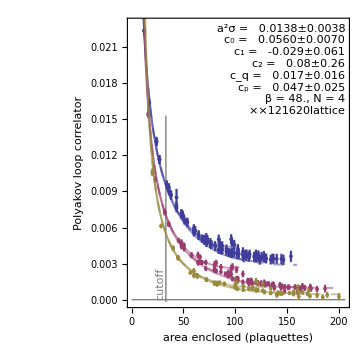

```mathematica
Print["Teper string tension:  ",tt2=teperTension[nd,nc,1,beta,avgP]^2];Print["Phase transition:  ",Pi/3*1/Sqrt[tt2]," links"];polyCorr=plotStringModelFit[If[True,polyakovCorrelatorGrouped,polyakovCorrelatorMerged],"covarianceMatrix"->If[True,polyakovCorrelatorCovariance/Length[First[polyakovCorrelatorValues]],None],"stringTension"->If[True,Automatic,tt2[[1]]],"coulomb"->If[True,Automatic,0],"lowerCutoff"->33,"upperCutoff"->Infinity,"pointPotential"->False,"NambuGoto"->False,"eigenstate"->0,"order"->2,"offAxis"->1,"linearLCorrections"->False,BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5 figureWidth,AspectRatio->1]
```

For paper, use 16×20×24, “maxx”->150, AspectRatio->1, ImageSize→1.5 figureWidth

```mathematica
Export["polycorr16.pdf",polyCorr]
```

polycorr16.pdf

### Analyze

Look at autocorrelations of eigenoperators of the correlation matrix (that is, Polyakov loop correlators dotted with eigenvectors of the correlation matrix) to verify that the monte carlo samples are far enough apart.

```mathematica
Dimensions[pp=If[False,(* All eigenvectors *)Eigenvectors[polyakovCorrelatorCovariance],(* Select eigenvectors for smallest/largest eigenvalues *)Map[Last,Take[Sort[Transpose[Eigensystem[polyakovCorrelatorCovariance]],NumericalOrder[First[#1],First[#2]]&],-10]]].Values[polyakovCorrelatorValues]]
```

{10,500}

```mathematica
ListPlot[Map[Transpose[{Range[0,10],CorrelationFunction[#,{10}]}]&,pp],Axes->True,Frame->True,PlotRange->All,AspectRatio->1,Joined->False]
```

```mathematica
TableForm[MapThread[{#1,valueError[Mean[#2],StandardDeviation[#2]/Sqrt[Length[#2]]],StandardDeviation[#2]}&,{Range[0,10],Transpose[Map[CorrelationFunction[#,{10}]&,pp]]}]]
```

0 |   0.999999999999999778±0.000000000000000042 | 1.33432×10^-16
1 |   0.005±0.018 | 0.056856
2 |   -0.01±0.014 | 0.0436926
3 |   0.005±0.014 | 0.0455655
4 |   0.003±0.018 | 0.0557479
5 |   0.009±0.016 | 0.0510941
6 |   0.014±0.019 | 0.0590804
7 |   0.004±0.013 | 0.0417974
8 |   -0.026±0.016 | 0.0509831
9 |   -0.028±0.012 | 0.0387141
10 |   0.029±0.014 | 0.0432834

Aggregate values for model parameters.  First, select cases where there was a decent fit (first two parameters are positive and significant):

```mathematica
Length[significantFits=Select[stringModelValuesPotential,(Head[#]===List&&Abs[#[[1,1]]]<1&&Abs[#[[2,1]]]<0.2&&#[[1,1]]> #[[1,2]]&&#[[2,1]]>#[[2,2]])&]]
```

196

```mathematica
Histogram[Map[#[[-1,1]]&,significantFits],25]
```

```mathematica
Map[{Mean[#],StandardDeviation[#],StandardDeviation[#]/Sqrt[Length[#]]}&,Drop[Transpose[significantFits],-1]]
```

{{  0.0709±0.0019,  0.0245±0.0040,  0.00175±0.00029},{  0.01120±0.00051,  0.0053±0.0010,  (3.8±0.73)×10^-4},{  0.02912±0.00049,  0.0048±0.0015,  (3.4±1.1)×10^-4},{  0.04253±0.00088,  0.0120±0.0017,  (8.6±1.2)×10^-4}}

Average model estimates for error of each parameter.  Compare with actual standard deviation of values above.

```mathematica
Map[Mean[Map[#[[2]]&,#]]&,Drop[Transpose[significantFits],-1]]
```

{0.0427282,0.0228688,0.0177332,0.0201495,0.0332988,0.0416118,0.0512425}

Evolution of the correlation matrix as lattice configurations are added.  This can take a while to calculate, you may want to skip some k-values.

```mathematica
covarianceEigenvalues=Table[Block[{dd=Map[Take[#,k]&,Values[polyakovCorrelatorValues]]},Map[{k,#}&,Chop[Sort[Eigenvalues[Outer[Covariance,dd,dd,1]]]]]],{k,2,Length[First[polyakovCorrelatorValues]],10}];
```

```mathematica
ListLogPlot[Transpose[covarianceEigenvalues],Joined->True,Axes->False,Frame->True,FrameLabel->{"number of configurations","covariance matrix eigenvalues"},AspectRatio->1,PlotStyle->{Thickness[0.0015]}]
```

Look at correlations.  The correlators have a significant blocked structure.  
We see for data sets with the largest number of configurations, the correlations in the off-diagonal blocks are mostly consistent with random fluctuations.

```mathematica
corr=Block[{data=Values[polyakovCorrelatorValues],cov,dd},
(* Construct full covariance matrix *)
cov=Outer[Covariance,data,data,1];dd=Sqrt[Diagonal[cov]];Map[#/dd&,cov]/dd];
```

```mathematica
MatrixPlot[corr]
```

Blocks, by hand, for 12×16×20 lattice

```mathematica
Block[{keys=Keys[polyakovCorrelatorValues]},k12=Select[Range[Length[keys]],keys[[#,-1]]==12&];k16=Select[Range[Length[keys]],keys[[#,-1]]==16&];k20=Select[Range[Length[keys]],keys[[#,-1]]==20&]]
```

{178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240}

```mathematica
Show[Histogram[{Flatten[{corr[[k12,k12]],corr[[k16,k16]],corr[[k20,k20]]}],Flatten[{corr[[k12,k16]],corr[[k12,k20]],corr[[k16,k20]]}]},{0.01},Axes->False,Frame->True,FrameLabel->{"correlation value","number of pairs"}],Plot[0.01*Length[Flatten[{corr[[k12,k16]],corr[[k12,k20]],corr[[k16,k20]]}]]*PDF[NormalDistribution[0,1/Sqrt[Length[First[polyakovCorrelatorValues]]]]][x],{x,-1,1},PlotRange->All]]
```

```mathematica
Show[Histogram[Map[Flatten,{corr[[k12,k12]],corr[[k16,k16]],corr[[k20,k20]],corr[[k12,k16]],corr[[k12,k20]],corr[[k16,k20]]}],{0.01},Axes->False,Frame->True,FrameLabel->{"correlation value","number of pairs"}],Plot[0.01*Map[Length,Map[Flatten,{corr[[k12,k16]],corr[[k12,k20]],corr[[k16,k20]]}]]*PDF[NormalDistribution[0,1/Sqrt[Length[First[polyakovCorrelatorValues]]]]][x],{x,-1,1},PlotRange->All]]
```

Determine which data points contribute the most to chi^2.

```mathematica
Print["Teper string tension:  ",tt2=teperTension[nd,nc,1,beta,avgP]^2];ff=stringModel[If[True,polyakovCorrelatorGrouped,polyakovCorrelatorMerged],"covarianceMatrix"->If[True,polyakovCorrelatorCovariance/Length[First[polyakovCorrelatorValues]],None],"stringTension"->If[False,Automatic,tt2[[1]]],"coulomb"->If[True,Automatic,0.02178],"offAxisTension"->False,"lowerCutoff"->0,"upperCutoff"->Infinity,"eigenstate"->0,"NambuGoto"->True,"order"->2,"offAxis"->2,"linearLCorrections"->False]
```

Teper string tension:    0.016195±0.000054

{243.914,{c_0→0.10949,c_1→-0.0190321,c_2→-0.551825,coff1→0.00448203,c_q→0.0140544,c_p→0.0428834}}

```mathematica
{err2,oo}=Block[{cov=polyakovCorrelatorCovariance/Length[First[polyakovCorrelatorValues]]},Eigensystem[cov[[ff["filter"],ff["filter"]]]]];
```

```mathematica
eigenweights=Block[{keys=Keys[polyakovCorrelatorGrouped][[ff["filter"]]]},Map[Take[Sort[Transpose[{#,keys}],NumericalOrder[Abs[First[#2]],Abs[First[#1]]]&],5]&,oo]]
```

{{{-0.108757,{{8,10},{8,10},{8,10},{8,10},{10,24},12}},{-0.107952,{{7,10},{7,10},{9,10},{9,10},{10,23},12}},{-0.107701,{{8,9},{8,9},{8,11},{8,11},{9,24},12}},{-0.107639,{{7,9},{9,9},{7,11},{9,11},{9,23},12}},{-0.106825,{{6,10},{6,10},{10,10},{10,10},{10,22},12}}},235,{{0.248055,{{4,7},{4,9},{7,16},{9,16},{4,23},12}},3,{-0.227107,{1}}}}
 |  |  |  |

```mathematica
TableForm[Take[Sort[Transpose[{oo.ff["FitResiduals"]/Sqrt[err2],eigenweights}],NumericalOrder[Abs[First[#2]],Abs[First[#1]]]&],5],TableDepth->3]
```

3.01536 | {0.301897,{{5,7},{5,9},{7,15},{9,15},{5,23},12}}
{-0.261113,{{1,4},{1,12},{4,19},{1,20},{4,21},12}}
{0.238018,{{1,3},{1,13},{1,19},{3,19},{3,21},12}}
{-0.231582,{{1,2},{1,14},{1,18},{2,19},{2,21},12}}
{-0.188563,{{4,6},{6,12},{4,14},{12,14},{6,20},12}}
2.89826 | {-0.336058,{{2,5},{2,7},{5,14},{7,14},{2,17},20}}
{-0.308313,{{4,5},{4,7},{5,12},{7,12},{4,17},20}}
{0.294486,{{4,6},{6,8},{4,10},{8,10},{6,16},20}}
{0.290467,{{3,4},{3,8},{4,13},{8,13},{3,16},20}}
{0.242089,{{3,3},{3,9},{3,13},{3,15},{9,13},20}}
-2.60438 | {0.248055,{{4,7},{4,9},{7,16},{9,16},{4,23},12}}
{-0.231044,{{4,6},{4,10},{6,16},{10,16},{4,22},12}}
{-0.228963,{{2,3},{3,14},{2,17},{3,18},{14,17},12}}
{-0.228579,{{5,7},{5,9},{7,15},{9,15},{5,23},12}}
{-0.227107,{{5,9},{5,11},{9,11},{11,11},{9,21},12}}
-2.49059 | {0.367639,{{3,8},{3,8},{8,9},{8,9},{8,15},20}}
{-0.361873,{{5,8},{5,8},{7,8},{7,8},{8,17},20}}
{0.270773,{{0,6},{0,10},{6,12},{6,12},{10,12},20}}
{0.231216,{{6,8},{6,8},{6,8},{6,8},{8,18},20}}
{0.217614,{{5,6},{5,6},{6,11},{6,11},{5,18},20}}
2.45253 | {-0.345751,{{3,10},{3,10},{9,10},{9,10},{10,15},16}}
{0.324276,{{6,10},{6,10},{6,10},{6,10},{10,18},16}}
{0.277764,{{0,7},{0,13},{7,12},{7,12},{12,13},16}}
{-0.234633,{{3,9},{3,11},{9,9},{9,11},{9,15},16}}
{0.220317,{{0,8},{0,12},{8,12},{8,12},{12,12},16}}

## Polyakov loop correlators

The best normalized overlap is for e^-alpha=0.72 and a very wide strip.  However, when fitting the string tension model, the lowest errors are obtained for  width=6 but seems to be unstable with respect to the width.  At most, we see factor of 5 improvement.

First, load base lattice configuration so lattice parameters (nc, nd, et cetera) are defined.  Also, define avgP for the Teper string tension.

```mathematica
<<"../data/3-3/periodic-12.16.20-28-5.m";avgP=averagePlaquette[]
```

0.902535

```mathematica
<<"../data/3-3/periodic-12.18.18-28-5.m";avgP=averagePlaquette[]
```

0.901545

```mathematica
<<"../data/3-3/periodic-14.18.22-28-2.m";N[avgP=averagePlaquette[],16]
```

0.901978

```mathematica
{averagePlaquette[1,2],averagePlaquette[1,3],averagePlaquette[2,3]}
```

{0.902228,0.9024,0.901304}

```mathematica
<<"../data/3-3/step-14.18.22-28-5-2a-8.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.979149

```mathematica
<<"../data/3-3/periodic-16-28-5.m";avgP=averagePlaquette[]
```

0.901792

```mathematica
<<"../data/3-3/step-16-28-5-2e-2.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.939903

```mathematica
<<"../data/3-3/periodic-16.20.24-28-5.m";avgP=averagePlaquette[]
```

0.901449

```mathematica
<<"../data/3-3/step-16.20.24-28-5-2a-20.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.997656

```mathematica
<<"../data/3-3/periodic-22-42-1.m";
```

```mathematica
<<"../data/3-3/step-22-42-1-a-1.m";gaugeField=gaugeField0;
```

```mathematica
<<"../data/3-3/step-22-42-1-b-1.m";gaugeField=gaugeField0;
```

```mathematica
<<"../data/3-3/step-22-42-1-c-1.m";gaugeField=gaugeField0;
```

```mathematica
<<"../data/3-4/periodic-16-48-1.m";avgP=averagePlaquette[]
```

0.892483

```mathematica
<<"../data/3-4/step-16-48-1-2d-1.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.995413

### Fit to string model, bare operator

```mathematica
tallyData=talliesToAverageErrors[polyakovCorrelatorTallies["simple","1"]];
```

Teper's published string tension (square to get string tension).

```mathematica
tt3=teperTension[nd,nc,beta,avgP]^2
```

0.016200±0.000054

```mathematica
plotStringModelFit[rescaleCorrelators[tallyData],"lowerCutoff"->0,"constantTerm"->True,ImageSize->1.5 figureWidth,AspectRatio->1,"stringTension"->If[True,Automatic,tt3[[1]]],"coulomb"->If[True,Automatic,0.02178]]
```

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.990974 | 0.295207 | 3.35688 | 0.000894247
a2sigma | 0.0512737 | 0.00388101 | 13.2114 | 1.78564×10^-31
cCoulomb | -0.0000147595 | 4.54084×10^-6 | -3.2504 | 0.00128915
c_p | 0.0153958 | 0.00933356 | 1.64951 | 0.100134
c_1 | 0.114777 | 0.0214481 | 5.35141 | 1.78345×10^-7

chi^2: 499.318 for 288 d.o.f.

16^3, one config, ELMC

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.472918 | 0.144232 | 3.27887 | 0.00216261
a2sigma | 0.0136277 | 0.0144575 | 0.942605 | 0.351542
cCoulomb | 0.00605552 | 0.00339348 | 1.78446 | 0.0819354
c_1 | -0.210825 | 0.441095 | -0.477959 | 0.635281

chi^2: 29.9146 for 40 d.o.f.

### Smeared operator

For a given strip width, find expAlpha which maximizes the normalized area=16*4 correlator.

First, the bare value :

```mathematica
aFirstCase[tallyData,{64,__,16}]/aFirstCase[tallyData,{0,__,16}]
```

0.095±0.019

```mathematica
f64[x_?NumericQ,w_]:=Block[{tallyData=talliesToAverageErrors[polyakovCorrelatorTallies["smeared",w,x,"1"]]},First[aFirstCase[tallyData,{64,__,16}]/aFirstCase[tallyData,{0,__,16}]]]
```

```mathematica
Table[Print["starting ", w];Prepend[FindMaximum[f64[x,w],{x,0.7,0.9},AccuracyGoal->4,PrecisionGoal->5],w],{w,10}]
```

{{1,0.151903,{x→1.31936}},{2,0.209218,{x→1.11877}},{3,0.247387,{x→0.732739}},{4,0.305788,{x→0.926425}},{5,0.332342,{x→0.966697}},{6,0.358578,{x→0.890745}},{7,0.429969,{x→0.882798}},{8,0.417824,{x→0.826965}},{9,0.438329,{x→0.743351}},{10,0.45025,{x→0.710113}}}

Best values from running f64 on “../data/3-3/periodic-16-28-1.m”

```mathematica
bestExpAlpha={{1,0.15190334055188978,{x->1.3193603200655564}},{2,0.20921767898547997,{x->1.1187715340205862}},{3,0.24738680315759534,{x->0.7327391957708174}},{4,0.3057877542190757,{x->0.9264246084921876}},{5,0.33234187740591387,{x->0.9666974172054921}},{6,0.3585779060781094,{x->0.8907445024069022}},{7,0.42996916748854713,{x->0.8827981291665957}},{8,0.41782410539015485,{x->0.8269652208638507}},{9,0.43832890854916007,{x->0.7433511108290587}},{10,0.4502500299532493,{x->0.7101127124296874}}};
```

Conclusion :  the widest strips  give the best overlap.

However, we want to measure the string tension for a single lattice configuration.  The string tension using the bare Polyakov loop correlator is:

```mathematica
Block[{tallyData=rescaleCorrelators[talliesToAverageErrors[polyakovCorrelatorTallies["simple","1"]]]},stringModel[tallyData,printResult->True,"lowerCutoff"->0,"constantTerm"->True]["ParameterTStatistics"]⟦2⟧]
```

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 2.24634 | 0.188331 | 11.9276 | 6.36002×10^-27
a2sigma | 0.0154727 | 0.000580484 | 26.6549 | 9.83297×10^-80
cCoulomb | 0.0180077 | 0.00125218 | 14.3811 | 1.02787×10^-35
c_p | 0.0159018 | 0.00240194 | 6.62038 | 1.74929×10^-10
c_1 | -0.0999632 | 0.00554362 | -18.0321 | 3.55126×10^-49

chi^2: 4712.46 for 288 d.o.f.

26.6549

Find a fit to the string tension model using the best value for expAlpha for each strip width.

```mathematica
fs[x_?NumericQ,w_]:=Block[{tallyData=rescaleCorrelators[talliesToAverageErrors[polyakovCorrelatorTallies["smeared",w,x,"1"]]]},stringModel[tallyData,printResult->True,"lowerCutoff"->0,"constantTerm"->True]["ParameterTStatistics"]⟦2⟧]
```

```mathematica
Map[{#[[1]],#[[3]],fs[#[[3,1,2]],#[[1]]]}&,bestExpAlpha]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.296991 | 0.0306385 | 9.69339 | 1.30125×10^-18
a^2σ | 0.00809512 | 0.000304979 | 26.5432 | 3.54974×10^-69
c_q | 0.00864342 | 0.00205334 | 4.20945 | 0.0000378824
c_p | 0.0340409 | 0.0074691 | 4.55757 | 8.75717×10^-6
c_1 | -0.386042 | 0.0625628 | -6.17048 | 3.43145×10^-9

chi^2: 401.565 for 211 d.o.f.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.495581 | 0.0733112 | 6.75997 | 5.71367×10^-10
a^2σ | 0.0102049 | 0.00072442 | 14.0871 | 5.85121×10^-27
c_q | 0.00206621 | 0.00219677 | 0.940566 | 0.348865
c_p | 0.0216559 | 0.0109322 | 1.98093 | 0.0499452
c_1 | -0.581852 | 0.100706 | -5.77773 | 6.37781×10^-8

chi^2: 142.86 for 117 d.o.f.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.370659 | 0.0680891 | 5.44373 | 2.6804×10^-7
a^2σ | 0.00828412 | 0.000679166 | 12.1975 | 5.68889×10^-23
c_q | 0.00790586 | 0.0036467 | 2.16795 | 0.0320725
c_p | 0.0386623 | 0.0127739 | 3.02667 | 0.00300769
c_1 | -0.563422 | 0.157739 | -3.57186 | 0.000505518

chi^2: 280.588 for 124 d.o.f.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.885154 | 0.241557 | 3.66437 | 0.000482561
a^2σ | 0.0125542 | 0.000858897 | 14.6167 | 8.16791×10^-23
c_q | -4.70097×10^-13 | 0.0000552137 | -8.51413×10^-9 | 1
c_p | 0.00041994 | 0.0197362 | 0.0212776 | 0.983086
c_1 | -0.572606 | 0.315763 | -1.8134 | 0.0741187

chi^2: 78.1891 for 69 d.o.f.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.521935 | 0.0856963 | 6.09052 | 2.50978×10^-8
a^2σ | 0.00976275 | 0.000914613 | 10.6742 | 7.76816×10^-18
c_q | 0.00117192 | 0.00279361 | 0.419501 | 0.675817
c_p | 0.0327261 | 0.0104402 | 3.13461 | 0.0023029
c_1 | -0.894728 | 0.173764 | -5.14911 | 1.4565×10^-6

chi^2: 121.045 for 93 d.o.f.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.460073 | 0.0815681 | 5.64035 | 3.02913×10^-7
a^2σ | 0.00916548 | 0.000860328 | 10.6535 | 1.60249×10^-16
c_q | 0.00148709 | 0.00315152 | 0.471864 | 0.638431
c_p | 0.0472308 | 0.0101617 | 4.64794 | 0.0000145344
c_1 | -1.12286 | 0.291474 | -3.85236 | 0.000249091

chi^2: 89.5124 for 73 d.o.f.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.589501 | 0.132169 | 4.46021 | 0.0000309854
a^2σ | 0.00997924 | 0.00121375 | 8.22182 | 7.85401×10^-12
c_q | 0.00306725 | 0.00372535 | 0.823344 | 0.413149
c_p | 0.0304679 | 0.0154784 | 1.96841 | 0.0530403
c_1 | -0.809577 | 0.224661 | -3.60355 | 0.000588032

chi^2: 58.7989 for 69 d.o.f.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.378822 | 0.0888596 | 4.26315 | 0.000071129
a^2σ | 0.00861841 | 0.000882837 | 9.76217 | 4.44053×10^-14
c_q | 0.00236044 | 0.00363884 | 0.648678 | 0.518981
c_p | 0.0649345 | 0.0084865 | 7.65151 | 1.75142×10^-10
c_1 | -1.29486 | 0.367573 | -3.52272 | 0.000815679

chi^2: 58.5885 for 61 d.o.f.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.377779 | 0.0678426 | 5.56846 | 4.74282×10^-7
a^2σ | 0.00869118 | 0.0002718 | 31.9764 | 1.05644×10^-42
c_q | -2.00956×10^-18 | 0.000181865 | -1.10498×10^-14 | 1
c_p | 0.0674025 | 0.0102507 | 6.57539 | 8.18475×10^-9
c_1 | -1.56378 | 0.471689 | -3.31527 | 0.00147107

chi^2: 115.309 for 68 d.o.f.

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 2.86935 | 1.01833 | 2.81771 | 0.00651021
a^2σ | 0.0128514 | 0.000928633 | 13.8391 | 1.76976×10^-20
c_q | -0.0000985434 | 0.0000422142 | -2.33436 | 0.0228859
c_p | -0.0802735 | 0.0269636 | -2.97711 | 0.00416886
c_1 | 1.42599 | 0.322556 | 4.42089 | 0.0000411246

chi^2: 165.209 for 61 d.o.f.

{{1,{x→1.31936},26.5432},{2,{x→1.11877},14.0871},{3,{x→0.732739},12.1975},{4,{x→0.926425},14.6167},{5,{x→0.966697},10.6742},{6,{x→0.890745},10.6535},{7,{x→0.882798},8.22182},{8,{x→0.826965},9.76217},{9,{x→0.743351},31.9764},{10,{x→0.710113},13.8391}}

## k-string mixing

First, load base lattice configuration so lattice parameters (nc, nd, et cetera) are defined.
Hard to say anything decisive about this analysis:  There seems to be a large overlap between 2S and 2A and 1 states for Teper/everyone else’s basis states.  Errors are much smaller with saddle-point configuration fields.

```mathematica
<<"../data/3-4/periodic-16-48-1.m";avgP=averagePlaquette[]
```

0.892483

```mathematica
<<"../data/3-4/step-16-48-1-2f-20.m";gaugeField=gaugeField0;averagePlaquette[]
```

0.997131

### Teper and everyone else basis

Generally, smeared results are closer to the Teper published values.

```mathematica
tallyData["simple","1"]=talliesToAverageErrors[polyakovLoopTallies["simple","1"]]
```

<|16→{0.0593821,0.00172371},32→{0.0413706,0.00152362},48→{0.025274,0.00141223},64→{0.0159221,0.00139513},80→{0.00843482,0.000773582},96→{0.00943692,0.00146025},112→{0.00740579,0.00148853},128→{0.00640343,0.00212143},16 √2→{0.0521308,0.00163297},16 √5→{0.0366396,0.00104603},16 √10→{0.0226358,0.000986753},16 √17→{0.0143811,0.000978804},16 √26→{0.0104855,0.000996463},16 √37→{0.00815591,0.0010214},80 √2→{0.00413284,0.000811866},16 √65→{0.00114986,0.000806938},32 √2→{0.0262901,0.00140385},16 √13→{0.0167247,0.000963092},32 √5→{0.0107306,0.000954787},16 √29→{0.00739953,0.000963438},32 √10→{0.00509919,0.00098656},16 √53→{0.00317685,0.00100915},32 √17→{0.00233855,0.00143634},48 √2→{0.0109289,0.00132349},16 √34→{0.00403673,0.00091408},48 √5→{0.00200085,0.000939637},16 √58→{0.000406426,0.000969641},16 √73→{-0.000254961,0.0013889},64 √2→{0.00371491,0.00124451},16 √41→{0.00158464,0.000880982},32 √13→{0.000111271,0.000915978},64 √5→{-0.0012816,0.00137629},16 √61→{-0.000418534,0.000932501},16 √74→{-0.000644838,0.000977295},16 √89→{-0.000675338,0.00140936},96 √2→{-0.000087712,0.00137863},16 √85→{0.000470169,0.00101147},160→{0.000830729,0.00145256},112 √2→{0.00183936,0.00146569},16 √113→{0.00246989,0.001478},128 √2→{0.00323989,0.00296551}|>

```mathematica
tallyData["simple","2S"]=talliesToAverageErrors[polyakovLoopTallies["simple","2S"]]
```

<|16→{0.00819167,0.000336525},32→{0.00352618,0.000239794},48→{0.00101086,0.000198261},64→{0.0000179148,0.000194634},80→{-0.000408369,0.000128523},96→{-0.000113657,0.000201412},112→{0.000471065,0.000211026},128→{0.000793867,0.000311164},16 √2→{0.00600861,0.000291878},16 √5→{0.00264247,0.00016444},16 √10→{0.000741718,0.000142819},16 √17→{-0.0000863023,0.000143462},16 √26→{-0.000374748,0.000150509},16 √37→{-0.000203951,0.000149804},80 √2→{0.0000161846,0.000124407},16 √65→{-0.000095773,0.000123279},32 √2→{0.00120878,0.000222074},16 √13→{0.000280411,0.000152022},32 √5→{-0.000264115,0.000157704},16 √29→{-0.000457506,0.00016097},32 √10→{-0.000330018,0.000158542},16 √53→{-0.0000792331,0.000152426},32 √17→{0.000020365,0.000209646},48 √2→{-0.00013515,0.000228258},16 √34→{-0.000536052,0.000159506},48 √5→{-0.000425573,0.000157566},16 √58→{-0.000333273,0.000154894},16 √73→{-0.000275135,0.000215133},64 √2→{-0.000590971,0.000223756},16 √41→{-0.000549083,0.00015398},32 √13→{-0.000438906,0.000153673},64 √5→{-0.000359176,0.000209777},16 √61→{-0.000268738,0.000155198},16 √74→{-0.000114354,0.000149566},16 √89→{-0.0000505758,0.000204954},96 √2→{0.000101249,0.000226015},16 √85→{0.0003947,0.000153916},160→{0.00052051,0.000207105},112 √2→{0.000881171,0.000216286},16 √113→{0.00106762,0.00021333},128 √2→{0.00125632,0.000438491}|>

```mathematica
tallyData["simple","2A"]=talliesToAverageErrors[polyakovLoopTallies["simple","2A"]]
```

<|16→{0.0311175,0.00117547},32→{0.0208021,0.0010181},48→{0.0131727,0.000958544},64→{0.0100248,0.000968501},80→{0.00789795,0.000559049},96→{0.00913703,0.000987931},112→{0.0091028,0.000968316},128→{0.0090956,0.00136068},16 √2→{0.0269198,0.00110492},16 √5→{0.0185576,0.000703017},16 √10→{0.0122672,0.000677148},16 √17→{0.00957937,0.000682797},16 √26→{0.00891241,0.000692561},16 √37→{0.00890174,0.000688433},80 √2→{0.00808124,0.000545766},16 √65→{0.00890055,0.000543503},32 √2→{0.0139537,0.000960482},16 √13→{0.0103224,0.000678198},32 √5→{0.0085183,0.000681411},16 √29→{0.00801137,0.000676222},32 √10→{0.00828267,0.000667185},16 √53→{0.00883348,0.000654288},32 √17→{0.00907132,0.000917446},48 √2→{0.00840524,0.000965475},16 √34→{0.00697689,0.000654884},48 √5→{0.00769019,0.000643068},16 √58→{0.00878746,0.000640134},16 √73→{0.00929377,0.00090834},64 √2→{0.00627205,0.000932263},16 √41→{0.00623084,0.00064204},32 √13→{0.0073414,0.000646341},64 √5→{0.00953365,0.000951865},16 √61→{0.00729217,0.000678201},16 √74→{0.00872291,0.000702086},16 √89→{0.00939593,0.00100968},96 √2→{0.00779409,0.00099693},16 √85→{0.00869721,0.000712545},160→{0.00913964,0.00101071},112 √2→{0.00891503,0.000985526},16 √113→{0.00905851,0.000973336},128 √2→{0.00912281,0.00190395}|>

```mathematica
tallyData["simple","2S","1"]=talliesToAverageErrors[polyakovLoopTallies["simple",{"2S","1"}]]
```

<|16→{0.00861641+0.00362256 ⅈ,0.000537257+0.000368474 ⅈ},32→{0.00599955+0.00204301 ⅈ,0.000447103+0.000352252 ⅈ},48→{0.00372811+0.000805383 ⅈ,0.000397621+0.000343272 ⅈ},64→{0.00245605+0.000329897 ⅈ,0.000386005+0.000337172 ⅈ},80→{0.00100321-0.000590914 ⅈ,0.000224329+0.000197779 ⅈ},96→{0.00177466+0.000565516 ⅈ,0.000395584+0.000327002 ⅈ},112→{0.00145994+0.000798531 ⅈ,0.000389844+0.000333728 ⅈ},128→{0.00131978+0.000843266 ⅈ,0.000546945+0.000477666 ⅈ},16 √2→{0.00755795+0.00294316 ⅈ,0.000497302+0.000361016 ⅈ},16 √5→{0.00532246+0.00153527 ⅈ,0.000302133+0.000246385 ⅈ},16 √10→{0.00333388+0.000430474 ⅈ,0.000276786+0.000241435 ⅈ},16 √17→{0.00216414+0.0000238784 ⅈ,0.000273905+0.000238431 ⅈ},16 √26→{0.00167936+0.000088693 ⅈ,0.000279242+0.000232984 ⅈ},16 √37→{0.00136987+0.000335883 ⅈ,0.000280771+0.000232442 ⅈ},80 √2→{0.000570407-0.0000140974 ⅈ,0.000222757+0.000195243 ⅈ},16 √65→{0.000225094-0.000013731 ⅈ,0.000223816+0.000194457 ⅈ},32 √2→{0.0038139+0.000473197 ⅈ,0.000395333+0.00034256 ⅈ},16 √13→{0.00236105-0.000324709 ⅈ,0.000271642+0.000242601 ⅈ},32 √5→{0.00140439-0.000557757 ⅈ,0.000274669+0.000241176 ⅈ},16 √29→{0.000885265-0.000407584 ⅈ,0.00028028+0.000236472 ⅈ},32 √10→{0.000540803-0.000127574 ⅈ,0.000283+0.000236506 ⅈ},16 √53→{0.000307561+0.00012355 ⅈ,0.000282585+0.000239049 ⅈ},32 √17→{0.000218974+0.0001919 ⅈ,0.000398188+0.000338863 ⅈ},48 √2→{0.00129785-0.000901171 ⅈ,0.00038517+0.000349514 ⅈ},16 √34→{0.0000725229-0.000876915 ⅈ,0.000273177+0.000243086 ⅈ},48 √5→{-0.000131789-0.000538309 ⅈ,0.000277576+0.000242472 ⅈ},16 √58→{-0.000169325-0.000187605 ⅈ,0.000282201+0.000239939 ⅈ},16 √73→{-0.000151392-0.0000277477 ⅈ,0.000401282+0.000334666 ⅈ},64 √2→{-0.000175062-0.00128045 ⅈ,0.000378328+0.00034872 ⅈ},16 √41→{-0.000406096-0.00118066 ⅈ,0.000264014+0.000244809 ⅈ},32 √13→{-0.000333063-0.000791786 ⅈ,0.000267125+0.00024345 ⅈ},64 √5→{-9.7316×10^-6-0.000114251 ⅈ,0.000390387+0.00033021 ⅈ},16 √61→{-0.000017259-0.000744054 ⅈ,0.000267138+0.000238478 ⅈ},16 √74→{0.000437806-0.000295795 ⅈ,0.000270181+0.000234337 ⅈ},16 √89→{0.000647169-0.0000799061 ⅈ,0.000383553+0.000329232 ⅈ},96 √2→{0.000611645-0.000412858 ⅈ,0.000383082+0.000331471 ⅈ},16 √85→{0.00120933-0.0000444053 ⅈ,0.000270571+0.000234135 ⅈ},160→{0.00146734+0.000161344 ⅈ,0.000381885+0.000330941 ⅈ},112 √2→{0.00179409+0.000224378 ⅈ,0.000381022+0.000332156 ⅈ},16 √113→{0.00201413+0.000385458 ⅈ,0.000380929+0.000331378 ⅈ},128 √2→{0.00220439+0.000496522 ⅈ,0.000759459+0.000660253 ⅈ}|>

```mathematica
tallyData["simple","2A","1"]=talliesToAverageErrors[polyakovLoopTallies["simple",{"2A","1"}]]
```

<|16→{0.012579+0.0026674 ⅈ,0.00106022+0.000549048 ⅈ},32→{0.00939528+0.00154965 ⅈ,0.000911689+0.0005107 ⅈ},48→{0.00652252+0.00090223 ⅈ,0.000814158+0.000516178 ⅈ},64→{0.00478949+0.000554245 ⅈ,0.00077947+0.000529857 ⅈ},80→{0.0031267-0.000292061 ⅈ,0.000432404+0.000316866 ⅈ},96→{0.00232889-0.00134831 ⅈ,0.000799588+0.000528784 ⅈ},112→{0.000873667-0.00270083 ⅈ,0.000802586+0.000521039 ⅈ},128→{0.000177611-0.0032979 ⅈ,0.00113415+0.000733722 ⅈ},16 √2→{0.0113007+0.00219106 ⅈ,0.000995842+0.000525605 ⅈ},16 √5→{0.0086175+0.00142901 ⅈ,0.000620393+0.000356279 ⅈ},16 √10→{0.00614755+0.000965251 ⅈ,0.000566372+0.000364113 ⅈ},16 √17→{0.00452863+0.000566857 ⅈ,0.000546703+0.000373907 ⅈ},16 √26→{0.00336116-0.000197613 ⅈ,0.000549919+0.000375679 ⅈ},16 √37→{0.00200335-0.00141478 ⅈ,0.000558192+0.000374301 ⅈ},80 √2→{0.0003899-0.00258893 ⅈ,0.000442786+0.000310201 ⅈ},16 √65→{-0.000700948-0.00240673 ⅈ,0.000442512+0.000306155 ⅈ},32 √2→{0.00690465+0.00121369 ⅈ,0.000813749+0.000504717 ⅈ},16 √13→{0.00520178+0.000919023 ⅈ,0.000547286+0.000369709 ⅈ},32 √5→{0.00382422+0.000354782 ⅈ,0.000534397+0.000380599 ⅈ},16 √29→{0.00259096-0.000546287 ⅈ,0.000534608+0.000378171 ⅈ},32 √10→{0.00122853-0.00162354 ⅈ,0.000541142+0.000373856 ⅈ},16 √53→{-0.0000914957-0.00257047 ⅈ,0.000545168+0.000374498 ⅈ},32 √17→{-0.000666043-0.00296785 ⅈ,0.000772179+0.000530814 ⅈ},48 √2→{0.00405243+0.000443238 ⅈ,0.000748846+0.000542724 ⅈ},16 √34→{0.00166086-0.00129287 ⅈ,0.000510656+0.00038761 ⅈ},48 √5→{0.000392782-0.00196892 ⅈ,0.000517931+0.000377775 ⅈ},16 √58→{-0.000678298-0.00236243 ⅈ,0.000529229+0.000374054 ⅈ},16 √73→{-0.00113079-0.00250595 ⅈ,0.000755664+0.000529513 ⅈ},64 √2→{0.00182621-0.00133686 ⅈ,0.000705036+0.000567979 ⅈ},16 √41→{0.000809114-0.00207042 ⅈ,0.000494255+0.00039709 ⅈ},32 √13→{-0.000191913-0.00221818 ⅈ,0.000509546+0.000385502 ⅈ},64 √5→{-0.00131914-0.00187398 ⅈ,0.000767478+0.000529077 ⅈ},16 √61→{-0.000728752-0.0020996 ⅈ,0.000525869+0.000387105 ⅈ},16 √74→{-0.00133882-0.00153164 ⅈ,0.00055072+0.000377818 ⅈ},16 √89→{-0.00155325-0.00126038 ⅈ,0.000795435+0.000529109 ⅈ},96 √2→{-0.00131149-0.00158614 ⅈ,0.000772326+0.000542271 ⅈ},16 √85→{-0.00181694-0.000975195 ⅈ,0.000557702+0.000376277 ⅈ},160→{-0.00199094-0.000694263 ⅈ,0.000796703+0.000526884 ⅈ},112 √2→{-0.00225328-0.000536689 ⅈ,0.000775772+0.000527462 ⅈ},16 √113→{-0.00243371-0.0003486 ⅈ,0.000768568+0.000524751 ⅈ},128 √2→{-0.00259241-0.000208294 ⅈ,0.00149648+0.00105335 ⅈ}|>

```mathematica
tallyData["simple","2S","2A"]=talliesToAverageErrors[polyakovLoopTallies["simple",{"2S","2A"}]]
```

<|16→{0.000181488+0.000560447 ⅈ,0.000432364+0.000244922 ⅈ},32→{-0.000314023+0.000493635 ⅈ,0.00033558+0.000256321 ⅈ},48→{-0.00028534+0.000627761 ⅈ,0.000292045+0.00025146 ⅈ},64→{0.000191286+0.000920954 ⅈ,0.000288957+0.000243313 ⅈ},80→{-0.000356692+0.000812205 ⅈ,0.000174591+0.00013948 ⅈ},96→{0.000947068+0.00140943 ⅈ,0.000294941+0.000250417 ⅈ},112→{0.000868867+0.00152048 ⅈ,0.000288103+0.000259423 ⅈ},128→{0.000819157+0.00155572 ⅈ,0.000406933+0.000367812 ⅈ},16 √2→{-0.0000971659+0.000483558 ⅈ,0.000391583+0.000249789 ⅈ},16 √5→{-0.000462916+0.000429157 ⅈ,0.000228937+0.000177388 ⅈ},16 √10→{-0.000390624+0.000513554 ⅈ,0.000208424+0.00017302 ⅈ},16 √17→{0.0000741815+0.000779099 ⅈ,0.000207209+0.000169555 ⅈ},16 √26→{0.000577227+0.00110261 ⅈ,0.000211222+0.000169255 ⅈ},16 √37→{0.000765546+0.00138405 ⅈ,0.000207582+0.000176082 ⅈ},80 √2→{0.000126421+0.00136751 ⅈ,0.000164235+0.000147751 ⅈ},16 √65→{0.0000160569+0.00132441 ⅈ,0.000163402+0.000144308 ⅈ},32 √2→{-0.000670628+0.000341366 ⅈ,0.000304199+0.000241966 ⅈ},16 √13→{-0.000645799+0.000389403 ⅈ,0.000212218+0.000168101 ⅈ},32 √5→{-0.00033077+0.000607729 ⅈ,0.000213601+0.000166751 ⅈ},16 √29→{0.0000286231+0.000958295 ⅈ,0.000211956+0.00016787 ⅈ},32 √10→{0.000208886+0.00130963 ⅈ,0.000207261+0.000173105 ⅈ},16 √53→{0.000198904+0.00143412 ⅈ,0.000199428+0.000182182 ⅈ},32 √17→{0.000160807+0.00141836 ⅈ,0.000276542+0.000262759 ⅈ},48 √2→{-0.000883093+0.000437413 ⅈ,0.000308004+0.000239287 ⅈ},16 √34→{-0.000703705+0.000929371 ⅈ,0.000205119+0.000171785 ⅈ},48 √5→{-0.000435276+0.00122152 ⅈ,0.000200579+0.000174565 ⅈ},16 √58→{-0.000226157+0.00130658 ⅈ,0.000197067+0.000179319 ⅈ},16 √73→{-0.000156006+0.00127563 ⅈ,0.00027786+0.000255114 ⅈ},64 √2→{-0.00126322+0.000758376 ⅈ,0.000290861+0.000248337 ⅈ},16 √41→{-0.00112368+0.00097041 ⅈ,0.000197001+0.000177145 ⅈ},32 √13→{-0.00070197+0.00115695 ⅈ,0.00019791+0.000174904 ⅈ},64 √5→{-0.000101567+0.00119366 ⅈ,0.000287035+0.000240095 ⅈ},16 √61→{-0.000507744+0.00120983 ⅈ,0.000209155+0.000169548 ⅈ},16 √74→{-0.0000611667+0.00129151 ⅈ,0.000212081+0.000164057 ⅈ},16 √89→{0.000122554+0.00132568 ⅈ,0.000299927+0.000228747 ⅈ},96 √2→{-0.000139983+0.00134286 ⅈ,0.000309329+0.000228672 ⅈ},16 √85→{0.000122045+0.00143121 ⅈ,0.000214421+0.000159136 ⅈ},160→{0.000221439+0.00147057 ⅈ,0.000296117+0.000225911 ⅈ},112 √2→{0.000151648+0.00147959 ⅈ,0.000286739+0.000224156 ⅈ},16 √113→{0.000139668+0.00149118 ⅈ,0.000276071+0.000225625 ⅈ},128 √2→{0.0000607456+0.00146711 ⅈ,0.000525454+0.00045133 ⅈ}|>

```mathematica
tallyData["smeared","1"]=talliesToAverageErrors[polyakovLoopTallies["smeared","1"]]
```

<|16→{0.0378101,0.00318578},32→{0.0230729,0.00269423},48→{0.011672,0.00252387},64→{0.0064734,0.00240587},80→{0.00556264,0.00226747},96→{0.00633223,0.00219644},112→{0.00673761,0.00207564},128→{0.00667994,0.00281506}|>

```mathematica
tallyData["smeared","2S"]=talliesToAverageErrors[polyakovLoopTallies["smeared","2S"]]
```

<|16→{0.00447584,0.000474965},32→{0.00177576,0.000345797},48→{0.000837792,0.000343516},64→{0.000372545,0.000331913},80→{-0.000108647,0.000321758},96→{-0.000232114,0.000343115},112→{-0.0000594145,0.000336699},128→{0.0000773614,0.000465135}|>

```mathematica
tallyData["smeared","2A"]=talliesToAverageErrors[polyakovLoopTallies["smeared","2A"]]
```

<|16→{0.0179296,0.00174535},32→{0.0106356,0.00153031},48→{0.00565391,0.00148502},64→{0.00378364,0.00148938},80→{0.00315367,0.00152345},96→{0.00240071,0.00153244},112→{0.00136469,0.00147585},128→{0.000819197,0.00203284}|>

```mathematica
tallyData["smeared","2S","1"]=talliesToAverageErrors[polyakovLoopTallies["smeared",{"2S","1"}]]
```

<|16→{0.00448781+0.00323701 ⅈ,0.000923706+0.000599216 ⅈ},32→{0.00262481+0.00196363 ⅈ,0.000721475+0.000610492 ⅈ},48→{0.00178163+0.00102742 ⅈ,0.000634709+0.000609658 ⅈ},64→{0.00173074+0.000259271 ⅈ,0.000612642+0.000565928 ⅈ},80→{0.00178465-0.000589888 ⅈ,0.000644754+0.000508552 ⅈ},96→{0.00197138-0.00125511 ⅈ,0.000659131+0.000505052 ⅈ},112→{0.00243167-0.00160947 ⅈ,0.000643385+0.000513706 ⅈ},128→{0.00272489-0.00173404 ⅈ,0.000900337+0.000730206 ⅈ}|>

```mathematica
tallyData["smeared","2A","1"]=talliesToAverageErrors[polyakovLoopTallies["smeared",{"2A","1"}]]
```

<|16→{0.0108438+0.0000812297 ⅈ,0.00170329+0.000916954 ⅈ},32→{0.00715851-0.000308886 ⅈ,0.00143142+0.000917418 ⅈ},48→{0.00381028-0.000239334 ⅈ,0.00130858+0.000945645 ⅈ},64→{0.00142248+0.000366578 ⅈ,0.00128687+0.000910609 ⅈ},80→{-0.0000591215+0.00103817 ⅈ,0.0013114+0.000856219 ⅈ},96→{-0.00123491+0.00144384 ⅈ,0.00130069+0.000859948 ⅈ},112→{-0.00268772+0.00173033 ⅈ,0.00119258+0.000899814 ⅈ},128→{-0.0034934+0.00186302 ⅈ,0.0015783+0.00129857 ⅈ}|>

```mathematica
tallyData["smeared","2S","2A"]=talliesToAverageErrors[polyakovLoopTallies["smeared",{"2S","2A"}]]
```

<|16→{-0.0024574+0.00134232 ⅈ,0.00068109+0.000399925 ⅈ},32→{-0.0021133+0.00113596 ⅈ,0.000508652+0.000391385 ⅈ},48→{-0.00161653+0.000797214 ⅈ,0.000462237+0.00036501 ⅈ},64→{-0.000977776+0.000300707 ⅈ,0.000463176+0.000339324 ⅈ},80→{-0.000363973-0.00014073 ⅈ,0.000488395+0.00035093 ⅈ},96→{-0.0000709944-0.000311397 ⅈ,0.000508121+0.000363835 ⅈ},112→{-0.000114191-0.000432984 ⅈ,0.000496227+0.000337472 ⅈ},128→{-0.000189632-0.000516943 ⅈ,0.000688018+0.000444174 ⅈ}|>

### Monomial basis

```mathematica
tallyData["smeared","t2"]=talliesToAverageErrors[polyakovLoopTallies["smeared","t2"]]
```

<|16→{0.0867462,0.00698644},32→{0.0508784,0.00657932},48→{0.0300814,0.00689936},64→{0.0181749,0.00691341},80→{0.00914651,0.00672928},96→{0.00448335,0.00695783},112→{0.00355564,0.00715813},128→{0.00374894,0.0101495}|>

```mathematica
tallyData["smeared","t1t1"]=talliesToAverageErrors[polyakovLoopTallies["smeared","t1t1"]]
```

<|16→{0.00311782,0.00069318},32→{0.00119868,0.000420463},48→{0.000364597,0.000304187},64→{0.000219267,0.000232946},80→{0.000230432,0.000194211},96→{0.000213652,0.000188369},112→{0.000115173,0.000155466},128→{0.0000565289,0.000194156}|>

```mathematica
tallyData["smeared","t2","t1t1"]=talliesToAverageErrors[polyakovLoopTallies["smeared",{"t2","t1t1"}]]
```

<|16→{-0.0030919+0.00251685 ⅈ,0.000678824+0.000686773 ⅈ},32→{-0.00320791+0.00212993 ⅈ,0.000747643+0.000630187 ⅈ},48→{-0.00187127+0.00149478 ⅈ,0.00078939+0.000599361 ⅈ},64→{-0.0015462+0.000563825 ⅈ,0.000872459+0.000547111 ⅈ},80→{-0.0019437-0.000263869 ⅈ,0.000983492+0.000582577 ⅈ},96→{-0.00171308-0.000583869 ⅈ,0.0010197+0.000628638 ⅈ},112→{-0.000860471-0.000811844 ⅈ,0.000966618+0.000604149 ⅈ},128→{-0.000339921-0.000969269 ⅈ,0.00131892+0.000788436 ⅈ}|>

```mathematica
tallyData["smeared","t2","1"]=talliesToAverageErrors[polyakovLoopTallies["smeared",{"t2","1"}]]
```

<|16→{-0.00504622+0.00797069 ⅈ,0.0023487+0.00232586 ⅈ},32→{-0.00417573+0.00537241 ⅈ,0.00251995+0.00229162 ⅈ},48→{-0.00126134+0.00292754 ⅈ,0.00257483+0.00220333 ⅈ},64→{0.00219312+0.0000983109 ⅈ,0.00272618+0.00212087 ⅈ},80→{0.00455031-0.00303198 ⅈ,0.00292447+0.00210373 ⅈ},96→{0.0067808-0.00530354 ⅈ,0.00297789+0.0021233 ⅈ},112→{0.0101108-0.00661917 ⅈ,0.00293691+0.00208221 ⅈ},128→{0.0120523-0.00712964 ⅈ,0.00412897+0.00287451 ⅈ}|>

```mathematica
tallyData["smeared","t1t1","1"]=talliesToAverageErrors[polyakovLoopTallies["smeared",{"t1t1","1"}]]
```

<|16→{0.00687132+0.0020536 ⅈ,0.00106666+0.000422955 ⅈ},32→{0.00432495+0.00111144 ⅈ,0.000765539+0.000446843 ⅈ},48→{0.00254237+0.000552385 ⅈ,0.000618043+0.00048833 ⅈ},64→{0.00161514+0.000299511 ⅈ,0.000542666+0.000449777 ⅈ},80→{0.00109324+0.0000206345 ⅈ,0.000523377+0.000362811 ⅈ},96→{0.000769021-0.000243004 ⅈ,0.000510878+0.000354246 ⅈ},112→{0.000511896-0.000357043 ⅈ,0.000429313+0.000403621 ⅈ},128→{0.000393033-0.000385143 ⅈ,0.000518041+0.000611884 ⅈ}|>

### Analysis

```mathematica
Format[a2sigma]=SequenceForm[Style[a,Italic]^2,σ];
Block[{reim=If[True,Re[#],Im[#]]&,nn,tallyData=tallyData["smeared","t2"],maxx,miny,maxy,ff},nn=Normal[Map[reim,tallyData]];ff=stringModel[Map[reim,tallyData],printResult->True];maxx=Max[Map[First,nn]]+0.5;maxy=Max[Map[#[[2,1]]+1.5 #[[2,2]]&,nn]];miny=Min[0,Min[Map[#[[2,1]]-1.5 #[[2,2]]&,nn]]];Show[ErrorListPlot[Map[{{#[[1]],#[[2,1]]},ErrorBar[#[[2,2]]]}&,nn],PlotRange->{{0,maxx},{miny,maxy}},Epilog->{Text[ColumnForm[Join[Map[Row[{#[[1,1]]," = ",printNumberError[#[[1,2]],#[[2]]]}]&,Transpose[ff[{"BestFitParameters","ParameterErrors"}]]],{Row[{"β = ",N[beta],", N_d = ",nd,", N_c = ",nc}],Row[{"lattice = ",Row[latticeDimensions,", "]}]}]],{maxx*0.9,maxy*0.9},{1,1}],Dashing[.02],Gray,Line[{{0,0},{maxx,0}}]},Axes->False,Frame->True,FrameLabel->{"area enclosed (plaquettes)","Polyakov loop correlator"}],Plot[ff[x],{x,0,maxx},PlotRange->All]]]
```

## Bulk Wilson loops

### Operator distribution example

```mathematica
wilsonLoopPhases=Merge[Table[Block[{gaugeField,gaugeSegments=Association[]},Get["../data/3-3/periodic-16-28-"<>ToString[i]<>".m"];wilsonLoopDistribution[5,5,"phases"]],{i,1,100}],Flatten[#,1]&];
```

```mathematica
wilsonLoop1All=Merge[Table[Block[{gaugeField,gaugeSegments=Association[]},Get["../data/3-3/periodic-16-28-"<>ToString[i]<>".m"];wilsonLoopDistribution[5,5,"1",True]],{i,1,100}],Flatten[#,1]&];
```

```mathematica
Block[{f="../cache/3-3/wilson-16-28.m"},DeleteFile[f];Save[f, {nc,wilsonLoopPhases,wilsonLoop1All}]]
```

```mathematica
<<"../cache/3-3/wilson-16-28.m";
```

```mathematica
polyDist1=plotPhases[wilsonLoopPhases,True,BaseStyle->journalStyle,ImageSize->1.0*figureWidth]
```

{{mean, stdev}, ...}: {{1.66603,0.447638},{-0.0006335,0.377088},{-1.6654,0.447407}}

{{0,1,2},{0,0,0},{{(2 π)/3,(2 π)/3,-(4 π)/3},{(4 π)/3,-(2 π)/3,-(2 π)/3}},{{1,0,-1},{-1/3,2/3,-1/3}}}

```mathematica
Export["polydist1.pdf",polyDist1[[1,2,1,1,1]]]
```

polydist1.pdf

```mathematica
Dimensions[wilsonLoop1]
```

{1228800}

```mathematica
polyDist2=plotDist[wilsonLoop1All,"1",True,BaseStyle->journalStyle,ImageSize->1.0*figureWidth]
```

{mean, Re stdev, Im stdev, count}: {0.255824,0.253828,0.150184,1228800}

```mathematica
Export["polydist2.pdf",polyDist2]
```

polydist2.pdf

### Expectation values

900 lattice configurations, all Wilson loop sizes.

```mathematica
<<"../data/3-3/periodic-12.16.20-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/wilson-triangle-12.16.20-28.m";
```

0.901917

400 lattice configurations, all Wilson loop sizes.

```mathematica
<<"../data/3-3/periodic-12.16.20-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/wilson-triangle-12.16.20-28-all.m";
```

0.901917

```mathematica
<<"../data/3-3/periodic-16.20.24-28-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-3/wilson-triangle-16.20.24-28.m";
```

0.901497

```mathematica
<<"../data/3-4/periodic-12.16.20-48-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-4/wilson-triangle-12.16.20-48.m";
```

0.891977

```mathematica
<<"../data/3-4/periodic-16-48-1.m";Print[avgP=averagePlaquette[]];<<"../cache/3-4/wilson-triangle-16-48.m";
```

0.892483

#### Calculate

Loop through lattice configurations, accumulating Wilson loop values.  For each configuration, use average value and estimate covariance matrix by aggregation over configurations.

Calculate new values and save :

```mathematica
bulkWilsonLoops["../data/3-3/periodic-12.16.20-28-","../cache/3-3/wilson-triangle-12.16.20-28.m","lower"->1,"upper"->900]
```

Finished aggregating data. tallyData memory:  11310584 in 6672.56529 s

Finished correlators in 0.47594s

Merged and grouped correlators, dump results 0.40382 s

```mathematica
bulkWilsonLoops["../data/3-3/periodic-12.16.20-28-","../cache/3-3/wilson-triangle-12.16.20-28-all.m","lower"->1,"upper"->400,"skip"->1,"lowerCutoff"->1]
```

Finished aggregating data. tallyData memory:  32411640 in 15554.88803 s

Finished correlators in 8.512948s

DeleteFile::fdnfnd: Directory or file ../data/3-3/wilson-triangle-12.16.20-28-all.m not found.

Merged and grouped correlators, dump results 1.6237 s

```mathematica
bulkWilsonLoops["../data/3-3/periodic-14.18.22-28-","../cache/3-3/wilson-triangle-14.18.22-28.m","lower"->1,"upper"->500]
```

Finished aggregating data. tallyData memory:  8777256 in 7382.935945 s

Finished correlators in 0.56691s

DeleteFile::fdnfnd: Directory or file ../data/3-3/wilson-triangle-14.18.22-28.m not found.

Merged and grouped correlators, dump results 0.41028 s

```mathematica
bulkWilsonLoops["../data/3-3/periodic-16-28-","../cache/3-3/wilson-triangle-16-28.m","lower"->1,"upper"->100]
```

Finished aggregating data. tallyData memory:  288296 in 847.555066 s

Finished correlators in 0.02976s

DeleteFile::fdnfnd: Directory or file ../data/3-3/wilson-triangle-16-28.m not found.

Merged and grouped correlators, dump results 0.01616 s

```mathematica
bulkWilsonLoops["../data/3-3/periodic-16.20.24-28-","../cache/3-3/wilson-triangle-16.20.24-28.m","lower"->1,"upper"->500]
```

Finished aggregating data. tallyData memory:  11551736 in 12898.744 s

Finished correlators in 0.990256s

DeleteFile::fdnfnd: Directory or file ../data/3-3/wilson-triangle-16.20.24-28.m not found.

Merged and grouped correlators, dump results 0.53009 s

```mathematica
bulkWilsonLoops["../data/3-3/periodic-20-28-","../cache/3-3/wilson-triangle-20-28.m","lower"->1,"upper"->100]
```

Finished aggregating data. tallyData memory:  494216 in 3033.21651 s

Finished correlators in 0.076555s

DeleteFile::fdnfnd: Directory or file ../data/3-3/wilson-triangle-20-28.m not found.

Merged and grouped correlators, dump results 0.02921 s

```mathematica
bulkWilsonLoops["../data/3-4/periodic-12.16.20-48-","../cache/3-4/wilson-triangle-12.16.20-48.m","lower"->1,"upper"->300]
```

Finished aggregating data. tallyData memory:  3827608 in 2672.61784 s

Finished correlators in 0.25903s

Merged and grouped correlators, dump results 0.19361 s

```mathematica
bulkWilsonLoops["../data/3-4/periodic-16-48-","../cache/3-4/wilson-triangle-16-48.m","upper"->100]
```

Finished aggregating data. tallyData memory:  288296 in 915.112286 s

Finished correlators in 0.03177s

Merged and grouped correlators, dump results 0.01381 s

#### Plot fit

String tension and Coulomb term are highly correlated.  Leaving out string tension gives very poor fit, while leaving out the Coulomb term gives a good fit.  Perhaps at this lattice spacing, there is no “Coulomb dominated region” between the string tension and the region where power law corrections are dominant.

```mathematica
Print["Teper string tension:  ",tt2=teperTension[nd,nc,1,beta,avgP]^2];plotWilsonModelFit[wilsonTriangleGrouped,True,"covarianceMatrix"->If[True,wilsonTriangleCovariance/Length[First[wilsonTriangleValues]],None],"lowerCutoff"->3,"upperCutoff"->1,"order"->3,"stringTension"->If[False,Automatic,tt2[[1]]],"coulomb"->If[True,Automatic,0*0.0222],"pointPotential"->False]
```

Teper string tension:    0.016195±0.000054

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

Correlation matrix: {{1.,-0.744952,0.711826,-0.156618,0.160581,-0.562588,0.974276},{-0.744952,1.,-0.905091,0.365784,0.322157,0.0955313,-0.610823},{0.711826,-0.905091,1.,-0.520409,-0.560275,0.135223,0.622637},{-0.156618,0.365784,-0.520409,1.,0.563436,-0.386573,-0.125102},{0.160581,0.322157,-0.560275,0.563436,1.,-0.888178,0.222276},{-0.562588,0.0955313,0.135223,-0.386573,-0.888178,1.,-0.604599},{0.974276,-0.610823,0.622637,-0.125102,0.222276,-0.604599,1.}}

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 1.50027 | 0.0302979 | 49.5174 | 0.
cCoulomb | -0.00656593 | 0.000617441 | -10.6341 | 0.
cPerimeter | 0.076612 | 0.00101874 | 75.203 | 0.
c1 | 0.189272 | 0.0108434 | 17.455 | 0.
c2 | -0.140974 | 0.0100019 | -14.0947 | 0.
c3 | 0.0392726 | 0.0224872 | 1.74645 | 0.0816365
c4 | 0.308899 | 0.0228845 | 13.4982 | 0.

chi^2: 474.906 for 340 d.o.f.

#### Analyze

Look at correlations.  The correlators have a significant blocked structure.  
We see for data sets with the largest number of configurations, the correlations in the off-diagonal blocks are mostly consistent with random fluctuations plus an offset of about 0.125.

```mathematica
perm=SortBy[MapIndexed[{#2[[1]],If[#1[[3]]>#1[[4]],{#1[[2]],#1[[1]],#1[[4]],#1[[3]]},#1]}&,Keys[wilsonTriangleValues]],{#[[2,3]],#[[2,4]],#[[2,1]]^2+#[[2,2]]^2,#[[2,1]]}&]
```

{{1,{4,4,12,16}},{6,{4,6,12,16}},{4,{6,4,12,16}},{10,{6,6,12,16}},{15,{4,8,12,16}},{13,{8,4,12,16}},{21,{6,8,12,16}},{19,{8,6,12,16}},{30,{4,10,12,16}},{28,{10,4,12,16}},{25,{8,8,12,16}},{36,{6,10,12,16}},{34,{10,6,12,16}},{49,{4,12,12,16}},{42,{8,10,12,16}},{40,{10,8,12,16}},{53,{6,12,12,16}},{46,{10,10,12,16}},{57,{8,12,12,16}},{66,{4,14,12,16}},{70,{6,14,12,16}},{61,{10,12,12,16}},{74,{8,14,12,16}},{78,{10,14,12,16}},{2,{4,4,12,20}},{8,{4,6,12,20}},{5,{6,4,12,20}},{11,{6,6,12,20}},{17,{4,8,12,20}},{14,{8,4,12,20}},{23,{6,8,12,20}},{20,{8,6,12,20}},{32,{4,10,12,20}},{29,{10,4,12,20}},{26,{8,8,12,20}},{38,{6,10,12,20}},{35,{10,6,12,20}},{51,{4,12,12,20}},{44,{8,10,12,20}},{41,{10,8,12,20}},{55,{6,12,12,20}},{47,{10,10,12,20}},{59,{8,12,12,20}},{68,{4,14,12,20}},{72,{6,14,12,20}},{63,{10,12,12,20}},{76,{8,14,12,20}},{85,{4,16,12,20}},{87,{6,16,12,20}},{80,{10,14,12,20}},{89,{8,16,12,20}},{95,{4,18,12,20}},{91,{10,16,12,20}},{97,{6,18,12,20}},{99,{8,18,12,20}},{101,{10,18,12,20}},{3,{4,4,16,20}},{9,{4,6,16,20}},{7,{6,4,16,20}},{12,{6,6,16,20}},{18,{4,8,16,20}},{16,{8,4,16,20}},{24,{6,8,16,20}},{22,{8,6,16,20}},{33,{4,10,16,20}},{31,{10,4,16,20}},{27,{8,8,16,20}},{39,{6,10,16,20}},{37,{10,6,16,20}},{52,{4,12,16,20}},{50,{12,4,16,20}},{45,{8,10,16,20}},{43,{10,8,16,20}},{56,{6,12,16,20}},{54,{12,6,16,20}},{48,{10,10,16,20}},{60,{8,12,16,20}},{58,{12,8,16,20}},{69,{4,14,16,20}},{67,{14,4,16,20}},{73,{6,14,16,20}},{71,{14,6,16,20}},{64,{10,12,16,20}},{62,{12,10,16,20}},{77,{8,14,16,20}},{75,{14,8,16,20}},{86,{4,16,16,20}},{65,{12,12,16,20}},{88,{6,16,16,20}},{81,{10,14,16,20}},{79,{14,10,16,20}},{90,{8,16,16,20}},{96,{4,18,16,20}},{83,{12,14,16,20}},{82,{14,12,16,20}},{92,{10,16,16,20}},{98,{6,18,16,20}},{100,{8,18,16,20}},{84,{14,14,16,20}},{93,{12,16,16,20}},{102,{10,18,16,20}},{94,{14,16,16,20}},{103,{12,18,16,20}},{104,{14,18,16,20}}}

```mathematica
corr=Block[{data=Values[wilsonTriangleValues][[Map[First,perm]]],cov,dd},
(* Construct full covariance matrix *)
cov=Outer[Covariance,data,data,1];dd=Sqrt[Diagonal[cov]];Map[#/dd&,cov]/dd];
```

```mathematica
MatrixPlot[corr]
```

```mathematica
{pg1,pg2,pg3}=Map[First,GatherBy[MapIndexed[{#2[[1]],#1[[2]]}&,perm],Take[#[[2]],-2]&],{2}]
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24},{25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56},{57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104}}

```mathematica
Block[{dx=0.02},Show[Histogram[{Flatten[{corr[[pg1,pg1]],corr[[pg2,pg2]],corr[[pg3,pg3]]}],Flatten[{corr[[pg1,pg2]],corr[[pg1,pg3]],corr[[pg2,pg3]]}]},{dx},Axes->False,Frame->True,FrameLabel->{"correlation value","number of pairs"}],Plot[dx*Length[Flatten[{corr[[pg1,pg2]],corr[[pg1,pg3]],corr[[pg2,pg3]]}]]*PDF[NormalDistribution[0.125,1.6/Sqrt[Length[First[wilsonTriangleValues]]]]][x],{x,-1,1},PlotRange->All]]]
```

```mathematica
Show[Histogram[Map[Flatten,{corr[[pg1,pg1]],corr[[pg2,pg2]],corr[[pg3,pg3]],corr[[pg1,pg2]],corr[[pg1,pg3]],corr[[pg2,pg3]]}],{0.01},Axes->False,Frame->True,FrameLabel->{"correlation value","number of pairs"}],Plot[0.01*Map[Length,Map[Flatten,{corr[[pg1,pg2]],corr[[pg1,pg3]],corr[[pg2,pg3]]}]]*PDF[NormalDistribution[0.125,1.6/Sqrt[Length[First[wilsonTriangleValues]]]]][x],{x,-1,1},PlotRange->All]]
```

## Wilson loops

Instead of looking at expectation values of moments of the Wilson loop operator, look directly at the probability distribution.

### Create plots for “../data/3-3/periodic-16-28-5.m”

```mathematica
<<"../data/3-3/periodic-16-28-5.m";avgP=averagePlaquette[]
```

0.901792

```mathematica
gaugeFieldR=Table[If[True,randomSUMatrix[],N[centerSUMatrix[RandomInteger[{0,nc-1}]]]],{nd},{latticeVolume[]}];Clear[linearSiteIndexR];Do[linearSiteIndexR[latticeCoordinates[i]]=i,{i,latticeVolume[]}];averagePlaquette[]
```

0.901792

```mathematica
Block[{gaugeField=gaugeFieldR, linearSiteIndex=linearSiteIndexR,gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[4,4,"phases"]]]
```

{{mean, stdev}, ...}: {{2.09894,0.481739},{0.00432751,0.483523},{-2.10327,0.481793}}

{{0,1,2},{0,0,0},{{(2 π)/3,(2 π)/3,-(4 π)/3},{(4 π)/3,-(2 π)/3,-(2 π)/3}},{{1,0,-1},{-1/3,2/3,-1/3}}}

```mathematica
Block[{gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[4,6,"phases"]]]
```

{{mean, stdev}, ...}: {{1.66932,0.447504},{-0.0103132,0.374365},{-1.65901,0.436607}}

{{0,1,2},{0,0,0},{{(2 π)/3,(2 π)/3,-(4 π)/3},{(4 π)/3,-(2 π)/3,-(2 π)/3}},{{1,0,-1},{-1/3,2/3,-1/3}}}

```mathematica
Block[{op="2A",gaugeField=gaugeFieldR,linearSiteIndex=linearSiteIndexR,gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[1,1,op],op,BaseStyle->journalStyle]]
```

{mean, Re stdev, Im stdev, count}: {-0.000819138,0.237071,0.236938,12288}

```mathematica
Block[{op="2S",gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[1,1,op],op,BaseStyle->journalStyle]]
```

{mean, Re stdev, Im stdev, count}: {0.772463,0.104579,0.0214493,12288}

```mathematica
<<"../data/3-3/step-16-28-5-2d-20.m";Print[averagePlaquette[]];
```

0.901792

```mathematica
Block[{gaugeField=gaugeField0,gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[6,4,"phases"]]]
```

{{mean, stdev}, ...}: {{0.906153,0.252637},{-0.0363759,0.191573},{-0.869777,0.247816}}

{{0,1,2},{0,0,0},{{(2 π)/3,(2 π)/3,-(4 π)/3},{(4 π)/3,-(2 π)/3,-(2 π)/3}},{{1,0,-1},{-1/3,2/3,-1/3}}}

```mathematica
Block[{op="1",gaugeField=gaugeField0,gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[6,6,op],op,BaseStyle->journalStyle]]
```

{mean, Re stdev, Im stdev, count}: {0.534094,0.194351,0.0710031,12288}

### Create plots for “../data/3-4/periodic-16-48-1.m”

```mathematica
<<"../data/3-4/periodic-16-48-1.m";avgP=averagePlaquette[]
```

0.892483

```mathematica
gaugeFieldR=Table[If[True,randomSUMatrix[],N[centerSUMatrix[RandomInteger[{0,nc-1}]]]],{nd},{latticeVolume[]}];Clear[linearSiteIndexR];Do[linearSiteIndexR[latticeCoordinates[i]]=i,{i,latticeVolume[]}];Block[{gaugeField=gaugeFieldR,linearSiteIndex=linearSiteIndexR},averagePlaquette[]]
```

0.000462162

```mathematica
Block[{gaugeField=gaugeFieldR, linearSiteIndex=linearSiteIndexR,gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[4,4,"phases"]]]
```

{{mean, stdev}, ...}: {{2.35836,0.404301},{0.786092,0.410476},{-0.790905,0.406767},{-2.35355,0.40643}}

{{0,1,2},{0,0,0,0},{{π/2,π/2,π/2,-(3 π)/2},{π,π,-π,-π}},{{3/4,3/4,-1/4,-5/4},{-1/4,-1/4,3/4,-1/4}}}

{{0,1,3},{0,0,0,0},{{π/2,π/2,π/2,-(3 π)/2},{(3 π)/2,-π/2,-π/2,-π/2}},{{1,0,0,-1},{-1/2,1/2,1/2,-1/2}}}

Skipping {0,2,3}

{{1,2,3},{π,π,-π,-π},{{-π/2,-π/2,(3 π)/2,-π/2},{π/2,-(3 π)/2,π/2,π/2}},{{0,-1,1,0},{-1/2,1/2,1/2,-1/2}}}

```mathematica
Block[{gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[4,6,"phases"]]]
```

{{mean, stdev}, ...}: {{1.94703,0.401899},{0.615624,0.330936},{-0.612711,0.334116},{-1.94994,0.405591}}

{{0,1,2},{0,0,0,0},{{π/2,π/2,π/2,-(3 π)/2},{π,π,-π,-π}},{{3/4,3/4,-1/4,-5/4},{-1/4,-1/4,3/4,-1/4}}}

{{0,1,3},{0,0,0,0},{{π/2,π/2,π/2,-(3 π)/2},{(3 π)/2,-π/2,-π/2,-π/2}},{{1,0,0,-1},{-1/2,1/2,1/2,-1/2}}}

Skipping {0,2,3}

{{1,2,3},{π,π,-π,-π},{{-π/2,-π/2,(3 π)/2,-π/2},{π/2,-(3 π)/2,π/2,π/2}},{{0,-1,1,0},{-1/2,1/2,1/2,-1/2}}}

```mathematica
Block[{op="1",gaugeField=gaugeFieldR,linearSiteIndex=linearSiteIndexR,gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[20,20,op],op,BaseStyle->journalStyle]]
```

{mean, Re stdev, Im stdev, count}: {0.000770533,0.176215,0.179812,12288}

```mathematica
Block[{op="1",gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[7,7,op],op,BaseStyle->journalStyle]]
```

{mean, Re stdev, Im stdev, count}: {0.0703248,0.183109,0.165845,12288}

```mathematica
<<"../data/3-4/step-16-48-1-2f-20.m";Block[{gaugeField=gaugeField0},averagePlaquette[]]
```

0.997131

```mathematica
Block[{gaugeField=gaugeField0,gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[20,20,"phases"]]]
```

{{mean, stdev}, ...}: {{2.33818,0.40678},{0.772391,0.406309},{-0.758553,0.414491},{-2.35201,0.414947}}

{{0,1,2},{0,0,0,0},{{π/2,π/2,π/2,-(3 π)/2},{π,π,-π,-π}},{{3/4,3/4,-1/4,-5/4},{-1/4,-1/4,3/4,-1/4}}}

{{0,1,3},{0,0,0,0},{{π/2,π/2,π/2,-(3 π)/2},{(3 π)/2,-π/2,-π/2,-π/2}},{{1,0,0,-1},{-1/2,1/2,1/2,-1/2}}}

Skipping {0,2,3}

{{1,2,3},{π,π,-π,-π},{{-π/2,-π/2,(3 π)/2,-π/2},{π/2,-(3 π)/2,π/2,π/2}},{{0,-1,1,0},{-1/2,1/2,1/2,-1/2}}}

```mathematica
Block[{op="1",gaugeField=gaugeField0,gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[7,7,op],op,BaseStyle->journalStyle]]
```

{mean, Re stdev, Im stdev, count}: {0.220638,0.182551,0.138237,12288}

### Create plots for “../data/3-6/periodic-18-90-1.m”

```mathematica
<<"../data/3-6/periodic-18-170-1.m";avgP=averagePlaquette[]
```

0.929826

```mathematica
gaugeFieldR=Table[If[True,randomSUMatrix[],N[centerSUMatrix[RandomInteger[{0,nc-1}]]]],{nd},{latticeVolume[]}];Clear[linearSiteIndexR];Do[linearSiteIndexR[latticeCoordinates[i]]=i,{i,latticeVolume[]}];Block[{gaugeField=gaugeFieldR,linearSiteIndex=linearSiteIndexR},averagePlaquette[]]
```

0.000530343

```mathematica
Block[{gaugeField=gaugeFieldR, linearSiteIndex=linearSiteIndexR,gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[4,4,"phases"]]]
```

{{mean, stdev}, ...}: {{2.6173,0.310638},{1.56988,0.311498},{0.519482,0.307901},{-0.519827,0.306911},{-1.57051,0.30961},{-2.61632,0.311715}}

{{0,1,2},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3}},{{1/2,1/2,1/2,1/2,-1/2,-3/2},{-1/6,-1/6,-1/6,-1/6,5/6,-1/6}}}

{{0,1,3},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{π,π,π,-π,-π,-π}},{{2/3,2/3,2/3,-1/3,-1/3,-4/3},{-1/3,-1/3,-1/3,2/3,2/3,-1/3}}}

{{0,1,4},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{(4 π)/3,(4 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3}},{{5/6,5/6,-1/6,-1/6,-1/6,-7/6},{-1/2,-1/2,1/2,1/2,1/2,-1/2}}}

{{0,1,5},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{(5 π)/3,-π/3,-π/3,-π/3,-π/3,-π/3}},{{1,0,0,0,0,-1},{-2/3,1/3,1/3,1/3,1/3,-2/3}}}

{{0,2,3},{0,0,0,0,0,0},{{(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3},{π,π,π,-π,-π,-π}},{{5/6,5/6,5/6,-1/6,-7/6,-7/6},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6}}}

{{0,2,4},{0,0,0,0,0,0},{{(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3},{(4 π)/3,(4 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3}},{{1,1,0,0,-1,-1},{-1/3,-1/3,2/3,2/3,-1/3,-1/3}}}

Skipping {0,2,5}

Skipping {0,3,4}

Skipping {0,3,5}

Skipping {0,4,5}

{{1,2,3},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{π/3,π/3,π/3,π/3,-(5 π)/3,π/3},{(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3,(2 π)/3}},{{1/2,1/2,1/2,-1/2,-3/2,1/2},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6}}}

{{1,2,4},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{π/3,π/3,π/3,π/3,-(5 π)/3,π/3},{π,π,-π,-π,-π,π}},{{2/3,2/3,-1/3,-1/3,-4/3,2/3},{-1/3,-1/3,2/3,2/3,-1/3,-1/3}}}

{{1,2,5},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{π/3,π/3,π/3,π/3,-(5 π)/3,π/3},{(4 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,(4 π)/3}},{{5/6,-1/6,-1/6,-1/6,-7/6,5/6},{-1/2,1/2,1/2,1/2,-1/2,-1/2}}}

{{1,3,4},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3,(2 π)/3},{π,π,-π,-π,-π,π}},{{5/6,5/6,-1/6,-7/6,-7/6,5/6},{-1/6,-1/6,5/6,-1/6,-1/6,-1/6}}}

{{1,3,5},{π,π,π,-π,-π,-π},{{-(2 π)/3,-(2 π)/3,-(2 π)/3,(4 π)/3,(4 π)/3,-(2 π)/3},{(2 π)/3,-(4 π)/3,-(4 π)/3,(2 π)/3,(2 π)/3,(2 π)/3}},{{0,-1,-1,1,1,0},{-2/3,1/3,1/3,1/3,1/3,-2/3}}}

Skipping {1,4,5}

{{2,3,4},{π,π,π,-π,-π,-π},{{-π/3,-π/3,-π/3,(5 π)/3,-π/3,-π/3},{π/3,π/3,-(5 π)/3,π/3,π/3,π/3}},{{0,0,-1,1,0,0},{-1/3,-1/3,2/3,2/3,-1/3,-1/3}}}

Skipping {2,3,5}

Skipping {2,4,5}

Skipping {3,4,5}

```mathematica
Block[{gaugeSegments=Association[]},plotPhases[wilsonLoopDistribution[4,2,"phases"]]]
```

{{mean, stdev}, ...}: {{1.27708,0.197138},{0.716972,0.156208},{0.231705,0.140823},{-0.234446,0.140784},{-0.714943,0.15525},{-1.27636,0.197971}}

{{0,1,2},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3}},{{1/2,1/2,1/2,1/2,-1/2,-3/2},{-1/6,-1/6,-1/6,-1/6,5/6,-1/6}}}

{{0,1,3},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{π,π,π,-π,-π,-π}},{{2/3,2/3,2/3,-1/3,-1/3,-4/3},{-1/3,-1/3,-1/3,2/3,2/3,-1/3}}}

{{0,1,4},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{(4 π)/3,(4 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3}},{{5/6,5/6,-1/6,-1/6,-1/6,-7/6},{-1/2,-1/2,1/2,1/2,1/2,-1/2}}}

{{0,1,5},{0,0,0,0,0,0},{{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{(5 π)/3,-π/3,-π/3,-π/3,-π/3,-π/3}},{{1,0,0,0,0,-1},{-2/3,1/3,1/3,1/3,1/3,-2/3}}}

{{0,2,3},{0,0,0,0,0,0},{{(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3},{π,π,π,-π,-π,-π}},{{5/6,5/6,5/6,-1/6,-7/6,-7/6},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6}}}

{{0,2,4},{0,0,0,0,0,0},{{(2 π)/3,(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3},{(4 π)/3,(4 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3}},{{1,1,0,0,-1,-1},{-1/3,-1/3,2/3,2/3,-1/3,-1/3}}}

Skipping {0,2,5}

Skipping {0,3,4}

Skipping {0,3,5}

Skipping {0,4,5}

{{1,2,3},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{π/3,π/3,π/3,π/3,-(5 π)/3,π/3},{(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3,(2 π)/3}},{{1/2,1/2,1/2,-1/2,-3/2,1/2},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6}}}

{{1,2,4},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{π/3,π/3,π/3,π/3,-(5 π)/3,π/3},{π,π,-π,-π,-π,π}},{{2/3,2/3,-1/3,-1/3,-4/3,2/3},{-1/3,-1/3,2/3,2/3,-1/3,-1/3}}}

{{1,2,5},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{π/3,π/3,π/3,π/3,-(5 π)/3,π/3},{(4 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,-(2 π)/3,(4 π)/3}},{{5/6,-1/6,-1/6,-1/6,-7/6,5/6},{-1/2,1/2,1/2,1/2,-1/2,-1/2}}}

{{1,3,4},{π/3,π/3,π/3,π/3,π/3,-(5 π)/3},{{(2 π)/3,(2 π)/3,(2 π)/3,-(4 π)/3,-(4 π)/3,(2 π)/3},{π,π,-π,-π,-π,π}},{{5/6,5/6,-1/6,-7/6,-7/6,5/6},{-1/6,-1/6,5/6,-1/6,-1/6,-1/6}}}

{{1,3,5},{π,π,π,-π,-π,-π},{{-(2 π)/3,-(2 π)/3,-(2 π)/3,(4 π)/3,(4 π)/3,-(2 π)/3},{(2 π)/3,-(4 π)/3,-(4 π)/3,(2 π)/3,(2 π)/3,(2 π)/3}},{{0,-1,-1,1,1,0},{-2/3,1/3,1/3,1/3,1/3,-2/3}}}

Skipping {1,4,5}

{{2,3,4},{π,π,π,-π,-π,-π},{{-π/3,-π/3,-π/3,(5 π)/3,-π/3,-π/3},{π/3,π/3,-(5 π)/3,π/3,π/3,π/3}},{{0,0,-1,1,0,0},{-1/3,-1/3,2/3,2/3,-1/3,-1/3}}}

Skipping {2,3,5}

Skipping {2,4,5}

Skipping {3,4,5}

```mathematica
Block[{op="2S",gaugeField=gaugeFieldR,linearSiteIndex=linearSiteIndexR,gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[1,1,op],op]]
```

{mean, Re stdev, Im stdev, count}: {0.000443954,0.0332781,0.0333054,17496}

```mathematica
Block[{op="2S",gaugeSegments=Association[]},plotDist[wilsonLoopDistribution[1,1,op],op]]
```

{mean, Re stdev, Im stdev, count}: {0.846814,0.0342748,0.00656658,17496}

## Lattice stationary point

### Trivial lattice

```mathematica
nd=3;nc=5;latticeDimensions={2,2,2};latticeBC="PERIODIC_GAUGEBC";
makeTrivialLattice[randomGauge->True];averagePlaquette[]
```

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,fixedDir->0];
```

Symmetries of the lattice action.   Gauge fixing removes one dimension worth.  Difference is 9 for SU(2), 24 for SU(3), 45 for SU(4), 72 for SU(5), independent of the size of the lattice.  In general, the difference is 3 (nc^2-1).

Also, all curvatures are negative, indicating that this a a local minimum of the action, since the action is 1-Re(Tr(plaquettte))/Nc.

The result is independent of gauge choice.

```mathematica
{Length[proj0[[1]]],Length[proj0[[1]]]/nd}
```

Zero curvature would indicate a gauge symmetry.

```mathematica
Tally[Rationalize[Chop[pairs0]]]
```

### Compare different strategies (2 paper figures)

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-8-9-3.m"
```

```mathematica
cutoff=Min[Pi .01^(1/3),Sqrt[1-averagePlaquette[]]]
```

0.634944

Find fraction of shift that is non-gauge transformation.

```mathematica
Block[{rl=makeRootLattice[]},Dimensions[dynamicShifts=NullSpace[gp=gaugeTransformShifts[rl]]]]
```

{1024,1536}

```mathematica
gaugeFieldAll=latticeSaddlePointStep[storeHess->True,fixedDir->-1,fullMatrix->True];pairsAll=pairs0;ooprojAll=oo0.proj0;
```

Constructed hess, grad

Constructed gauge

applyCutoff3:  {total, max, norm} = {69,69,3} of 5184 eigenpairs between {5035,5184}

shifts norms and rescale:  {15.0555,0.336233,1.}

Define hess0, grad0, proj0, oo0, pairs0

applyCutoff2: rescale maxNorm 15.0555 to 2

latticeSaddlePointStep times:
    matrices=6.26186 s, findDelta=85.841189 s, applyDelta=0.06287 s

```mathematica
(Norm[dynamicShifts.#]/Norm[#])&[grad0]
```

On lattices with more than one link in each direction, the diagonal is zero.  But off-diagonal elements are non-zero since the quadratic expansion violates gauge invariance.

```mathematica
Tr[gp.hess0.Transpose[gp]]
```

Project onto non-gauge-transform subspace.

```mathematica
gaugeFieldDynamic=latticeSaddlePointStep[storeHess->True,fixedDir->0,fullMatrix->True];pairsDynamic=pairs0;ooprojDynamic=oo0.proj0;
```

Constructed hess, grad

Constructed gauge

applyCutoff3:  {total, max, norm} = {31,31,1} of 3456 eigenpairs between {3346,3456}

shifts norms and rescale:  {10.9801,0.203526,1.}

Define hess0, grad0, proj0, oo0, pairs0

applyCutoff2: rescale maxNorm 10.9801 to 2

latticeSaddlePointStep times:
    matrices=5.63617 s, findDelta=94.53929 s, applyDelta=0.05854 s

Map to the shift on the full lattice:

```mathematica
ffdd=2;Dimensions[axialProj=Block[{proj=Association[],i,j},Do[Block[{coords=latticeCoordinates[i]},proj[{coords2grad[ffdd][dir,coords,k],coords2grad[-1][dir,coords,k]}]=1],{dir,nd},{i,latticeVolume[]},{k,nc^2-1}];SparseArray[Normal[proj]]]]
```

```mathematica
setAxialGauge[ffdd]
```

```mathematica
gaugeFieldAxial=latticeSaddlePointStep[storeHess->True,fixedDir->ffdd,fullMatrix->True];pairsAxial=pairs0;ooprojAxial=oo0.proj0.axialProj;
```

Cache values

```mathematica
Save["../data/3-3/spectrum-6-8.175-3.m",{pairsDynamic,pairsAll}]
```

```mathematica
Save["../data/3-3/spectrum-8-9-3.m",{pairsDynamic,pairsAll}]
```

#### Distribution of shifts (2 paper figures)

```mathematica
<<"../data/3-3/spectrum-6-8.175-3.m";
```

```mathematica
<<"../data/3-3/spectrum-8-9-3.m";
```

Plot spectrum.

```mathematica
ListPlot[{Map[{#[[1]],Abs[#[[2]]]}&,goodPairs0],Map[{#[[1]],Abs[#[[2]]]}&,badPairs0]},Axes->False,Frame->True]
```

```mathematica
pair1=ListPlot[Map[{-#[[1]],Abs[#[[2]]]}&,pairsDynamic],Axes->False,Frame->True,FrameLabel->{"h_i","|(q̄)_i|"},Epilog->{Text["Λ cutoff",{.5,2},{-1,0}],{Dashing[0.01],Gray,Thickness[0.0075],Line[{{-1,5},{0,0},{1,5}}]}},BaseStyle->journalStyle,ImageSize->figureWidth]
```

```mathematica
Export["shiftPairs.pdf",pair1]
```

shiftPairs.pdf

```mathematica
eigenAll=Block[{bins=Table[i,{i,-5,2,1/5}]},
ListPlot[Transpose[{bins,Append[BinCounts[Map[First,pairsAll],{bins}],Null]}],Joined->True,InterpolationOrder->0,Axes->False,Frame->True,FrameLabel->{"eigenvalue","count"},BaseStyle->journalStyle,ImageSize->figureWidth]]
```

```mathematica
Export["eigenAll.pdf",eigenAll]
```

eigenAll.pdf

```mathematica
Histogram[{Map[First,pairsAll],Map[First,pairsAxial],Map[First,pairsDynamic]}]
```

Note that a Cauchy Distribution is generated by the ratio of two normally distributed variables.

```mathematica
fitt=FindDistribution[Map[#[[2]]/#[[1]]&,pairsDynamic]]
```

```mathematica
Block[{w=0.2,max=2},Show[Histogram[Map[#[[2]]/#[[1]]&,pairsDynamic],{w},Axes->False,Frame->True,PlotRange->{{-max,max},All}],Plot[PDF[fitt,x]Length[pairsDynamic] w,{x,-max,max},PlotRange->All]]]
```

We see that there is a good fit in the tails and at the peak.

```mathematica
Block[{w=0.2,data=Map[Abs[#[[2]]/#[[1]]]&,pairsDynamic]},Show[Histogram[data,{"Log",{w}},ScalingFunctions->"Log",Axes->False,Frame->True,PlotRange->All],LogPlot[ 2(CDF[fitt,Exp[x] 10^(w/2)]-CDF[fitt,Exp[x]10^(-w/2)])Length[data],{x,Log[Min[data]],Log[Max[data]]},PlotRange->All]]]
```

```mathematica
Histogram[{Map[#[[2]]/#[[1]]&,pairsAll],Map[#[[2]]/#[[1]]&,pairsAxial],Map[#[[2]]/#[[1]]&,pairsDynamic]},{0.1},PlotRange->{{-2,2},Automatic},Axes->False,Frame->True,PlotRange->All]
```

#### Compare shift vectors

```mathematica
cosAngle[a_,b_]:=a.b/(Norm[a] Norm[b])
```

```mathematica
Clear[shifts];makeShifts[type_,pairs_,ooproj_]:=(shifts[type,0,0]=-Map[#[[2]]/#[[1]]&,pairs].ooproj;
shifts[type,1,0]=-Apply[applyCutoff3[##,ooproj,1]&,Transpose[pairs]].ooproj;
shifts[type,0,1]=applyCutoff2[shifts[type,0,0]];
shifts[type,1,1]=applyCutoff2[shifts[type,1,0]];)
```

```mathematica
Print["starting All"];
makeShifts["All",pairsAll,ooprojAll];
Print["starting Dynamic"];makeShifts["Dynamic",pairsDynamic,ooprojDynamic];
Print["starting Axial"];makeShifts["Axial",pairsAxial,ooprojAxial];
```

```mathematica
typeOuter[type_]:=Block[{sh={shifts[type,0,0],shifts[type,1,0],shifts[type,0,1],shifts[type,1,1]}},TableForm[Outer[cosAngle,sh,sh,1]]]
```

```mathematica
typeOuter["All"]
```

```mathematica
typeOuter["Dynamic"]
```

```mathematica
typeOuter["Axial"]
```

```mathematica
cosAngle[shifts["All",1,1],shifts["Dynamic",1,1]]
```

```mathematica
cosAngle[shifts["Dynamic",1,1],shifts["Axial",1,1]]
```

```mathematica
cosAngle[shifts["All",1,1],shifts["Axial",1,1]]
```

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["All",i,j]],{i,0,1},{j,0,1}]]
```

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["Dynamic",i,j]],{i,0,1},{j,0,1}]]
```

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["Axial",i,j]],{i,0,1},{j,0,1}]]
```

```mathematica
Tally[Chop[Flatten[dynamicShifts.Transpose[dynamicShifts]-IdentityMatrix[1024]]]]
```

```mathematica
Histogram[shifts["Dynamic",1,1],{.05}]
```

## Trajectories

Use integrated latticeDistance[] as measure  of distance through configuration space.  This quantity is not gauge invariant, but the shifts are orthogonal to gauge transforms, so this quantity is meaningful.

Tried to rescale the covariance matrix by the error in the Polyakov loop correlators inferred from the standard deviation when averaging over correlators for one lattice configuration.  In that case the chi^2 values were huge and the fits were very poor.

### 3-3/periodic-12.16.20-28 *

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-3/periodic-12.16.20-28-5.m";Print[avgP=averagePlaquette[]];
<<"../cache/3-3/correlators-12.16.20-28.m";(* This is big *)Clear[polyakovCorrelatorValues];<<"../cache/3-3/trajectory-12.16.20-28.m";(* Particular trajectories to plot *)trajectoryLabels={{5,"a"},{5,"b"},{5,"c"},{5,"sa"},{15,"a"}};
```

0.902535

#### Calculate and save values

To update/add some observables, don’t clear observableTrajectory and use the flag “observables” to specify the quantities to update.

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"sa",100,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-12.16.20-28","skip"->5];
```

$Aborted

```mathematica
makeObservableTrajectory[5,"a",25,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-12.16.20-28","step"->"../data/3-3/step-12.16.20-28"];
```

```mathematica
makeObservableTrajectory[5,"b",25,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-12.16.20-28","step"->"../data/3-3/step-12.16.20-28"];
```

```mathematica
makeObservableTrajectory[5,"c",25,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-12.16.20-28","step"->"../data/3-3/step-12.16.20-28"];
```

```mathematica
makeObservableTrajectory[15,"a",35,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-12.16.20-28","step"->"../data/3-3/step-12.16.20-28"];
```

Update definitions stored in file.

```mathematica
Block[{f="../cache/3-3/trajectory-12.16.20-28.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### 3-3/periodic-12.18.18-28

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-3/periodic-12.18.18-28-5.m";Print[avgP=averagePlaquette[]];
<<"../cache/3-3/trajectory-12.18.18-28.m";
```

0.901545

Particular trajectories to plot

```mathematica
trajectoryLabels={{5,"2a"},{5,"2b"},{5,"single-a"}};
```

#### Calculate and save values

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"single-a",100,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-12.18.18-28","skip"->5];
```

```mathematica
makeObservableTrajectory[5,"2a",25,"step"->"../data/3-3/step-12.18.18-28","periodic"->"../data/3-3/periodic-12.18.18-28"];
```

```mathematica
makeObservableTrajectory[5,"2b",5,"step"->"../data/3-3/step-12.18.18-28","periodic"->"../data/3-3/periodic-12.18.18-28"];
```

Update definitions stored in file.

```mathematica
Block[{f="../cache/3-3/trajectory-12.18.18-28.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### 3-3/periodic-14.18.22-28 *

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-3/periodic-14.18.22-28-5.m";Print[avgP=averagePlaquette[]];
<<"../cache/3-3/correlators-14.18.22-28.m";(* This is big *)Clear[polyakovCorrelatorValues];<<"../cache/3-3/trajectory-14.18.22-28.m";(* Particular trajectories to plot *)trajectoryLabels={{5,"a"},{5,"sa"}};
```

0.902265

#### Calculate and save values

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"sa",100,"periodic"->"../data/3-3/periodic-14.18.22-28",dampingFactor->0.05, printDetails->2,"skip"->5];
```

```mathematica
makeObservableTrajectory[5,"a",25,"step"->"../data/3-3/step-14.18.22-28","periodic"->"../data/3-3/periodic-14.18.22-28"];
```

Update definitions stored in file.

```mathematica
Block[{f="../cache/3-3/trajectory-14.18.22-28.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### 3-3/periodic-16-28 *

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-3/periodic-16-28-5.m";Print[avgP=averagePlaquette[]];
```

0.901792

```mathematica
<<"../data/3-3/periodic-16-28-5.m";Print[avgP=averagePlaquette[]];
<<"../cache/3-3/correlators-16-28.m";(* This is big *)Clear[polyakovCorrelatorValues];<<"../cache/3-3/trajectory-16-28.m";(* Particular trajectories to plot *)trajectoryLabels={{5,"b"},{5,"c"},{5,"d"},{5,"e"},{5,"sa"},{5,"sb"},{5,"sc"},{15,"a"}};
```

0.901792

#### Calculate and save values

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"sa",20,dampingFactor->0.1, printDetails->2,"skip"->1];
```

```mathematica
makeObservableTrajectory[5,"sb",30,dampingFactor->0.05, printDetails->2,"skip"->1];
```

```mathematica
makeObservableTrajectory[5,"sc",100,dampingFactor->0.05, printDetails->2,"skip"->5];
```

```mathematica
makeObservableTrajectory[5,"b",20];
```

```mathematica
makeObservableTrajectory[5,"c",15];
```

```mathematica
makeObservableTrajectory[5,"d",25];
```

```mathematica
makeObservableTrajectory[5,"e",25];
```

```mathematica
makeObservableTrajectory[15,"a",35];
```

Starting step 0

Sun 31 May 2020 11:01:57GMT-7. start distance

Sun 31 May 2020 11:01:57GMT-7. start norm

Sun 31 May 2020 11:02:21GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:02:34GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:03:00GMT-7. start wilsonTriangle

Starting step 1

Sun 31 May 2020 11:03:21GMT-7. start distance

Sun 31 May 2020 11:03:21GMT-7. start norm

Sun 31 May 2020 11:03:45GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:03:58GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:04:24GMT-7. start wilsonTriangle

Starting step 2

Sun 31 May 2020 11:04:45GMT-7. start distance

Sun 31 May 2020 11:04:45GMT-7. start norm

Sun 31 May 2020 11:05:09GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:05:21GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:05:48GMT-7. start wilsonTriangle

Starting step 3

Sun 31 May 2020 11:06:09GMT-7. start distance

Sun 31 May 2020 11:06:09GMT-7. start norm

Sun 31 May 2020 11:06:33GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:06:45GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:07:10GMT-7. start wilsonTriangle

Starting step 4

Sun 31 May 2020 11:07:31GMT-7. start distance

Sun 31 May 2020 11:07:31GMT-7. start norm

Sun 31 May 2020 11:07:55GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:08:08GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:08:33GMT-7. start wilsonTriangle

Starting step 5

Sun 31 May 2020 11:08:54GMT-7. start distance

Sun 31 May 2020 11:08:54GMT-7. start norm

Sun 31 May 2020 11:09:18GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:09:30GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:09:57GMT-7. start wilsonTriangle

Starting step 6

Sun 31 May 2020 11:10:19GMT-7. start distance

Sun 31 May 2020 11:10:19GMT-7. start norm

Sun 31 May 2020 11:10:42GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:10:54GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:11:21GMT-7. start wilsonTriangle

Starting step 7

Sun 31 May 2020 11:11:42GMT-7. start distance

Sun 31 May 2020 11:11:42GMT-7. start norm

Sun 31 May 2020 11:12:06GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:12:18GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:12:43GMT-7. start wilsonTriangle

Starting step 8

Sun 31 May 2020 11:13:05GMT-7. start distance

Sun 31 May 2020 11:13:05GMT-7. start norm

Sun 31 May 2020 11:13:28GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:13:40GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:14:06GMT-7. start wilsonTriangle

Starting step 9

Sun 31 May 2020 11:14:27GMT-7. start distance

Sun 31 May 2020 11:14:27GMT-7. start norm

Sun 31 May 2020 11:14:51GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:15:03GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:15:28GMT-7. start wilsonTriangle

Starting step 10

Sun 31 May 2020 11:15:49GMT-7. start distance

Sun 31 May 2020 11:15:49GMT-7. start norm

Sun 31 May 2020 11:16:12GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:16:25GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:16:51GMT-7. start wilsonTriangle

Starting step 11

Sun 31 May 2020 11:17:13GMT-7. start distance

Sun 31 May 2020 11:17:13GMT-7. start norm

Sun 31 May 2020 11:17:36GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:17:48GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:18:15GMT-7. start wilsonTriangle

Starting step 12

Sun 31 May 2020 11:18:36GMT-7. start distance

Sun 31 May 2020 11:18:36GMT-7. start norm

Sun 31 May 2020 11:18:59GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:19:12GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:19:38GMT-7. start wilsonTriangle

Starting step 13

Sun 31 May 2020 11:20:00GMT-7. start distance

Sun 31 May 2020 11:20:00GMT-7. start norm

Sun 31 May 2020 11:20:23GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:20:35GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:21:02GMT-7. start wilsonTriangle

Starting step 14

Sun 31 May 2020 11:21:24GMT-7. start distance

Sun 31 May 2020 11:21:24GMT-7. start norm

Sun 31 May 2020 11:21:47GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:21:59GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:22:25GMT-7. start wilsonTriangle

Starting step 15

Sun 31 May 2020 11:22:47GMT-7. start distance

Sun 31 May 2020 11:22:47GMT-7. start norm

Sun 31 May 2020 11:23:10GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:23:23GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:23:50GMT-7. start wilsonTriangle

Starting step 16

Sun 31 May 2020 11:24:11GMT-7. start distance

Sun 31 May 2020 11:24:11GMT-7. start norm

Sun 31 May 2020 11:24:35GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:24:47GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:25:13GMT-7. start wilsonTriangle

Starting step 17

Sun 31 May 2020 11:25:34GMT-7. start distance

Sun 31 May 2020 11:25:34GMT-7. start norm

Sun 31 May 2020 11:25:58GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:26:10GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:26:37GMT-7. start wilsonTriangle

Starting step 18

Sun 31 May 2020 11:26:58GMT-7. start distance

Sun 31 May 2020 11:26:58GMT-7. start norm

Sun 31 May 2020 11:27:22GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:27:34GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:28:01GMT-7. start wilsonTriangle

Starting step 19

Sun 31 May 2020 11:28:22GMT-7. start distance

Sun 31 May 2020 11:28:22GMT-7. start norm

Sun 31 May 2020 11:28:46GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:28:58GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:29:25GMT-7. start wilsonTriangle

Starting step 20

Sun 31 May 2020 11:29:46GMT-7. start distance

Sun 31 May 2020 11:29:46GMT-7. start norm

Sun 31 May 2020 11:30:10GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:30:22GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:30:49GMT-7. start wilsonTriangle

Starting step 21

Sun 31 May 2020 11:31:10GMT-7. start distance

Sun 31 May 2020 11:31:10GMT-7. start norm

Sun 31 May 2020 11:31:34GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:31:46GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:32:12GMT-7. start wilsonTriangle

Starting step 22

Sun 31 May 2020 11:32:34GMT-7. start distance

Sun 31 May 2020 11:32:34GMT-7. start norm

Sun 31 May 2020 11:32:57GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:33:10GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:33:36GMT-7. start wilsonTriangle

Starting step 23

Sun 31 May 2020 11:33:58GMT-7. start distance

Sun 31 May 2020 11:33:58GMT-7. start norm

Sun 31 May 2020 11:34:22GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:34:34GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:35:01GMT-7. start wilsonTriangle

Starting step 24

Sun 31 May 2020 11:35:23GMT-7. start distance

Sun 31 May 2020 11:35:23GMT-7. start norm

Sun 31 May 2020 11:35:46GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:35:59GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:36:25GMT-7. start wilsonTriangle

Starting step 25

Sun 31 May 2020 11:36:46GMT-7. start distance

Sun 31 May 2020 11:36:46GMT-7. start norm

Sun 31 May 2020 11:37:10GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:37:22GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:37:48GMT-7. start wilsonTriangle

Starting step 26

Sun 31 May 2020 11:38:09GMT-7. start distance

Sun 31 May 2020 11:38:09GMT-7. start norm

Sun 31 May 2020 11:38:33GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:38:47GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:39:13GMT-7. start wilsonTriangle

Starting step 27

Sun 31 May 2020 11:39:34GMT-7. start distance

Sun 31 May 2020 11:39:34GMT-7. start norm

Sun 31 May 2020 11:39:58GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:40:11GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:40:37GMT-7. start wilsonTriangle

Starting step 28

Sun 31 May 2020 11:40:58GMT-7. start distance

Sun 31 May 2020 11:40:58GMT-7. start norm

Sun 31 May 2020 11:41:22GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:41:34GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:42:01GMT-7. start wilsonTriangle

Starting step 29

Sun 31 May 2020 11:42:23GMT-7. start distance

Sun 31 May 2020 11:42:23GMT-7. start norm

Sun 31 May 2020 11:42:46GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:42:59GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:43:26GMT-7. start wilsonTriangle

Starting step 30

Sun 31 May 2020 11:43:47GMT-7. start distance

Sun 31 May 2020 11:43:47GMT-7. start norm

Sun 31 May 2020 11:44:11GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:44:23GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:44:49GMT-7. start wilsonTriangle

Starting step 31

Sun 31 May 2020 11:45:10GMT-7. start distance

Sun 31 May 2020 11:45:10GMT-7. start norm

Sun 31 May 2020 11:45:34GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:45:46GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:46:11GMT-7. start wilsonTriangle

Starting step 32

Sun 31 May 2020 11:46:32GMT-7. start distance

Sun 31 May 2020 11:46:32GMT-7. start norm

Sun 31 May 2020 11:46:56GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:47:08GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:47:34GMT-7. start wilsonTriangle

Starting step 33

Sun 31 May 2020 11:47:56GMT-7. start distance

Sun 31 May 2020 11:47:56GMT-7. start norm

Sun 31 May 2020 11:48:19GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:48:32GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:48:58GMT-7. start wilsonTriangle

Starting step 34

Sun 31 May 2020 11:49:20GMT-7. start distance

Sun 31 May 2020 11:49:20GMT-7. start norm

Sun 31 May 2020 11:49:43GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:49:55GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:50:20GMT-7. start wilsonTriangle

Starting step 35

Sun 31 May 2020 11:50:41GMT-7. start distance

Sun 31 May 2020 11:50:41GMT-7. start norm

Sun 31 May 2020 11:51:04GMT-7. start polyakovCorrelator

Sun 31 May 2020 11:51:17GMT-7. start wilsonDiagonal

Sun 31 May 2020 11:51:43GMT-7. start wilsonTriangle

Update definitions stored in file.

```mathematica
Block[{f="../cache/3-3/trajectory-16-28.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### 3-3/periodic-16.20.24-28 *

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-3/periodic-16.20.24-28-5.m";Print[avgP=averagePlaquette[]];
<<"../cache/3-3/correlators-16.20.24-28.m";(* This is big *)Clear[polyakovCorrelatorValues];<<"../cache/3-3/trajectory-16.20.24-28.m"; (* Particular trajectories to plot *)trajectoryLabels={{5,"a"},{5,"sc"},{15,"a"},{5, "b"},{5,"c"},{25,"b"}};
```

0.901449

#### Calculate and save values

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"sc",100,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-16.20.24-28","skip"->5];
```

```mathematica
makeObservableTrajectory[5,"a",25,"step"->"../data/3-3/step-16.20.24-28","periodic"->"../data/3-3/periodic-16.20.24-28"];
```

```mathematica
makeObservableTrajectory[15,"a",25,"step"->"../data/3-3/step-16.20.24-28","periodic"->"../data/3-3/periodic-16.20.24-28"];
```

Running

```mathematica
makeObservableTrajectory[5,"b",55,"step"->"../data/3-3/step-16.20.24-28","periodic"->"../data/3-3/periodic-16.20.24-28"];
```

Starting step 0

Tue 16 Jun 2020 05:03:19GMT-7. start distance

Tue 16 Jun 2020 05:03:19GMT-7. start norm

Tue 16 Jun 2020 05:04:02GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:04:31GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:05:28GMT-7. start wilsonTriangle

Starting step 1

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-5-b-1.m.

Skipping 1:  file missing.

Starting step 2

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-5-b-2.m.

Skipping 2:  file missing.

Starting step 3

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-5-b-3.m.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Skipping 3:  file missing.

Starting step 4

Skipping 4:  file missing.

Starting step 5

Tue 16 Jun 2020 05:06:33GMT-7. start distance

Tue 16 Jun 2020 05:06:33GMT-7. start norm

Tue 16 Jun 2020 05:07:18GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:07:48GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:08:49GMT-7. start wilsonTriangle

Starting step 6

Skipping 6:  file missing.

Starting step 7

Skipping 7:  file missing.

Starting step 8

Skipping 8:  file missing.

Starting step 9

Skipping 9:  file missing.

Starting step 10

Tue 16 Jun 2020 05:09:53GMT-7. start distance

Tue 16 Jun 2020 05:09:53GMT-7. start norm

Tue 16 Jun 2020 05:10:39GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:11:09GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:12:11GMT-7. start wilsonTriangle

Starting step 11

Skipping 11:  file missing.

Starting step 12

Skipping 12:  file missing.

Starting step 13

Skipping 13:  file missing.

Starting step 14

Skipping 14:  file missing.

Starting step 15

Tue 16 Jun 2020 05:13:19GMT-7. start distance

Tue 16 Jun 2020 05:13:19GMT-7. start norm

Tue 16 Jun 2020 05:14:04GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:14:35GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:15:37GMT-7. start wilsonTriangle

Starting step 16

Skipping 16:  file missing.

Starting step 17

Skipping 17:  file missing.

Starting step 18

Skipping 18:  file missing.

Starting step 19

Skipping 19:  file missing.

Starting step 20

Tue 16 Jun 2020 05:16:47GMT-7. start distance

Tue 16 Jun 2020 05:16:47GMT-7. start norm

Tue 16 Jun 2020 05:17:33GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:18:04GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:19:04GMT-7. start wilsonTriangle

Starting step 21

Skipping 21:  file missing.

Starting step 22

Skipping 22:  file missing.

Starting step 23

Skipping 23:  file missing.

Starting step 24

Skipping 24:  file missing.

Starting step 25

Tue 16 Jun 2020 05:20:09GMT-7. start distance

Tue 16 Jun 2020 05:20:09GMT-7. start norm

Tue 16 Jun 2020 05:20:55GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:21:26GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:22:25GMT-7. start wilsonTriangle

Starting step 26

Skipping 26:  file missing.

Starting step 27

Skipping 27:  file missing.

Starting step 28

Skipping 28:  file missing.

Starting step 29

Skipping 29:  file missing.

Starting step 30

Tue 16 Jun 2020 05:23:32GMT-7. start distance

Tue 16 Jun 2020 05:23:32GMT-7. start norm

Tue 16 Jun 2020 05:24:18GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:24:50GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:25:54GMT-7. start wilsonTriangle

Starting step 31

Tue 16 Jun 2020 05:27:04GMT-7. start distance

Tue 16 Jun 2020 05:27:04GMT-7. start norm

Tue 16 Jun 2020 05:27:49GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:28:18GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:29:17GMT-7. start wilsonTriangle

Starting step 32

Tue 16 Jun 2020 05:30:22GMT-7. start distance

Tue 16 Jun 2020 05:30:22GMT-7. start norm

Tue 16 Jun 2020 05:31:07GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:31:37GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:32:40GMT-7. start wilsonTriangle

Starting step 33

Tue 16 Jun 2020 05:33:48GMT-7. start distance

Tue 16 Jun 2020 05:33:48GMT-7. start norm

Tue 16 Jun 2020 05:34:32GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:35:02GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:36:01GMT-7. start wilsonTriangle

Starting step 34

Tue 16 Jun 2020 05:37:05GMT-7. start distance

Tue 16 Jun 2020 05:37:05GMT-7. start norm

Tue 16 Jun 2020 05:37:48GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:38:15GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:39:15GMT-7. start wilsonTriangle

Starting step 35

Tue 16 Jun 2020 05:40:21GMT-7. start distance

Tue 16 Jun 2020 05:40:21GMT-7. start norm

Tue 16 Jun 2020 05:41:03GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:41:30GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:42:29GMT-7. start wilsonTriangle

Starting step 36

Tue 16 Jun 2020 05:43:34GMT-7. start distance

Tue 16 Jun 2020 05:43:34GMT-7. start norm

Tue 16 Jun 2020 05:44:16GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:44:42GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:45:39GMT-7. start wilsonTriangle

Starting step 37

Tue 16 Jun 2020 05:46:42GMT-7. start distance

Tue 16 Jun 2020 05:46:42GMT-7. start norm

Tue 16 Jun 2020 05:47:24GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:47:52GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:48:50GMT-7. start wilsonTriangle

Starting step 38

Tue 16 Jun 2020 05:49:56GMT-7. start distance

Tue 16 Jun 2020 05:49:56GMT-7. start norm

Tue 16 Jun 2020 05:50:37GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:51:03GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:52:01GMT-7. start wilsonTriangle

Starting step 39

Tue 16 Jun 2020 05:53:06GMT-7. start distance

Tue 16 Jun 2020 05:53:06GMT-7. start norm

Tue 16 Jun 2020 05:53:47GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:54:13GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:55:07GMT-7. start wilsonTriangle

Starting step 40

Tue 16 Jun 2020 05:56:08GMT-7. start distance

Tue 16 Jun 2020 05:56:08GMT-7. start norm

Tue 16 Jun 2020 05:56:50GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 05:57:16GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 05:58:12GMT-7. start wilsonTriangle

Starting step 41

Tue 16 Jun 2020 05:59:14GMT-7. start distance

Tue 16 Jun 2020 05:59:14GMT-7. start norm

Tue 16 Jun 2020 05:59:55GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:00:22GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:01:18GMT-7. start wilsonTriangle

Starting step 42

Tue 16 Jun 2020 06:02:21GMT-7. start distance

Tue 16 Jun 2020 06:02:21GMT-7. start norm

Tue 16 Jun 2020 06:03:03GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:03:28GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:04:26GMT-7. start wilsonTriangle

Starting step 43

Tue 16 Jun 2020 06:05:30GMT-7. start distance

Tue 16 Jun 2020 06:05:30GMT-7. start norm

Tue 16 Jun 2020 06:06:11GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:06:38GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:07:34GMT-7. start wilsonTriangle

Starting step 44

Tue 16 Jun 2020 06:08:37GMT-7. start distance

Tue 16 Jun 2020 06:08:37GMT-7. start norm

Tue 16 Jun 2020 06:09:18GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:09:43GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:10:38GMT-7. start wilsonTriangle

Starting step 45

Tue 16 Jun 2020 06:11:39GMT-7. start distance

Tue 16 Jun 2020 06:11:39GMT-7. start norm

Tue 16 Jun 2020 06:12:20GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:12:46GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:13:45GMT-7. start wilsonTriangle

Starting step 46

Tue 16 Jun 2020 06:14:48GMT-7. start distance

Tue 16 Jun 2020 06:14:48GMT-7. start norm

Tue 16 Jun 2020 06:15:29GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:15:56GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:16:50GMT-7. start wilsonTriangle

Starting step 47

Tue 16 Jun 2020 06:17:52GMT-7. start distance

Tue 16 Jun 2020 06:17:52GMT-7. start norm

Tue 16 Jun 2020 06:18:34GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:19:00GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:19:56GMT-7. start wilsonTriangle

Starting step 48

Tue 16 Jun 2020 06:20:59GMT-7. start distance

Tue 16 Jun 2020 06:20:59GMT-7. start norm

Tue 16 Jun 2020 06:21:40GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:22:07GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:23:06GMT-7. start wilsonTriangle

Starting step 49

Tue 16 Jun 2020 06:24:11GMT-7. start distance

Tue 16 Jun 2020 06:24:11GMT-7. start norm

Tue 16 Jun 2020 06:24:52GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:25:24GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:26:23GMT-7. start wilsonTriangle

Starting step 50

Tue 16 Jun 2020 06:27:29GMT-7. start distance

Tue 16 Jun 2020 06:27:29GMT-7. start norm

Tue 16 Jun 2020 06:28:10GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:28:36GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:29:31GMT-7. start wilsonTriangle

Starting step 51

Tue 16 Jun 2020 06:30:32GMT-7. start distance

Tue 16 Jun 2020 06:30:32GMT-7. start norm

Tue 16 Jun 2020 06:31:14GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:31:41GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:32:40GMT-7. start wilsonTriangle

Starting step 52

Tue 16 Jun 2020 06:33:45GMT-7. start distance

Tue 16 Jun 2020 06:33:45GMT-7. start norm

Tue 16 Jun 2020 06:34:26GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:34:53GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:35:52GMT-7. start wilsonTriangle

Starting step 53

Tue 16 Jun 2020 06:36:57GMT-7. start distance

Tue 16 Jun 2020 06:36:57GMT-7. start norm

Tue 16 Jun 2020 06:37:38GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:38:04GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:39:03GMT-7. start wilsonTriangle

Starting step 54

Tue 16 Jun 2020 06:40:08GMT-7. start distance

Tue 16 Jun 2020 06:40:08GMT-7. start norm

Tue 16 Jun 2020 06:40:49GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:41:15GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:42:14GMT-7. start wilsonTriangle

Starting step 55

Tue 16 Jun 2020 06:43:20GMT-7. start distance

Tue 16 Jun 2020 06:43:20GMT-7. start norm

Tue 16 Jun 2020 06:44:01GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:44:27GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:45:26GMT-7. start wilsonTriangle

```mathematica
makeObservableTrajectory[5,"c",22,"step"->"../data/3-3/step-16.20.24-28","periodic"->"../data/3-3/periodic-16.20.24-28"];
```

Starting step 0

Tue 16 Jun 2020 06:46:30GMT-7. start distance

Tue 16 Jun 2020 06:46:30GMT-7. start norm

Tue 16 Jun 2020 06:47:11GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:47:38GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:48:37GMT-7. start wilsonTriangle

Starting step 1

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-5-c-1.m.

Skipping 1:  file missing.

Starting step 2

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-5-c-2.m.

Skipping 2:  file missing.

Starting step 3

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-5-c-3.m.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Skipping 3:  file missing.

Starting step 4

Tue 16 Jun 2020 06:49:42GMT-7. start distance

Tue 16 Jun 2020 06:49:42GMT-7. start norm

Tue 16 Jun 2020 06:50:23GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:50:50GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:51:47GMT-7. start wilsonTriangle

Starting step 5

Skipping 5:  file missing.

Starting step 6

Skipping 6:  file missing.

Starting step 7

Skipping 7:  file missing.

Starting step 8

Tue 16 Jun 2020 06:52:50GMT-7. start distance

Tue 16 Jun 2020 06:52:50GMT-7. start norm

Tue 16 Jun 2020 06:53:32GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:53:58GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:54:59GMT-7. start wilsonTriangle

Starting step 9

Skipping 9:  file missing.

Starting step 10

Skipping 10:  file missing.

Starting step 11

Skipping 11:  file missing.

Starting step 12

Tue 16 Jun 2020 06:56:04GMT-7. start distance

Tue 16 Jun 2020 06:56:04GMT-7. start norm

Tue 16 Jun 2020 06:56:46GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 06:57:12GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 06:58:09GMT-7. start wilsonTriangle

Starting step 13

Tue 16 Jun 2020 06:59:13GMT-7. start distance

Tue 16 Jun 2020 06:59:13GMT-7. start norm

Tue 16 Jun 2020 06:59:55GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:00:22GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:01:19GMT-7. start wilsonTriangle

Starting step 14

Tue 16 Jun 2020 07:02:24GMT-7. start distance

Tue 16 Jun 2020 07:02:24GMT-7. start norm

Tue 16 Jun 2020 07:03:05GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:03:32GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:04:31GMT-7. start wilsonTriangle

Starting step 15

Tue 16 Jun 2020 07:05:35GMT-7. start distance

Tue 16 Jun 2020 07:05:35GMT-7. start norm

Tue 16 Jun 2020 07:06:17GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:06:44GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:07:44GMT-7. start wilsonTriangle

Starting step 16

Tue 16 Jun 2020 07:08:51GMT-7. start distance

Tue 16 Jun 2020 07:08:51GMT-7. start norm

Tue 16 Jun 2020 07:09:33GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:09:59GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:10:55GMT-7. start wilsonTriangle

Starting step 17

Tue 16 Jun 2020 07:11:59GMT-7. start distance

Tue 16 Jun 2020 07:11:59GMT-7. start norm

Tue 16 Jun 2020 07:12:41GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:13:07GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:14:04GMT-7. start wilsonTriangle

Starting step 18

Tue 16 Jun 2020 07:15:08GMT-7. start distance

Tue 16 Jun 2020 07:15:08GMT-7. start norm

Tue 16 Jun 2020 07:15:50GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:16:17GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:17:16GMT-7. start wilsonTriangle

Starting step 19

Tue 16 Jun 2020 07:18:23GMT-7. start distance

Tue 16 Jun 2020 07:18:23GMT-7. start norm

Tue 16 Jun 2020 07:19:05GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:19:32GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:20:28GMT-7. start wilsonTriangle

Starting step 20

Tue 16 Jun 2020 07:21:33GMT-7. start distance

Tue 16 Jun 2020 07:21:33GMT-7. start norm

Tue 16 Jun 2020 07:22:15GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:22:42GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:23:40GMT-7. start wilsonTriangle

Starting step 21

Tue 16 Jun 2020 07:24:44GMT-7. start distance

Tue 16 Jun 2020 07:24:44GMT-7. start norm

Tue 16 Jun 2020 07:25:26GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:25:54GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:26:54GMT-7. start wilsonTriangle

Starting step 22

Tue 16 Jun 2020 07:28:01GMT-7. start distance

Tue 16 Jun 2020 07:28:01GMT-7. start norm

Tue 16 Jun 2020 07:28:42GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:29:09GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:30:07GMT-7. start wilsonTriangle

```mathematica
makeObservableTrajectory[25,"b",37,"step"->"../data/3-3/step-16.20.24-28","periodic"->"../data/3-3/periodic-16.20.24-28"];
```

Starting step 0

Tue 16 Jun 2020 07:31:11GMT-7. start distance

Tue 16 Jun 2020 07:31:11GMT-7. start norm

Tue 16 Jun 2020 07:31:53GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:32:20GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:33:16GMT-7. start wilsonTriangle

Starting step 1

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-25-b-1.m.

Skipping 1:  file missing.

Starting step 2

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-25-b-2.m.

Skipping 2:  file missing.

Starting step 3

Get::noopen: Cannot open ../data/3-3/step-16.20.24-28-25-b-3.m.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Skipping 3:  file missing.

Starting step 4

Tue 16 Jun 2020 07:34:21GMT-7. start distance

Tue 16 Jun 2020 07:34:21GMT-7. start norm

Tue 16 Jun 2020 07:35:06GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:35:38GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:36:43GMT-7. start wilsonTriangle

Starting step 5

Skipping 5:  file missing.

Starting step 6

Skipping 6:  file missing.

Starting step 7

Skipping 7:  file missing.

Starting step 8

Tue 16 Jun 2020 07:37:49GMT-7. start distance

Tue 16 Jun 2020 07:37:49GMT-7. start norm

Tue 16 Jun 2020 07:38:34GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:39:05GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:40:12GMT-7. start wilsonTriangle

Starting step 9

Skipping 9:  file missing.

Starting step 10

Skipping 10:  file missing.

Starting step 11

Skipping 11:  file missing.

Starting step 12

Tue 16 Jun 2020 07:41:18GMT-7. start distance

Tue 16 Jun 2020 07:41:18GMT-7. start norm

Tue 16 Jun 2020 07:42:05GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:42:37GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:43:38GMT-7. start wilsonTriangle

Starting step 13

Tue 16 Jun 2020 07:44:46GMT-7. start distance

Tue 16 Jun 2020 07:44:46GMT-7. start norm

Tue 16 Jun 2020 07:45:32GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:46:02GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:47:06GMT-7. start wilsonTriangle

Starting step 14

Tue 16 Jun 2020 07:48:18GMT-7. start distance

Tue 16 Jun 2020 07:48:18GMT-7. start norm

Tue 16 Jun 2020 07:49:06GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:49:39GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:50:47GMT-7. start wilsonTriangle

Starting step 15

Tue 16 Jun 2020 07:52:04GMT-7. start distance

Tue 16 Jun 2020 07:52:04GMT-7. start norm

Tue 16 Jun 2020 07:52:54GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:53:27GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:54:37GMT-7. start wilsonTriangle

Starting step 16

Tue 16 Jun 2020 07:55:49GMT-7. start distance

Tue 16 Jun 2020 07:55:49GMT-7. start norm

Tue 16 Jun 2020 07:56:35GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 07:57:04GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 07:58:07GMT-7. start wilsonTriangle

Starting step 17

Tue 16 Jun 2020 07:59:18GMT-7. start distance

Tue 16 Jun 2020 07:59:18GMT-7. start norm

Tue 16 Jun 2020 08:00:06GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:00:38GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:01:50GMT-7. start wilsonTriangle

Starting step 18

Tue 16 Jun 2020 08:03:07GMT-7. start distance

Tue 16 Jun 2020 08:03:07GMT-7. start norm

Tue 16 Jun 2020 08:03:57GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:04:32GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:05:40GMT-7. start wilsonTriangle

Starting step 19

Tue 16 Jun 2020 08:06:58GMT-7. start distance

Tue 16 Jun 2020 08:06:58GMT-7. start norm

Tue 16 Jun 2020 08:07:48GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:08:22GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:09:31GMT-7. start wilsonTriangle

Starting step 20

Tue 16 Jun 2020 08:10:48GMT-7. start distance

Tue 16 Jun 2020 08:10:48GMT-7. start norm

Tue 16 Jun 2020 08:11:37GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:12:11GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:13:17GMT-7. start wilsonTriangle

Starting step 21

Tue 16 Jun 2020 08:14:33GMT-7. start distance

Tue 16 Jun 2020 08:14:33GMT-7. start norm

Tue 16 Jun 2020 08:15:23GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:15:57GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:17:06GMT-7. start wilsonTriangle

Starting step 22

Tue 16 Jun 2020 08:18:25GMT-7. start distance

Tue 16 Jun 2020 08:18:25GMT-7. start norm

Tue 16 Jun 2020 08:19:16GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:19:52GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:20:58GMT-7. start wilsonTriangle

Starting step 23

Tue 16 Jun 2020 08:22:10GMT-7. start distance

Tue 16 Jun 2020 08:22:10GMT-7. start norm

Tue 16 Jun 2020 08:22:57GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:23:27GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:24:30GMT-7. start wilsonTriangle

Starting step 24

Tue 16 Jun 2020 08:25:39GMT-7. start distance

Tue 16 Jun 2020 08:25:39GMT-7. start norm

Tue 16 Jun 2020 08:26:23GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:26:53GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:27:55GMT-7. start wilsonTriangle

Starting step 25

Tue 16 Jun 2020 08:29:01GMT-7. start distance

Tue 16 Jun 2020 08:29:01GMT-7. start norm

Tue 16 Jun 2020 08:29:46GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:30:16GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:31:18GMT-7. start wilsonTriangle

Starting step 26

Tue 16 Jun 2020 08:32:28GMT-7. start distance

Tue 16 Jun 2020 08:32:28GMT-7. start norm

Tue 16 Jun 2020 08:33:12GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:33:39GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:34:37GMT-7. start wilsonTriangle

Starting step 27

Tue 16 Jun 2020 08:35:42GMT-7. start distance

Tue 16 Jun 2020 08:35:42GMT-7. start norm

Tue 16 Jun 2020 08:36:25GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:36:52GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:37:50GMT-7. start wilsonTriangle

Starting step 28

Tue 16 Jun 2020 08:38:55GMT-7. start distance

Tue 16 Jun 2020 08:38:55GMT-7. start norm

Tue 16 Jun 2020 08:39:38GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:40:05GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:41:05GMT-7. start wilsonTriangle

Starting step 29

Tue 16 Jun 2020 08:42:12GMT-7. start distance

Tue 16 Jun 2020 08:42:12GMT-7. start norm

Tue 16 Jun 2020 08:42:54GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:43:21GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:44:18GMT-7. start wilsonTriangle

Starting step 30

Tue 16 Jun 2020 08:45:21GMT-7. start distance

Tue 16 Jun 2020 08:45:21GMT-7. start norm

Tue 16 Jun 2020 08:46:04GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:46:33GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:47:30GMT-7. start wilsonTriangle

Starting step 31

Tue 16 Jun 2020 08:48:34GMT-7. start distance

Tue 16 Jun 2020 08:48:34GMT-7. start norm

Tue 16 Jun 2020 08:49:17GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:49:44GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:50:43GMT-7. start wilsonTriangle

Starting step 32

Tue 16 Jun 2020 08:51:50GMT-7. start distance

Tue 16 Jun 2020 08:51:50GMT-7. start norm

Tue 16 Jun 2020 08:52:33GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:53:00GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:54:00GMT-7. start wilsonTriangle

Starting step 33

Tue 16 Jun 2020 08:55:08GMT-7. start distance

Tue 16 Jun 2020 08:55:08GMT-7. start norm

Tue 16 Jun 2020 08:55:50GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:56:17GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 08:57:15GMT-7. start wilsonTriangle

Starting step 34

Tue 16 Jun 2020 08:58:21GMT-7. start distance

Tue 16 Jun 2020 08:58:21GMT-7. start norm

Tue 16 Jun 2020 08:59:03GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 08:59:30GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:00:26GMT-7. start wilsonTriangle

Starting step 35

Tue 16 Jun 2020 09:01:32GMT-7. start distance

Tue 16 Jun 2020 09:01:32GMT-7. start norm

Tue 16 Jun 2020 09:02:15GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:02:42GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:03:43GMT-7. start wilsonTriangle

Starting step 36

Tue 16 Jun 2020 09:04:50GMT-7. start distance

Tue 16 Jun 2020 09:04:50GMT-7. start norm

Tue 16 Jun 2020 09:05:32GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:05:59GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:06:55GMT-7. start wilsonTriangle

Starting step 37

Tue 16 Jun 2020 09:07:59GMT-7. start distance

Tue 16 Jun 2020 09:07:59GMT-7. start norm

Tue 16 Jun 2020 09:08:42GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:09:09GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:10:07GMT-7. start wilsonTriangle

Update definitions stored in file.

```mathematica
Block[{f="../cache/3-3/trajectory-16.20.24-28.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### 3-3/periodic-20-28 *

5-c didn’t work right.

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-3/periodic-20-28-5.m";avgP=averagePlaquette[];
<<"../cache/3-3/correlators-20-28.m";(* This is big *)Clear[polyakovCorrelatorValues];<<"../cache/3-3/trajectory-20-28.m";(* Particular trajectories to plot *)trajectoryLabels={{5,"sa"},{5,"sb"},{5,"sc"},(*{5,"b"},{5,"d"},*){15,"a"},{25,"a"}};
```

#### Calculate and store values

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"sa",30,dampingFactor->0.1, printDetails->2,"periodic"->"../data/3-3/periodic-20-28","skip"->1]
```

```mathematica
makeObservableTrajectory[5,"sb",30,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-20-28","skip"->1]
```

```mathematica
makeObservableTrajectory[5,"sc",100,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-3/periodic-20-28","skip"->5]
```

```mathematica
makeObservableTrajectory[5, "b",20,"step"->"../data/3-3/step-20-28","periodic"->"../data/3-3/periodic-20-28"]
```

```mathematica
makeObservableTrajectory[5, "d",25,"step"->"../data/3-3/step-20-28","periodic"->"../data/3-3/periodic-20-28"]
```

```mathematica
makeObservableTrajectory[15, "a",35,"step"->"../data/3-3/step-20-28","periodic"->"../data/3-3/periodic-20-28"]
```

```mathematica
makeObservableTrajectory[25, "a",35,"step"->"../data/3-3/step-20-28","periodic"->"../data/3-3/periodic-20-28"]
```

Update definitions stored in file.

```mathematica
Block[{f="../cache/3-3/trajectory-20-28.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### 3-4/periodic-12.16.20-48 *

2c is first try

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-4/periodic-12.16.20-48-5.m";avgP=averagePlaquette[];<<"../cache/3-4/correlators-12.16.20-48.m";(* This is big *)Clear[polyakovCorrelatorValues];
<<"../cache/3-4/trajectory-12.16.20-48.m";(* Particular trajectories to plot *)trajectoryLabels={{5,"a"},{5,"sa"}};
```

#### Calculate and store

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"sa",100,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-4/periodic-12.16.20-48","skip"->5];
```

```mathematica
makeObservableTrajectory[5,"a",28,"periodic"->"../data/3-4/periodic-12.16.20-48","step"->"../data/3-4/step-12.16.20-48"]
```

Update definitions stored in file:

```mathematica
Block[{f="../cache/3-4/trajectory-12.16.20-48.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### 3-4/periodic-16-48 *

5-c is first try

Load previously calculated values.  Be sure to do this before updating definitions.

```mathematica
<<"../data/3-4/periodic-16-48-1.m";avgP=averagePlaquette[];
<<"../cache/3-4/correlators-16-48.m";(* This is big *)Clear[polyakovCorrelatorValues];<<"../cache/3-4/trajectory-16-48.m";(* Particular trajectories to plot *)trajectoryLabels={{5,"sa"},{1,"c"},{1,"d"},{1,"f"},{1,"g"},{15,"a"},{15,"b"}};
```

Which::argct: Which called with 5 arguments.

General::stop: Further output of Which::argct will be suppressed during this calculation.

#### Calculate and store

```mathematica
Clear[observableTrajectory]
```

```mathematica
makeObservableTrajectory[5,"sa",100,dampingFactor->0.05, printDetails->2,"periodic"->"../data/3-4/periodic-16-48","skip"->5];
```

Starting step 0

Fri 22 May 2020 04:31:20GMT-7. start distance

Fri 22 May 2020 04:31:20GMT-7. start norm

Fri 22 May 2020 04:31:45GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:31:57GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:32:22GMT-7. start wilsonTriangle

Starting step 1

Starting step 2

Starting step 3

Starting step 4

Starting step 5

Fri 22 May 2020 04:33:10GMT-7. start distance

Fri 22 May 2020 04:33:10GMT-7. start norm

Fri 22 May 2020 04:33:36GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:33:49GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:34:15GMT-7. start wilsonTriangle

Starting step 6

Starting step 7

Starting step 8

Starting step 9

Starting step 10

Fri 22 May 2020 04:35:04GMT-7. start distance

Fri 22 May 2020 04:35:04GMT-7. start norm

Fri 22 May 2020 04:35:29GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:35:41GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:36:08GMT-7. start wilsonTriangle

Starting step 11

Starting step 12

Starting step 13

Starting step 14

Starting step 15

Fri 22 May 2020 04:36:57GMT-7. start distance

Fri 22 May 2020 04:36:57GMT-7. start norm

Fri 22 May 2020 04:37:22GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:37:35GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:38:01GMT-7. start wilsonTriangle

Starting step 16

Starting step 17

Starting step 18

Starting step 19

Starting step 20

Fri 22 May 2020 04:38:50GMT-7. start distance

Fri 22 May 2020 04:38:50GMT-7. start norm

Fri 22 May 2020 04:39:15GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:39:27GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:39:53GMT-7. start wilsonTriangle

Starting step 21

Starting step 22

Starting step 23

Starting step 24

Starting step 25

Fri 22 May 2020 04:40:42GMT-7. start distance

Fri 22 May 2020 04:40:42GMT-7. start norm

Fri 22 May 2020 04:41:08GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:41:20GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:41:45GMT-7. start wilsonTriangle

Starting step 26

Starting step 27

Starting step 28

Starting step 29

Starting step 30

Fri 22 May 2020 04:42:34GMT-7. start distance

Fri 22 May 2020 04:42:34GMT-7. start norm

Fri 22 May 2020 04:43:00GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:43:13GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:43:37GMT-7. start wilsonTriangle

Starting step 31

Starting step 32

Starting step 33

Starting step 34

Starting step 35

Fri 22 May 2020 04:44:26GMT-7. start distance

Fri 22 May 2020 04:44:26GMT-7. start norm

Fri 22 May 2020 04:44:52GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:45:05GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:45:33GMT-7. start wilsonTriangle

Starting step 36

Starting step 37

Starting step 38

Starting step 39

Starting step 40

Fri 22 May 2020 04:46:21GMT-7. start distance

Fri 22 May 2020 04:46:21GMT-7. start norm

Fri 22 May 2020 04:46:47GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:46:59GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:47:25GMT-7. start wilsonTriangle

Starting step 41

Starting step 42

Starting step 43

Starting step 44

Starting step 45

Fri 22 May 2020 04:48:13GMT-7. start distance

Fri 22 May 2020 04:48:13GMT-7. start norm

Fri 22 May 2020 04:48:39GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:48:51GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:49:17GMT-7. start wilsonTriangle

Starting step 46

Starting step 47

Starting step 48

Starting step 49

Starting step 50

Fri 22 May 2020 04:50:05GMT-7. start distance

Fri 22 May 2020 04:50:05GMT-7. start norm

Fri 22 May 2020 04:50:31GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:50:43GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:51:08GMT-7. start wilsonTriangle

Starting step 51

Starting step 52

Starting step 53

Starting step 54

Starting step 55

Fri 22 May 2020 04:51:57GMT-7. start distance

Fri 22 May 2020 04:51:57GMT-7. start norm

Fri 22 May 2020 04:52:22GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:52:34GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:53:02GMT-7. start wilsonTriangle

Starting step 56

Starting step 57

Starting step 58

Starting step 59

Starting step 60

Fri 22 May 2020 04:53:50GMT-7. start distance

Fri 22 May 2020 04:53:50GMT-7. start norm

Fri 22 May 2020 04:54:15GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:54:28GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:54:53GMT-7. start wilsonTriangle

Starting step 61

Starting step 62

Starting step 63

Starting step 64

Starting step 65

Fri 22 May 2020 04:55:42GMT-7. start distance

Fri 22 May 2020 04:55:42GMT-7. start norm

Fri 22 May 2020 04:56:08GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:56:20GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:56:46GMT-7. start wilsonTriangle

Starting step 66

Starting step 67

Starting step 68

Starting step 69

Starting step 70

Fri 22 May 2020 04:57:33GMT-7. start distance

Fri 22 May 2020 04:57:33GMT-7. start norm

Fri 22 May 2020 04:57:59GMT-7. start polyakovCorrelator

Fri 22 May 2020 04:58:11GMT-7. start wilsonDiagonal

Fri 22 May 2020 04:58:37GMT-7. start wilsonTriangle

Starting step 71

Starting step 72

Starting step 73

Starting step 74

Starting step 75

Fri 22 May 2020 04:59:29GMT-7. start distance

Fri 22 May 2020 04:59:29GMT-7. start norm

Fri 22 May 2020 04:59:57GMT-7. start polyakovCorrelator

Fri 22 May 2020 05:00:09GMT-7. start wilsonDiagonal

Fri 22 May 2020 05:00:36GMT-7. start wilsonTriangle

Starting step 76

Starting step 77

Starting step 78

Starting step 79

Starting step 80

Fri 22 May 2020 05:01:26GMT-7. start distance

Fri 22 May 2020 05:01:26GMT-7. start norm

Fri 22 May 2020 05:01:55GMT-7. start polyakovCorrelator

Fri 22 May 2020 05:02:08GMT-7. start wilsonDiagonal

Fri 22 May 2020 05:02:35GMT-7. start wilsonTriangle

Starting step 81

Starting step 82

Starting step 83

Starting step 84

Starting step 85

Fri 22 May 2020 05:03:30GMT-7. start distance

Fri 22 May 2020 05:03:30GMT-7. start norm

Fri 22 May 2020 05:03:58GMT-7. start polyakovCorrelator

Fri 22 May 2020 05:04:11GMT-7. start wilsonDiagonal

Fri 22 May 2020 05:04:38GMT-7. start wilsonTriangle

Starting step 86

Starting step 87

Starting step 88

Starting step 89

Starting step 90

Fri 22 May 2020 05:05:28GMT-7. start distance

Fri 22 May 2020 05:05:28GMT-7. start norm

Fri 22 May 2020 05:05:56GMT-7. start polyakovCorrelator

Fri 22 May 2020 05:06:12GMT-7. start wilsonDiagonal

Fri 22 May 2020 05:06:42GMT-7. start wilsonTriangle

Starting step 91

Starting step 92

Starting step 93

Starting step 94

Starting step 95

Fri 22 May 2020 05:07:37GMT-7. start distance

Fri 22 May 2020 05:07:37GMT-7. start norm

Fri 22 May 2020 05:08:07GMT-7. start polyakovCorrelator

Fri 22 May 2020 05:08:21GMT-7. start wilsonDiagonal

Fri 22 May 2020 05:08:47GMT-7. start wilsonTriangle

Starting step 96

Starting step 97

Starting step 98

Starting step 99

Starting step 100

Fri 22 May 2020 05:09:37GMT-7. start distance

Fri 22 May 2020 05:09:37GMT-7. start norm

Fri 22 May 2020 05:10:03GMT-7. start polyakovCorrelator

Fri 22 May 2020 05:10:15GMT-7. start wilsonDiagonal

Fri 22 May 2020 05:10:43GMT-7. start wilsonTriangle

```mathematica
makeObservableTrajectory[1,"c",25,"periodic"->"../data/3-4/periodic-16-48","step"->"../data/3-4/step-16-48"]
```

```mathematica
makeObservableTrajectory[1,"d",20,"periodic"->"../data/3-4/periodic-16-48","step"->"../data/3-4/step-16-48"]
```

```mathematica
makeObservableTrajectory[1,"f",25,"periodic"->"../data/3-4/periodic-16-48","step"->"../data/3-4/step-16-48"]
```

```mathematica
makeObservableTrajectory[1,"g",25,"periodic"->"../data/3-4/periodic-16-48","step"->"../data/3-4/step-16-48"]
```

```mathematica
makeObservableTrajectory[15,"a",35,"periodic"->"../data/3-4/periodic-16-48","step"->"../data/3-4/step-16-48"]
```

30 diagonal then just 3  in full calculation.

```mathematica
makeObservableTrajectory[15,"b",33,"periodic"->"../data/3-4/periodic-16-48","step"->"../data/3-4/step-16-48"]
```

Starting step 0

Tue 16 Jun 2020 09:11:16GMT-7. start distance

Tue 16 Jun 2020 09:11:16GMT-7. start norm

Tue 16 Jun 2020 09:11:41GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:11:53GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:12:18GMT-7. start wilsonTriangle

Starting step 1

Get::noopen: Cannot open ../data/3-4/step-16-48-15-b-1.m.

Skipping 1:  file missing.

Starting step 2

Get::noopen: Cannot open ../data/3-4/step-16-48-15-b-2.m.

Skipping 2:  file missing.

Starting step 3

Get::noopen: Cannot open ../data/3-4/step-16-48-15-b-3.m.

General::stop: Further output of Get::noopen will be suppressed during this calculation.

Skipping 3:  file missing.

Starting step 4

Skipping 4:  file missing.

Starting step 5

Tue 16 Jun 2020 09:12:39GMT-7. start distance

Tue 16 Jun 2020 09:12:39GMT-7. start norm

Tue 16 Jun 2020 09:13:04GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:13:16GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:13:43GMT-7. start wilsonTriangle

Starting step 6

Skipping 6:  file missing.

Starting step 7

Skipping 7:  file missing.

Starting step 8

Skipping 8:  file missing.

Starting step 9

Skipping 9:  file missing.

Starting step 10

Tue 16 Jun 2020 09:14:05GMT-7. start distance

Tue 16 Jun 2020 09:14:05GMT-7. start norm

Tue 16 Jun 2020 09:14:30GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:14:41GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:15:07GMT-7. start wilsonTriangle

Starting step 11

Skipping 11:  file missing.

Starting step 12

Skipping 12:  file missing.

Starting step 13

Skipping 13:  file missing.

Starting step 14

Skipping 14:  file missing.

Starting step 15

Tue 16 Jun 2020 09:15:28GMT-7. start distance

Tue 16 Jun 2020 09:15:28GMT-7. start norm

Tue 16 Jun 2020 09:15:53GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:16:05GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:16:33GMT-7. start wilsonTriangle

Starting step 16

Skipping 16:  file missing.

Starting step 17

Skipping 17:  file missing.

Starting step 18

Skipping 18:  file missing.

Starting step 19

Skipping 19:  file missing.

Starting step 20

Tue 16 Jun 2020 09:16:55GMT-7. start distance

Tue 16 Jun 2020 09:16:55GMT-7. start norm

Tue 16 Jun 2020 09:17:21GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:17:34GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:18:04GMT-7. start wilsonTriangle

Starting step 21

Skipping 21:  file missing.

Starting step 22

Skipping 22:  file missing.

Starting step 23

Skipping 23:  file missing.

Starting step 24

Skipping 24:  file missing.

Starting step 25

Tue 16 Jun 2020 09:18:28GMT-7. start distance

Tue 16 Jun 2020 09:18:28GMT-7. start norm

Tue 16 Jun 2020 09:18:56GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:19:09GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:19:37GMT-7. start wilsonTriangle

Starting step 26

Skipping 26:  file missing.

Starting step 27

Skipping 27:  file missing.

Starting step 28

Skipping 28:  file missing.

Starting step 29

Skipping 29:  file missing.

Starting step 30

Tue 16 Jun 2020 09:19:59GMT-7. start distance

Tue 16 Jun 2020 09:19:59GMT-7. start norm

Tue 16 Jun 2020 09:20:26GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:20:39GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:21:09GMT-7. start wilsonTriangle

Starting step 31

Tue 16 Jun 2020 09:21:37GMT-7. start distance

Tue 16 Jun 2020 09:21:37GMT-7. start norm

Tue 16 Jun 2020 09:22:06GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:22:21GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:22:50GMT-7. start wilsonTriangle

Starting step 32

Tue 16 Jun 2020 09:23:15GMT-7. start distance

Tue 16 Jun 2020 09:23:15GMT-7. start norm

Tue 16 Jun 2020 09:23:44GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:23:59GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:24:28GMT-7. start wilsonTriangle

Starting step 33

Tue 16 Jun 2020 09:24:53GMT-7. start distance

Tue 16 Jun 2020 09:24:53GMT-7. start norm

Tue 16 Jun 2020 09:25:25GMT-7. start polyakovCorrelator

Tue 16 Jun 2020 09:25:40GMT-7. start wilsonDiagonal

Tue 16 Jun 2020 09:26:10GMT-7. start wilsonTriangle

Update definitions stored in file:

```mathematica
Block[{f="../cache/3-4/trajectory-16-48.m"},DeleteFile[f];Save[f,observableTrajectory]]
```

### Plot

Should test that the model fit used here gives acceptable results when applied to the associated bulk Polyakov-loop correlators.

Plot square Wilson loops, no model.   In this case, we remove very large loops.  Need to specify the desired trajectory.

```mathematica
Block[{set=15,label="a",traj,keys,data,max},traj=MapThread[{Last[#1],Last[#2]}&,{observableTrajectory[set,label,"distance"],observableTrajectory[set,label,"wilsonDiagonal"]}];keys=Apply[Union,Map[Keys[Last[#]]&,traj]];Print[max=Last[Sort[Map[Take[#,-2]&,keys]]]];keys=Select[keys,(#[[1]]<=6||Mod[#[[1]],4]==0)&&#[[1]]<15&&Take[#,-2]==max&];data=Map[Function[key,Map[{#[[1]],#[[2]][key][[1]]}&,traj]],keys];ListPlot[data,PlotRange->If[True, All,{-0.05,1.05}],Prolog->{Dashing[0.02], Line[{{0.2,1},{1,1}}](*,Map[Block[{t=0.4Exp[-stringTension[[1]] #^2]},Line[{{0.5,t},{0.7,t}}]]&,{1,2,4,6,8}]*)},AspectRatio->GoldenRatio,Axes->False,Frame->True,Joined->False,PlotStyle->{PointSize[0.014]},FrameLabel->{"total distance","⟨Wilson loop⟩"},Epilog->{MapIndexed[Text[Row[{#1[[1]],"×",#1[[2]]}],{data[[#2[[1]],2,1]],data[[#2[[1]],2,2]]},{-1.2,1}]&,keys]},BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->figureWidth]]
```

{20,20}

Wilson loop expectation values together with a fit to a model.  Currently not using pre-computed values for the Wilson loops.

```mathematica
Block[{set=5,label="a",step=1,traj},traj=MapThread[{Last[#1],Last[#2]}&,{observableTrajectory[set,label,"distance"],observableTrajectory[set,label,"wilsonTriangle"]}];plotWilsonModelFit[traj[[step,2]],True,"covarianceMatrix"->polyakovCorrelatorCovariance,"stringTension"->If[True,Automatic,0.01888],"current"->If[True,Automatic,0.022],"state"->1]]
```

Correlation matrix: {{1.,0.787856},{0.787856,1.}}

| Estimate | Standard Error | t-Statistic | P-Value
c_0 | 0.762199 | 0.00896146 | 85.0529 | 0.
a2sigma | 0.0530146 | 0.000421346 | 125.822 | 0.

chi^2: 2328.19 for 102 d.o.f.

Look at lattice norm in Landau gauge along trajectory.

```mathematica
Block[{data,cd=ColorData[1],maxx},data=Table[MapThread[{Last[#1],Last[#2]}&,{observableTrajectory[label[[1]],label[[2]],"distance"],observableTrajectory[label[[1]],label[[2]],"norm"]}],{label,trajectoryLabels}];maxx=Max[Flatten[Map[First,data,{2}]]];ListPlot[data,Axes->False,Frame->True,Joined->False,PlotStyle->cd,FrameLabel->{"distance Δ_κ",Subscript[DoubleBracketingBar[𝒰], 2]},Epilog->{MapIndexed[{cd[#2[[1]]],Text[Row[{#1[[1]],"-",#1[[2]]}],data[[#2[[1]],-1]],If[data[[#2[[1]],-1,1]]<0.9 maxx,{-1.5,0},{1.2,1.2}]]}&,trajectoryLabels]},BaseStyle->If[False,journalStyle,{FontSize->14}],ImageSize->2*figureWidth]]
```

Look at average plaquette along trajectory.

```mathematica
Block[{data,cd=ColorData[1],maxx},data=Table[MapThread[{Last[#1],1-aFirstCase[Last[#2],{1,1,__}][[1]]}&,{observableTrajectory[label[[1]],label[[2]],"distance"],observableTrajectory[label[[1]],label[[2]],"wilsonDiagonal"]}],{label,trajectoryLabels}];maxx=Max[Flatten[Map[First,data,{2}]]];ListLogPlot[data,Axes->False,Frame->True,Joined->False,PlotStyle->cd,FrameLabel->{"distance Δ_κ","1-□_avg"},Epilog->{MapIndexed[{cd[#2[[1]]],Text[Row[{#1[[1]],"-",#1[[2]]}],{data[[#2[[1]],-1,1]],Log[data[[#2[[1]],-1,2]]]},If[data[[#2[[1]],-1,1]]<0.9 maxx,{-1.5,0},{1.2,1.2}]]}&,trajectoryLabels]},BaseStyle->If[False,journalStyle,{FontSize->14}],ImageSize->2*figureWidth]]
```

Calculate stringModel fit for trajectory.  Picture in paper uses “3-3/trajectory-16-28.m”

```mathematica
Print["Teper string tension:  ",tt2=teperTension[nd,nc,1,beta,avgP]^2];datat=Table[Block[{ff=stringModel[Last[observableTrajectory[label[[1]],label[[2]],"polyakovCorrelator"][[i]]],"covarianceMatrix"->polyakovCorrelatorCovariance,"lowerCutoff"->If[True,Max[latticeDimensions]+1,0],"rescaleCovarianceMatrix"->False,"stringTension"->If[False,Automatic,tt2[[1]]],printResult->False]},dof=Length[ff["FitResiduals"]]-Length[ff["BestFitParameters"]];{Last[observableTrajectory[label[[1]],label[[2]],"distance"][[i]]],Append[Transpose[ff[{"BestFitParameters","ParameterErrors"}]],{chiSquared->ff["chiSquared"],0}],ff["CovarianceMatrix"]}],{label,trajectoryLabels},{i,1,Length[observableTrajectory[label[[1]],label[[2]],"distance"]],1}];Row[{"Degrees of freedom: ", dof}]
```

Teper string tension:    0.01888±0.00012

FindMinimum::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of FindMinimum::sszero will be suppressed during this calculation.

Degrees of freedom: 45

```mathematica
traj3=Block[{labels=trajectoryLabels,dy=0.05,cd=ColorData[1],maxx=Max[Flatten[Map[First,datat,{2}]]]},GraphicsColumn[Table[
ErrorListPlot[Map[{{#[[1]],#[[2,i,1,2]]},ErrorBar[#[[2,i,2]]]}&,datat,{2}],Joined->True,Axes->True,Frame->True,PlotStyle->cd,PlotRange->{{1+dy,-dy},{-dy,1+dy}}.{Min[#],Max[#]}&[Flatten[{Map[(#[[2,i,1,2]]+#[[2,i,2]]*{-1,1})&,datat,{2}],0}]],FrameLabel->{"distance Δ",datat[[1,1,2,i,1,1]]},(* Couldn't get Mesh to have a different color for each data set. *)Epilog->{{PointSize[0.015],MapIndexed[{Apply[cd,#2],Map[Point[{#[[1]],#[[2,i,1,2]]}]&,#1]}&,datat]},MapIndexed[{Apply[cd,#2],Text[Row[{#1[[1]],"-",#1[[2]]}],{datat[[#2[[1]],-1,1]],datat[[#2[[1]],-1,2,i,1,2]]-datat[[#2[[1]],-1,2,i,2]]},If[datat[[#2[[1]],-1,1]]<0.9 maxx,{-1.5,1.2},{1.2,1.2}]]}&,labels]},BaseStyle->If[False,journalStyle,{FontSize->14}],ImageSize->2*figureWidth],{i,Length[datat[[1,1,2]]]}]]]
```

```mathematica
(*Export["trajectory3.pdf",traj3];*)
```

Look at confidence level contours for the string tension and the Coulomb term, since they are highly correlated.
Discussion of error-ellipse:  https://mathematica.stackexchange.com/questions/81061/

```mathematica
Block[{labels=trajectoryLabels,dy=0.02,cd=ColorData[1]},ListPlot[Map[#[[2,{1,3},1,2]]&,datat,{2}],Joined->True,Axes->False,Frame->True,FrameLabel->datat[[1,1,2,{1,3},1,1]],PlotStyle->cd,AspectRatio->1,PlotRange->Map[{Min[#],Max[#]}&,Transpose[Flatten[Map[Transpose[#[[2,{1,3},1,2]]+Outer[Times,#[[2,{1,3},2]],{-1,1}]]&,datat,{2}],2]]].{{1+dy,-dy},{-dy,1+dy}},Epilog->{MapIndexed[{cd[#2[[1]]],Opacity[0.1],EdgeForm[{cd[#2[[1]]]}],Ellipsoid[#1[[2,{1,3},1,2]],#[[3,{1,3},{1,3}]]]}&,datat,{2}]},BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5*figureWidth]]
```

3-D version (needs work)

```mathematica
pad1[mat_?MatrixQ,z_]:=Append[Map[Append[#,0]&,mat],Append[Table[0,{Length[mat]}],z]];Block[{labels=trajectoryLabels,dy=0.02,cd=ColorData[1]},Graphics3D[{MapIndexed[{cd[#2[[1]]],Line[#1]}&,Map[Append[#[[2,{1,3},1,2]],#[[1]]]&,datat,{2}]],MapIndexed[{cd[#2[[1]]],Opacity[0.1],EdgeForm[{cd[#2[[1]]]}],Ellipsoid[Append[#1[[2,{1,3},1,2]],#[[1]]],pd=pad1[#[[3,{1,3},{1,3}]],0.0001]]}&,datat,{2}]},AxesLabel->(pl=Append[datat[[1,1,2,{1,3},1,1]],"distance Δ"]),BoxRatios->{1,1,0.5},Axes->True,FaceGrids->{{0,0,-1}},PlotRange->Append[Map[{Min[#],Max[#]}&,Transpose[Flatten[Map[Transpose[#[[2,{1,3},1,2]]+Outer[Times,#[[2,{1,3},2]],{-1,1}]]&,datat,{2}],2]]].{{1+dy,-dy},{-dy,1+dy}},Automatic],BaseStyle->If[True,journalStyle,{FontSize->14}],ImageSize->1.5*figureWidth]]
```

## Landau gauge

Find a gauge that minimizes the norm of the link fields relative to an element of the center of the gauge group.  At the end of this section, use Monte-Carlo to choose a set of gauge transforms that best minimize the norm.   We see that the center-norm is less for the original field.

```mathematica
<<"../data/3-3/periodic-16-28-5.m";{averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{0.901792,3.07881,2.37668}

Projecting the link matrices back onto SU(N) makes the average plaquette stable under the gauge transformations.  Otherwise, a bit of roundoff error is seen.

```mathematica
<<"../data/3-3/periodic-16-28-5.m";{applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}],averagePlaquette[]}
```

{0.493715,0.901792}

```mathematica
<<"../data/3-3/periodic-16-28-5.m";{averagePlaquette[],gaugeField=Map[SUPower[#,1]&,gaugeField,{2}];averagePlaquette[],applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}],averagePlaquette[]}
```

{0.901792,0.901792,0.493715,0.901792}

We see that taking the saddle-point of a configuration lowers the average norm from 0.70/Sqrt[2] to 0.39/Sqrt[2].  We also see that all links are close to the same center element.

```mathematica
<<"../data/3-3/step-16-28-5-d-20.m";Block[{gaugeField=gaugeField0},{applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}],latticeNorm[]}]
```

{0.277356,0.277356}

Diagonalizing when choosing Axial gauge gives much slower convergence.

```mathematica
<<"../data/3-3/step-16-28-5-d-20.m";Block[{gaugeField=gaugeField0},{averagePlaquette[],applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6},"abelian"->True],latticeNorm[],applyGaugeTransforms[{6,6,6,6,5,6,5,6,5,6}],latticeNorm[],averagePlaquette[]}]
```

{0.998121,0.533975,0.53416,0.360969,0.360969,0.998121}

Local minimization with respect to the nearest center charge results in a substantially worse final norm.  This is in keeping with the fact that the “gas of center charges” picture is essentially wrong.

```mathematica
<<"../data/3-3/step-16-28-5-d-20.m";Block[{gaugeField=gaugeField0},{applyGaugeTransforms[{2,2,6,2,6,6,6,6,6,6}],latticeNorm[]}]
```

{0.562448,3.96015}

```mathematica
<<"../data/3-3/step-16-28-5-d-20.m";Block[{gaugeField=gaugeField0},{applyGaugeTransforms[{6,6,6,6,6,6,6,6,6,6}],latticeNorm[]}]
```

{2.13685,4.79804}

### Is the Landau gauge unique?

If we start from two different gauge choices, do we get the same final minimum, apart from a global color roation?  Use the first link to set the global color.

```mathematica
<<"../data/3-3/periodic-16-28-5.m";<<"../data/3-3/step-16-28-5-d-20.m";Block[{gaugeField=gaugeField0,vv},{applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}],vv=Map[#[[2]]&,Sort[Transpose[Take[getPhases[getLink[1,{1,1,1}],True], 2]], Greater[First[#1],First[#2]]&]];setGlobalGauge[Conjugate[vv]];
gf1=gaugeField;latticeNorm[],Column[Arg[Diagonal[getLink[1,{1,1,1}]]]]}]
```

{0.277356,0.277356,0.159045
0.00245862
-0.161504}

```mathematica
<<"../data/3-3/periodic-16-28-5.m";<<"../data/3-3/step-16-28-5-d-20.m";Block[{gaugeField=gaugeField0,vv},{setRandomGauge[];applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}],applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}],applyGaugeTransforms[{5,6,5,6,5,6,5,6,5,6}],vv=Map[#[[2]]&,Sort[Transpose[Take[getPhases[getLink[1,{1,1,1}],True], 2]], Greater[First[#1],First[#2]]&]];setGlobalGauge[Conjugate[vv]];
gf2=gaugeField;latticeNorm[],Column[Arg[Diagonal[getLink[1,{1,1,1}]]]]}]
```

{0.297938,0.279153,0.254138,0.254138,0.169956
0.00660423
-0.17656}

```mathematica
latticeDistance[gf1,gf2]
```

0.340838

### Monte Carlo study for finding best minimization strategy

Axial gauge option "abelian" -> True, best fit so far is  strategy {2, 2, 2, 6, 5, 5, 5, 6, 5, 6} with norm = 0.49115738851132074`
Axial gauge option "abelian" -> False, best fit so far is  strategy {1, 1, 6, 1, 5, 6, 5, 6, 5, 6} with norm = 0.3922402573

```mathematica
Block[{lastNorm=Null,lastStrategy,norm,strategy,k,tmp,newStrategy,bestNorm=Null},strategy={1,6,6,1,5,6,5,6,5,6};
<<"../data/3-3/periodic-16-28-5.m";<<"../data/3-3/step-16-28-5-2d-20.m";Do[Block[{gaugeField=gaugeField0},Print[{i,strategy}];norm=applyGaugeTransforms[strategy, "abelian"->False];If[i==1||norm<bestNorm,bestNorm=norm];Print[{norm,bestNorm}];
If[lastNorm==Null||norm<=lastNorm||(norm<1.05 lastNorm&&norm>lastNorm&&RandomInteger[{1,nStrategies}]==1),lastNorm=norm;lastStrategy=strategy];strategy=lastStrategy;
If[RandomInteger[]==0,
(* switch two consecutive elements *)
Do[k=RandomInteger[{1,Length[strategy]-1}];If[strategy[[k]]≠strategy[[k+1]],Break[]],{Length[strategy]}];tmp=strategy[[k]];strategy[[k]]=strategy[[k+1]];strategy[[k+1]]=tmp,
(* random change to one strategy *)
Do[k=RandomInteger[{1,Length[strategy]}];
(* Randomly choose a different strategy for step k. *)
newStrategy=RandomInteger[{1,nStrategies}];If[newStrategy≠strategy[[k]],Break[]],{nStrategies}];strategy[[k]]=newStrategy]],{i,10000}]]
```

### Analysis for paper, SU(3)

Apply only maximum center gauge

```mathematica
Block[{norms={},gaugeField},<<"../data/3-3/periodic-16-28-5.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[{6,6,6,6,6,6,6,6,6,6,6,6},"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{2.37668,{{0,4101},{1,4121},{2,4066}}},{1.81101,{{0,4090},{1,4145},{2,4053}}},{1.6246,{{0,4085},{1,4147},{2,4056}}},{1.5682,{{0,4085},{1,4150},{2,4053}}},{1.54542,{{0,4085},{1,4148},{2,4055}}},{1.53272,{{0,4090},{1,4143},{2,4055}}},{1.52375,{{0,4091},{1,4143},{2,4054}}},{1.51702,{{0,4092},{1,4143},{2,4053}}},{1.5124,{{0,4091},{1,4143},{2,4054}}},{1.50867,{{0,4091},{1,4143},{2,4054}}},{1.5057,{{0,4091},{1,4143},{2,4054}}},{1.50319,{{0,4090},{1,4144},{2,4054}}},{1.50075,{{0,4090},{1,4144},{2,4054}}}}

Apply center-axial gauge, then center steps only.  The global color rotation should result in different color sectors becoming dominant for a given lattice configuration.

```mathematica
Block[{norms={},gaugeField},<<"../data/3-3/periodic-16-28-5.m";
(* Project onto SU(N) *)gaugeField=Map[SUPower[#,1]&,gaugeField,{2}];setGlobalGauge[centerSUMatrix[1]];
AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[Join[{2,2,6,2},Table[6,{16}]],"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{2.37668,{{0,4101},{1,4121},{2,4066}}},{1.95,{{0,4140},{1,4053},{2,4095}}},{1.66386,{{0,4189},{1,4024},{2,4075}}},{1.26843,{{0,4191},{1,4023},{2,4074}}},{1.55277,{{0,4116},{1,4073},{2,4099}}},{1.1202,{{0,4121},{1,4076},{2,4091}}},{0.95654,{{0,4121},{1,4080},{2,4087}}},{0.902245,{{0,4115},{1,4082},{2,4091}}},{0.883389,{{0,4116},{1,4082},{2,4090}}},{0.876292,{{0,4117},{1,4082},{2,4089}}},{0.87257,{{0,4117},{1,4082},{2,4089}}},{0.870343,{{0,4117},{1,4082},{2,4089}}},{0.868789,{{0,4117},{1,4082},{2,4089}}},{0.867595,{{0,4117},{1,4082},{2,4089}}},{0.866633,{{0,4117},{1,4082},{2,4089}}},{0.865833,{{0,4117},{1,4082},{2,4089}}},{0.865151,{{0,4117},{1,4082},{2,4089}}},{0.864559,{{0,4117},{1,4082},{2,4089}}},{0.864038,{{0,4117},{1,4082},{2,4089}}},{0.863574,{{0,4117},{1,4082},{2,4089}}},{0.863157,{{0,4117},{1,4082},{2,4089}}}}

Apply axial gauge, then center steps only

```mathematica
Block[{norms={},gaugeField},<<"../data/3-3/periodic-16-28-5.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[Join[{1,1,6,1},Table[6,{16}]],"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{2.37668,{{0,4101},{1,4121},{2,4066}}},{1.94492,{{0,6826},{1,2805},{2,2657}}},{1.62602,{{0,9668},{1,1450},{2,1170}}},{1.24383,{{0,9674},{1,1450},{2,1164}}},{1.45481,{{0,11369},{1,386},{2,533}}},{1.03485,{{0,11409},{1,363},{2,516}}},{0.854368,{{0,11455},{1,340},{2,493}}},{0.788665,{{0,11471},{1,334},{2,483}}},{0.762248,{{0,11478},{1,330},{2,480}}},{0.74916,{{0,11484},{1,326},{2,478}}},{0.741472,{{0,11487},{1,324},{2,477}}},{0.736216,{{0,11490},{1,322},{2,476}}},{0.733023,{{0,11492},{1,320},{2,476}}},{0.730191,{{0,11493},{1,320},{2,475}}},{0.728143,{{0,11494},{1,319},{2,475}}},{0.726757,{{0,11495},{1,318},{2,475}}},{0.72546,{{0,11495},{1,318},{2,475}}},{0.724186,{{0,11497},{1,318},{2,473}}},{0.722765,{{0,11498},{1,317},{2,473}}},{0.72193,{{0,11498},{1,317},{2,473}}},{0.721379,{{0,11498},{1,317},{2,473}}}}

Optimum calculation

```mathematica
Block[{norms={},gaugeField},<<"../data/3-3/periodic-16-28-5.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[{1,1,6,1,5,6,5,6,6,6,6,6},"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{2.37668,{{0,4101},{1,4121},{2,4066}}},{1.94492,{{0,6826},{1,2805},{2,2657}}},{1.62602,{{0,9668},{1,1450},{2,1170}}},{1.24383,{{0,9674},{1,1450},{2,1164}}},{1.45481,{{0,11369},{1,386},{2,533}}},{1.0176,{{0,12271},{1,8},{2,9}}},{0.723105,{{0,12268},{1,9},{2,11}}},{0.600867,{{0,12287},{2,1}}},{0.542635,{{0,12286},{1,1},{2,1}}},{0.512821,{{0,12286},{1,1},{2,1}}},{0.495173,{{0,12286},{1,1},{2,1}}},{0.483546,{{0,12286},{1,1},{2,1}}},{0.475008,{{0,12287},{1,1}}}}

### Analysis for paper, SU(4)

Apply only maximum center gauge

```mathematica
Block[{norms={},gaugeField},<<"../data/3-4/periodic-16-48-1.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[{6,6,6,6,6,6,6,6,6,6,6,6},"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{2.96689,{{0,3159},{1,2990},{2,3006},{3,3133}}},{2.24825,{{0,3153},{1,2991},{2,2992},{3,3152}}},{2.03245,{{0,3155},{1,2989},{2,2996},{3,3148}}},{1.96429,{{0,3162},{1,2986},{2,2997},{3,3143}}},{1.93189,{{0,3163},{1,2986},{2,2997},{3,3142}}},{1.91204,{{0,3164},{1,2985},{2,2998},{3,3141}}},{1.89787,{{0,3164},{1,2985},{2,2998},{3,3141}}},{1.88715,{{0,3164},{1,2985},{2,2998},{3,3141}}},{1.87852,{{0,3164},{1,2985},{2,2998},{3,3141}}},{1.87134,{{0,3164},{1,2985},{2,2998},{3,3141}}},{1.86529,{{0,3164},{1,2985},{2,2998},{3,3141}}},{1.86012,{{0,3164},{1,2985},{2,2998},{3,3141}}},{1.85568,{{0,3164},{1,2985},{2,2998},{3,3141}}}}

Apply axial gauge, then center steps only

```mathematica
Block[{norms={},gaugeField},<<"../data/3-4/periodic-16-48-1.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[Join[{1,1,6,1},Table[6,{50}]],"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{2.96689,{{0,3159},{1,2990},{2,3006},{3,3133}}},{2.42056,{{0,6120},{1,1957},{2,2112},{3,2099}}},{2.01906,{{0,8764},{1,1115},{2,1181},{3,1228}}},{1.52528,{{0,8763},{1,1108},{2,1188},{3,1229}}},{1.67269,{{0,12060},{1,116},{2,28},{3,84}}},{1.09421,{{0,12102},{1,99},{2,24},{3,63}}},{0.82869,{{0,12135},{1,86},{2,17},{3,50}}},{0.723182,{{0,12155},{1,77},{2,14},{3,42}}},{0.677064,{{0,12169},{1,68},{2,13},{3,38}}},{0.652617,{{0,12174},{1,65},{2,13},{3,36}}},{0.639112,{{0,12179},{1,62},{2,13},{3,34}}},{0.629742,{{0,12183},{1,60},{2,13},{3,32}}},{0.622217,{{0,12187},{1,57},{2,13},{3,31}}},{0.616578,{{0,12188},{1,57},{2,13},{3,30}}},{0.612761,{{0,12189},{1,56},{2,13},{3,30}}},{0.609783,{{0,12191},{1,54},{2,13},{3,30}}},{0.606691,{{0,12191},{1,55},{2,12},{3,30}}},{0.604746,{{0,12191},{1,55},{2,12},{3,30}}},{0.603474,{{0,12191},{1,55},{2,12},{3,30}}},{0.602475,{{0,12191},{1,55},{2,12},{3,30}}},{0.601639,{{0,12191},{1,55},{2,12},{3,30}}},{0.60092,{{0,12191},{1,55},{2,12},{3,30}}},{0.600294,{{0,12191},{1,55},{2,12},{3,30}}},{0.599743,{{0,12191},{1,55},{2,12},{3,30}}},{0.599255,{{0,12191},{1,55},{2,12},{3,30}}},{0.598818,{{0,12191},{1,55},{2,12},{3,30}}},{0.598427,{{0,12191},{1,55},{2,12},{3,30}}},{0.598073,{{0,12191},{1,55},{2,12},{3,30}}},{0.597753,{{0,12191},{1,55},{2,12},{3,30}}},{0.597462,{{0,12191},{1,55},{2,12},{3,30}}},{0.597195,{{0,12192},{1,54},{2,12},{3,30}}},{0.59645,{{0,12192},{1,54},{2,12},{3,30}}},{0.596062,{{0,12192},{1,54},{2,12},{3,30}}},{0.595808,{{0,12192},{1,54},{2,12},{3,30}}},{0.595598,{{0,12193},{1,53},{2,12},{3,30}}},{0.594911,{{0,12193},{1,53},{2,12},{3,30}}},{0.594585,{{0,12193},{1,53},{2,12},{3,30}}},{0.594384,{{0,12193},{1,53},{2,12},{3,30}}},{0.59422,{{0,12193},{1,53},{2,12},{3,30}}},{0.594073,{{0,12193},{1,53},{2,12},{3,30}}},{0.593935,{{0,12193},{1,53},{2,12},{3,30}}},{0.593806,{{0,12193},{1,53},{2,12},{3,30}}},{0.593683,{{0,12193},{1,53},{2,12},{3,30}}},{0.593566,{{0,12193},{1,53},{2,12},{3,30}}},{0.593455,{{0,12193},{1,53},{2,12},{3,30}}},{0.593349,{{0,12193},{1,53},{2,12},{3,30}}},{0.593248,{{0,12193},{1,53},{2,12},{3,30}}},{0.593151,{{0,12193},{1,53},{2,12},{3,30}}},{0.593057,{{0,12193},{1,53},{2,12},{3,30}}},{0.592968,{{0,12193},{1,53},{2,12},{3,30}}},{0.592881,{{0,12193},{1,53},{2,12},{3,30}}},{0.592798,{{0,12193},{1,53},{2,12},{3,30}}},{0.592717,{{0,12193},{1,53},{2,12},{3,30}}},{0.592639,{{0,12193},{1,53},{2,12},{3,30}}},{0.592563,{{0,12193},{1,53},{2,12},{3,30}}}}

Optimum calculation

```mathematica
Block[{norms={},gaugeField},<<"../data/3-4/periodic-16-48-1.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[{1,1,6,1,5,6,5,6,6,6,6,6},"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{2.96689,{{0,3159},{1,2990},{2,3006},{3,3133}}},{2.42056,{{0,6120},{1,1957},{2,2112},{3,2099}}},{2.01906,{{0,8764},{1,1115},{2,1181},{3,1228}}},{1.52528,{{0,8763},{1,1108},{2,1188},{3,1229}}},{1.67269,{{0,12060},{1,116},{2,28},{3,84}}},{1.04923,{{0,12287},{1,1}}},{0.745848,{{0,12288}}},{0.631085,{{0,12288}}},{0.587906,{{0,12288}}},{0.568819,{{0,12288}}},{0.558389,{{0,12288}}},{0.551778,{{0,12288}}},{0.547215,{{0,12288}}}}

### Analysis for paper, SU(2)

Apply only maximum center gauge

```mathematica
Block[{norms={},gaugeField},<<"../data/3-2/periodic-24-9-1.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[{6,6,6,6,6,6,6,6,6,6,6,6},"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{1.62526,{{0,20754},{1,20718}}},{1.24064,{{0,20856},{1,20616}}},{1.09492,{{0,20856},{1,20616}}},{1.04167,{{0,20864},{1,20608}}},{1.02119,{{0,20863},{1,20609}}},{1.01223,{{0,20861},{1,20611}}},{1.00776,{{0,20858},{1,20614}}},{1.00521,{{0,20858},{1,20614}}},{1.0033,{{0,20859},{1,20613}}},{1.00188,{{0,20860},{1,20612}}},{1.0007,{{0,20863},{1,20609}}},{0.999711,{{0,20864},{1,20608}}},{0.998878,{{0,20862},{1,20610}}}}

Apply axial gauge, then center steps only

```mathematica
Block[{norms={},gaugeField},<<"../data/3-2/periodic-24-9-1.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[Join[{1,1,6,1},Table[6,{50}]],"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{1.62526,{{0,20754},{1,20718}}},{1.32375,{{0,28064},{1,13408}}},{1.22511,{{0,32790},{1,8682}}},{0.954603,{{0,32766},{1,8706}}},{1.15917,{{0,36594},{1,4878}}},{0.876232,{{0,36770},{1,4702}}},{0.761948,{{0,36900},{1,4572}}},{0.720872,{{0,36930},{1,4542}}},{0.704862,{{0,36952},{1,4520}}},{0.697534,{{0,36966},{1,4506}}},{0.693382,{{0,36976},{1,4496}}},{0.691022,{{0,36979},{1,4493}}},{0.689561,{{0,36985},{1,4487}}},{0.688028,{{0,36982},{1,4490}}},{0.687036,{{0,36985},{1,4487}}},{0.686302,{{0,36988},{1,4484}}},{0.685754,{{0,36989},{1,4483}}},{0.685169,{{0,36992},{1,4480}}},{0.684489,{{0,36991},{1,4481}}},{0.68391,{{0,36992},{1,4480}}},{0.683469,{{0,36994},{1,4478}}},{0.683141,{{0,36993},{1,4479}}},{0.682934,{{0,36993},{1,4479}}},{0.682818,{{0,36993},{1,4479}}},{0.682734,{{0,36994},{1,4478}}},{0.682576,{{0,36994},{1,4478}}},{0.68249,{{0,36994},{1,4478}}},{0.68243,{{0,36994},{1,4478}}},{0.68238,{{0,36994},{1,4478}}},{0.682336,{{0,36994},{1,4478}}},{0.682296,{{0,36994},{1,4478}}},{0.682214,{{0,36993},{1,4479}}},{0.682118,{{0,36993},{1,4479}}},{0.682075,{{0,36993},{1,4479}}},{0.682043,{{0,36993},{1,4479}}},{0.682016,{{0,36993},{1,4479}}},{0.68199,{{0,36993},{1,4479}}},{0.681967,{{0,36993},{1,4479}}},{0.681945,{{0,36993},{1,4479}}},{0.681925,{{0,36993},{1,4479}}},{0.681906,{{0,36993},{1,4479}}},{0.681888,{{0,36993},{1,4479}}},{0.681871,{{0,36993},{1,4479}}},{0.681855,{{0,36993},{1,4479}}},{0.68184,{{0,36993},{1,4479}}},{0.681825,{{0,36993},{1,4479}}},{0.681812,{{0,36993},{1,4479}}},{0.681799,{{0,36993},{1,4479}}},{0.681786,{{0,36993},{1,4479}}},{0.681775,{{0,36993},{1,4479}}},{0.681763,{{0,36993},{1,4479}}},{0.681753,{{0,36993},{1,4479}}},{0.681742,{{0,36993},{1,4479}}},{0.681732,{{0,36993},{1,4479}}},{0.681723,{{0,36993},{1,4479}}}}

Optimum calculation

```mathematica
Block[{norms={},gaugeField},<<"../data/3-2/periodic-24-9-1.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[{1,1,6,1,5,6,5,6,6,6,6,6},"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{1.62526,{{0,20754},{1,20718}}},{1.32375,{{0,28064},{1,13408}}},{1.22511,{{0,32790},{1,8682}}},{0.954603,{{0,32766},{1,8706}}},{1.15917,{{0,36594},{1,4878}}},{0.856749,{{0,41195},{1,277}}},{0.605607,{{0,41220},{1,252}}},{0.512169,{{0,41457},{1,15}}},{0.460205,{{0,41456},{1,16}}},{0.437542,{{0,41456},{1,16}}},{0.425461,{{0,41456},{1,16}}},{0.417458,{{0,41457},{1,15}}},{0.411743,{{0,41457},{1,15}}}}

```mathematica
Block[{norms={},gaugeField},<<"../data/3-2/periodic-24-9-1.m";AppendTo[norms,latticeNorm["center"->
True, "tally"->True]];applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6,6,6},"loopFunction"->(AppendTo[norms,latticeNorm["center"->
True, "tally"->True]]&)];norms]
```

{{1.62526,{{0,20754},{1,20718}}},{1.32375,{{0,28064},{1,13408}}},{1.22511,{{0,32790},{1,8682}}},{0.954603,{{0,32766},{1,8706}}},{1.15917,{{0,36594},{1,4878}}},{0.856749,{{0,41195},{1,277}}},{0.605607,{{0,41220},{1,252}}},{0.512169,{{0,41457},{1,15}}},{0.460205,{{0,41456},{1,16}}},{0.438958,{{0,41469},{1,3}}},{0.425409,{{0,41470},{1,2}}},{0.416792,{{0,41470},{1,2}}},{0.410705,{{0,41471},{1,1}}}}

## Landau gauge Hessian and gradient

Explore Hessian & gradient  relative to conventional (small field expansion) minimization.

### Look at spectrum of Hessian and gradient before and after conventional minimization (paper figures)

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m";{averagePlaquette[],latticeNorm[]}
```

{0.629932,3.06836}

```mathematica
<<"../data/3-3/periodic-8-9-3.m";{averagePlaquette[],latticeNorm[]}
```

{0.655794,3.07482}

```mathematica
gaugeField00=minimumNormGaugeStep[storeHess->True,dampingFactor->1.0,fullMatrix->True,printDetails->2];pairs00=pairs0;Block[{gaugeField=gaugeField00},{averagePlaquette[],latticeNorm[]}]
```

applyCutoff3::count: {total, max, norm, concave} = {677,15,9,667} of 1720 eigenpairs between {1,1720}

shifts norms and rescale:  {9.04416,5.7356,1.}

Define hess0, grad0, proj0, oo0, pairs0

applyCutoff2::rescale: Rescale maxNorm 9.0441599 to 2

minimumNormGaugeStep times:
    matrices = 0.67421 s, findDelta = 3.51531 s, applyGaugeTransform = 0.03644 s

{0.629932,2.80122}

```mathematica
Block[{gaugeField=gaugeField},applyGaugeTransforms[{1,1,6,1,5,6,5,6}];gaugeField01=minimumNormGaugeStep[storeHess->True,dampingFactor->1.0,fullMatrix->True];pairs01=pairs0];Block[{gaugeField=gaugeField01},{averagePlaquette[],latticeNorm[]}]
```

Constructed hess, grad

Constructed gauge

applyCutoff3::count: {total, max, norm, concave} = {6,2,0,4} of 1720 eigenpairs between {1712,1720}

shifts norms and rescale:  {2.54494,1.02519,1.}

Define hess0, grad0, proj0, oo0, pairs0

applyCutoff2::rescale: Rescale maxNorm 2.5449409 to 2

minimumNormGaugeStep times:
    matrices = 0.716771 s, findDelta = 3.45047 s, applyGaugeTransform = 0.02989 s

{0.629932,1.00108}

Plot spectrum.  Paper figures are for 6^3 lattice.

```mathematica
npair0=ListPlot[Map[{#[[1]],Abs[#[[2]]]}&,pairs00],Axes->False,Frame->True,PlotRange->All,FrameLabel->{"h_i","|(q̄)_i|"},Epilog->{Text[Column[{"Gauge configuration","before any gauge fixing."}],Scaled[{0.05,0.9}],{-1,1}],Text["Λ cutoffs",1.7*{1,5},{1.1,-1}],{Dashing[0.01],Gray,Thickness[0.0075],Line[3*{{0,0},{1,5}}]}},BaseStyle->journalStyle,ImageSize->figureWidth]
```

```mathematica
Export["normShiftPairs0.pdf",npair0]
```

normShiftPairs0.pdf

```mathematica
npair1=ListPlot[Map[{#[[1]],Abs[#[[2]]]}&,pairs01],Axes->False,Frame->True,PlotRange->{All,{0,2.5}},FrameLabel->{"h_i","|(q̄)_i|"},Epilog->{Text[Column[{"Gauge configuration","after partial gauge fixing."}],Scaled[{0.9,0.9}],{1,1}],Text["Λ cutoffs",0.7*{.5,2},{-1,1}],{Dashing[0.01],Gray,Thickness[0.0075],Line[{{0,0},{1,5}}]}},BaseStyle->journalStyle,ImageSize->figureWidth]
```

```mathematica
Export["normShiftPairs1.pdf",npair1]
```

normShiftPairs1.pdf

### After some initial minimization, compare various minimization strategies

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m";{averagePlaquette[],latticeNorm[],applyGaugeTransforms[{1,1,6,1,5,6}],latticeNorm[]}
```

{0.629932,3.06836,1.09424,1.14479}

```mathematica
<<"../data/3-3/periodic-8-9-3.m";{averagePlaquette[],latticeNorm[],applyGaugeTransforms[{1,1,6,1,5,6}],latticeNorm[]}
```

{0.655794,3.07482,1.06721,1.09817}

For minimumNormGaugeStep[] with “removeConcave”->True, Samson can do a step in 42 seconds (8 processors) and the laptop takes 134 seconds (serial).

```mathematica
<<"../data/3-3/periodic-16-28-5.m";<<"../data/3-3/step-16-28-5-d-20.m";gaugeField=gaugeField0;{averagePlaquette[],latticeNorm[],applyGaugeTransforms[{1,1,6,1,5}],latticeNorm[]}
```

{0.998121,3.07834,0.553009,0.553009}

```mathematica
nd=3;nc=3;latticeDimensions={2,2,2};latticeBC="PERIODIC_GAUGEBC";makeTrivialLattice["diagonal"->False,randomPerturbation->1.2,randomGauge->False];{averagePlaquette[],latticeNorm[]}
```

{0.193087,1.32916}

#### Global color rotations

As expected, the gradient is orthogonal to  global color rotations, but the Hessian is not.

```mathematica
Block[{y=landauGaugeHessian["returnStats"->True,"fullMatrix"->True]},{hess,grad}=Take[y,2];Drop[y,2]]
```

{{53,52}}

```mathematica
Chop[globalColorRotations[].grad]
```

{0,0,0,0,0,0,0,0}

```mathematica
Chop[Normal[globalColorRotations[].hess.Transpose[globalColorRotations[]]]]
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
Chop[Normal[globalColorRotations[].Transpose[globalColorRotations[]]]]
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

#### Plot minimization

Plot norm^2 as one or two gauge degrees of freedom are varied, comparing with the expansion using the Hessian and gradient.

Slice, one site case

```mathematica
Block[{limits=2*Pi/1,coords={2,2,2},color1=1,color2=7,hess,grad,norm2=Total[First[getPhases[#,False]]^2]&,i1,i2,f,cd=ColorData[1]},{hess,grad}=landauGaugeHessian[fullMatrix->True,"delta"->0];
i1 = coords2gindex[coords,color1];i2=coords2gindex[coords,color2];
f=Function[{x,y},Block[{uu1=MatrixExp[I (x*SUGenerators[][[color1]]+y*SUGenerators[][[color2]])]},Sum[norm2[uu1.getLink[dir2,coords]]+norm2[getLink[dir2,shift[dir2,coords,-1]].ConjugateTranspose[uu1]],{dir2,nd}]]];GraphicsColumn[{Block[{y=0},Plot[{f[x,y],f[0,0]+ x*grad[[i1]]+y*grad[[i2]]+ x^2 hess[[i1,i1]]/2+y^2 hess[[i2,i2]]/2+ x*y*hess[[i1,i2]],f[0,0]+ x*grad[[i1]]+y*grad[[i2]]},{x,-limits,limits},Axes->False,Frame->True,FrameLabel->{"x"},PlotStyle->cd,Epilog->{Line[{{-limits,f[0,0]},{limits,f[0,0]}}]}]],Block[{x=0},Plot[{f[x,y],f[0,0]-2 x*grad[[i1]]+ y*grad[[i2]]+ x^2 hess[[i1,i1]]/2+y^2 hess[[i2,i2]]/2+ x*y*hess[[i1,i2]],f[0,0]-2 x*grad[[i1]]+ y*grad[[i2]]},{y,-limits,limits},Axes->False,Frame->True,FrameLabel->{"y"},PlotStyle->cd,Epilog->{Line[{{-limits,f[0,0]},{limits,f[0,0]}}]}]]}]]
```

dir0=0 is one site, dir0>0 is two sites separated by a link in direction dir0

```mathematica
Block[{limits=2*Pi/10,coords={1,2,3},dir0=2,color1=1,color2=7,id=IdentityMatrix[nc],hess,grad,norm2=Total[First[getPhases[#,False]]^2]&,i1,i2,f,co2},co2=If[dir0>0,shift[dir0,coords],coords];{hess,grad}=landauGaugeHessian[fullMatrix->True,"delta"->0];
i1 = coords2gindex[coords,color1];i2=coords2gindex[co2,color2];
f=Function[{x,y},Block[{uu1=MatrixExp[I (x*SUGenerators[][[color1]]+If[dir0==0,y*SUGenerators[][[color2]],0])],uu2=If[dir0>0,MatrixExp[I y*SUGenerators[][[color2]]]]},Sum[norm2[uu1.getLink[dir2,coords].If[dir0==dir2,ConjugateTranspose[uu2],id]]+norm2[getLink[dir2,shift[dir2,coords,-1]].ConjugateTranspose[uu1]]+If[dir0>0,norm2[uu2.getLink[dir2,co2]]+If[dir2≠dir0,norm2[getLink[dir2,shift[dir2,co2,-1]].ConjugateTranspose[uu2]],0],0],{dir2,nd}]]];(* f[x,y] is orange *)Show[Plot3D[{f[x,y],f[0,0]+x*grad[[i1]]+y*grad[[i2]]+x^2 hess[[i1,i1]]/2+y^2 hess[[i2,i2]]/2+ x*y*hess[[i1,i2]],f[0,0]+x*grad[[i1]]+y*grad[[i2]]},{x,-limits,limits},{y,-limits,limits},PlotStyle->{Opacity[0.5]},AxesLabel->{"x","y"}],Graphics3D[{PointSize[0.02],Thickness[0.005],Point[{0,0,f[0,0]}],Line[{{-limits,0,f[0,0]},{limits,0,f[0,0]}}],Line[{{0,-limits,f[0,0]},{0,limits,f[0,0]}}]}]]]
```

#### Compare minimization strategies

Looks like the optimal strategy is 20-30 log average steps then 2-3 nonlinear conjugate gradient steps.

```mathematica
gaugeStepOptions0=Apply[Sequence,Join[{dampingFactor->1.0,rescaleCutoff->3.141,"eigenCutoffMax"->1,"eigenCutoff2"->1,dynamicPartMethod->{Automatic,"lowestGaugeProductEigenvalue"->1.0},largeShiftOptions->{eigenPairs->-100,maxLanczosVecs->1000},printDetails->0,Method->"External",externalAction->"remote"},
(* Choose samson or local machine *)
If[True,{remoteHost->"samson",processes->8},{remoteHost->"localhost",processes->Automatic}]]];
```

Look at different minimization strategies, alternating between average of the log and conjugate gradient steps.
Number of minimization steps to get to 0.2456613...:
7, 2x5:  66
7, 4x5:  50
7, 6x5:  42
7, 6x8:  54
2x5, 7:  57
4x5, 7:  45
6x5, 7:  42
8x5, 7:  36

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[],applyGaugeTransforms[{6,5}];latticeNorm[]},{i,30}]]]
```

applyCutoff2::rescale: Rescale maxNorm 5.7472332 to 3.141

applyCutoff2::rescale: Rescale maxNorm 3.9102029 to 3.141

1 | 0.384206 | 0.321193
2 | 0.280156 | 0.274335
3 | 0.263252 | 0.261975
4 | 0.258768 | 0.25803
5 | 0.257488 | 0.256841
6 | 0.256604 | 0.256002
7 | 0.25579 | 0.255229
8 | 0.255038 | 0.254516
9 | 0.254342 | 0.253856
10 | 0.253697 | 0.253243
11 | 0.253096 | 0.252675
12 | 0.252538 | 0.252146
13 | 0.25202 | 0.251656
14 | 0.251538 | 0.2512
15 | 0.251092 | 0.250778
16 | 0.250677 | 0.250387
17 | 0.250293 | 0.250024
18 | 0.249938 | 0.249688
19 | 0.249608 | 0.249377
20 | 0.247136 | 0.247032
21 | 0.245759 | 0.245729
22 | 0.245661 | 0.245661
23 | 0.245661 | 0.245661
24 | 0.245661 | 0.245661
25 | 0.245661 | 0.245661
26 | 0.245661 | 0.245661
27 | 0.245661 | 0.245661
28 | 0.245661 | 0.245661
29 | 0.245661 | 0.245661
30 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[],applyGaugeTransforms[{6,5,6,5}];latticeNorm[]},{i,15}]]]
```

applyCutoff2::rescale: Rescale maxNorm 5.7472332 to 3.141

1 | 0.384206 | 0.290718
2 | 0.265545 | 0.260354
3 | 0.25513 | 0.253443
4 | 0.252951 | 0.251735
5 | 0.251585 | 0.250587
6 | 0.250468 | 0.249651
7 | 0.249554 | 0.248888
8 | 0.248028 | 0.247577
9 | 0.245747 | 0.245687
10 | 0.245661 | 0.245661
11 | 0.245661 | 0.245661
12 | 0.245661 | 0.245661
13 | 0.245661 | 0.245661
14 | 0.245661 | 0.245661
15 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[],applyGaugeTransforms[{6,5,6,5,6,5}];latticeNorm[]},{i,10}]]]
```

applyCutoff2::rescale: Rescale maxNorm 5.7472332 to 3.141

1 | 0.384206 | 0.275041
2 | 0.258665 | 0.254195
3 | 0.252055 | 0.25027
4 | 0.249484 | 0.248381
5 | 0.245823 | 0.245691
6 | 0.245661 | 0.245661
7 | 0.245661 | 0.245661
8 | 0.245661 | 0.245661
9 | 0.245661 | 0.245661
10 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[],applyGaugeTransforms[{6,5,6,5,6,5,5,6}];latticeNorm[]},{i,7}]]]
```

applyCutoff2::rescale: Rescale maxNorm 5.7472332 to 3.141

1 | 0.384206 | 0.26657
2 | 0.254953 | 0.251225
3 | 0.250796 | 0.248963
4 | 0.247945 | 0.247049
5 | 0.245709 | 0.245668
6 | 0.245661 | 0.245661
7 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,applyGaugeTransforms[{6,5}];latticeNorm[],gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[]},{i,30}]]]
```

applyCutoff2::rescale: Rescale maxNorm 3.4143078 to 3.141

1 | 0.332416 | 0.283458
2 | 0.275737 | 0.260393
3 | 0.259109 | 0.256449
4 | 0.255844 | 0.25552
5 | 0.254973 | 0.254781
6 | 0.254272 | 0.254101
7 | 0.253627 | 0.253472
8 | 0.253031 | 0.252888
9 | 0.252478 | 0.252346
10 | 0.251964 | 0.251841
11 | 0.251487 | 0.251373
12 | 0.251044 | 0.250939
13 | 0.250634 | 0.250536
14 | 0.250253 | 0.250163
15 | 0.249901 | 0.249817
16 | 0.249574 | 0.249497
17 | 0.249272 | 0.247108
18 | 0.247007 | 0.245755
19 | 0.245726 | 0.245661
20 | 0.245661 | 0.245661
21 | 0.245661 | 0.245661
22 | 0.245661 | 0.245661
23 | 0.245661 | 0.245661
24 | 0.245661 | 0.245661
25 | 0.245661 | 0.245661
26 | 0.245661 | 0.245661
27 | 0.245661 | 0.245661
28 | 0.245661 | 0.245661
29 | 0.245661 | 0.245661
30 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,applyGaugeTransforms[{6,5,6,5}];latticeNorm[],gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[]},{i,15}]]]
```

1 | 0.286895 | 0.262381
2 | 0.258478 | 0.254902
3 | 0.253347 | 0.253036
4 | 0.251807 | 0.251648
5 | 0.25064 | 0.250517
6 | 0.249693 | 0.249595
7 | 0.248923 | 0.248041
8 | 0.247586 | 0.245748
9 | 0.245687 | 0.245661
10 | 0.245661 | 0.245661
11 | 0.245661 | 0.245661
12 | 0.245661 | 0.245661
13 | 0.245661 | 0.245661
14 | 0.245661 | 0.245661
15 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,applyGaugeTransforms[{6,5,6,5,6,5}];latticeNorm[],gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[]},{i,10}]]]
```

1 | 0.271147 | 0.256322
2 | 0.252453 | 0.251439
3 | 0.249907 | 0.249779
4 | 0.248678 | 0.245913
5 | 0.245726 | 0.245661
6 | 0.245661 | 0.245661
7 | 0.245661 | 0.245661
8 | 0.245661 | 0.245661
9 | 0.245661 | 0.245661
10 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gaugeField=gaugeField},TableForm[Table[{i,applyGaugeTransforms[{6,5,6,5,6,5,6,5}];latticeNorm[],gaugeField=minimumNormGaugeStep[gaugeStepOptions0];latticeNorm[]},{i,7}]]]
```

1 | 0.263641 | 0.253809
2 | 0.25064 | 0.250306
3 | 0.248647 | 0.245892
4 | 0.245705 | 0.245661
5 | 0.245661 | 0.245661
6 | 0.245661 | 0.245661
7 | 0.245661 | 0.245661

```mathematica
Block[{rescut=1,shifts,gf0=gaugeField,gf1},TableForm[cTable=Table[{i,Block[{gaugeField=gf0},applyGaugeTransforms[{5,6}];latticeNorm[gf0=gaugeField]],Block[{gaugeField=gf0},latticeNorm[gf1=minimumNormGaugeStep[gaugeStepOptions0]]],Block[{gaugeField=gf1},latticeNorm[gf1=minimumNormGaugeStep[gaugeStepOptions0]]],Block[{gaugeField=gf1},latticeNorm[gf1=minimumNormGaugeStep[gaugeStepOptions0]]],Block[{gaugeField=gf1},latticeNorm[gf1=minimumNormGaugeStep[gaugeStepOptions0]]],Block[{gaugeField=gf1},latticeNorm[minimumNormGaugeStep[gaugeStepOptions0]]]},{i,30}]]]
```

applyCutoff2::rescale: Rescale maxNorm 3.4143078 to 3.141

1 | 0.332416 | 0.283458 | 0.266284 | 0.261165 | 0.256722 | 0.256258
2 | 0.286895 | 0.262381 | 0.257398 | 0.256981 | 0.256959 | 0.256951
3 | 0.271147 | 0.256322 | 0.253621 | 0.253595 | 0.253593 | 0.253593
4 | 0.263641 | 0.253809 | 0.252965 | 0.252952 | 0.252951 | 0.252951
5 | 0.259211 | 0.252498 | 0.252161 | 0.252152 | 0.252152 | 0.252152
6 | 0.256265 | 0.25152 | 0.251363 | 0.251358 | 0.251358 | 0.251358
7 | 0.254163 | 0.25072 | 0.250638 | 0.250635 | 0.250635 | 0.250635
8 | 0.252592 | 0.250045 | 0.249999 | 0.249997 | 0.249997 | 0.249997
9 | 0.251382 | 0.249467 | 0.248616 | 0.245853 | 0.245661 | 0.245661
10 | 0.250427 | 0.248971 | 0.248212 | 0.245804 | 0.245661 | 0.245661
11 | 0.24966 | 0.246119 | 0.245664 | 0.245661 | 0.245661 | 0.245661
12 | 0.249036 | 0.24596 | 0.245663 | 0.245661 | 0.245661 | 0.245661
13 | 0.248523 | 0.245862 | 0.245662 | 0.245661 | 0.245661 | 0.245661
14 | 0.248098 | 0.245798 | 0.245662 | 0.245661 | 0.245661 | 0.245661
15 | 0.247742 | 0.245756 | 0.245661 | 0.245661 | 0.245661 | 0.245661
16 | 0.247443 | 0.245728 | 0.245661 | 0.245661 | 0.245661 | 0.245661
17 | 0.247191 | 0.245709 | 0.245661 | 0.245661 | 0.245661 | 0.245661
18 | 0.246977 | 0.245696 | 0.245661 | 0.245661 | 0.245661 | 0.245661
19 | 0.246795 | 0.245686 | 0.245661 | 0.245661 | 0.245661 | 0.245661
20 | 0.24664 | 0.245679 | 0.245661 | 0.245661 | 0.245661 | 0.245661
21 | 0.246507 | 0.245674 | 0.245661 | 0.245661 | 0.245661 | 0.245661
22 | 0.246392 | 0.245671 | 0.245661 | 0.245661 | 0.245661 | 0.245661
23 | 0.246294 | 0.245668 | 0.245661 | 0.245661 | 0.245661 | 0.245661
24 | 0.24621 | 0.245667 | 0.245661 | 0.245661 | 0.245661 | 0.245661
25 | 0.246137 | 0.245665 | 0.245661 | 0.245661 | 0.245661 | 0.245661
26 | 0.246074 | 0.245664 | 0.245661 | 0.245661 | 0.245661 | 0.245661
27 | 0.24602 | 0.245664 | 0.245661 | 0.245661 | 0.245661 | 0.245661
28 | 0.245973 | 0.245663 | 0.245661 | 0.245661 | 0.245661 | 0.245661
29 | 0.245932 | 0.245663 | 0.245661 | 0.245661 | 0.245661 | 0.245661
30 | 0.245897 | 0.245662 | 0.245661 | 0.245661 | 0.245661 | 0.245661

```mathematica
Block[{y=Last[Last[cTable]]},TableForm[Map[Prepend[Map[-Log[10,Abs[#-y]]&,Rest[#]],First[#]]&,cTable]]]
```

1 | 1.06171 | 1.42254 | 1.68566 | 1.80957 | 1.95623 | 1.97485
2 | 1.38475 | 1.77676 | 1.93045 | 1.94615 | 1.94701 | 1.94734
3 | 1.59371 | 1.97221 | 2.09912 | 2.1005 | 2.10062 | 2.10062
4 | 1.74521 | 2.08895 | 2.13645 | 2.13722 | 2.13728 | 2.13729
5 | 1.86807 | 2.16517 | 2.18713 | 2.18768 | 2.18772 | 2.18772
6 | 1.97455 | 2.23217 | 2.24398 | 2.24437 | 2.2444 | 2.2444
7 | 2.07051 | 2.29596 | 2.30302 | 2.30331 | 2.30332 | 2.30333
8 | 2.1592 | 2.3582 | 2.36276 | 2.36298 | 2.36299 | 2.36299
9 | 2.24257 | 2.41952 | 2.52949 | 3.71723 | 6.74723 | 11.7186
10 | 2.3219 | 2.48026 | 2.59327 | 3.84617 | 6.96536 | 12.1357
11 | 2.39807 | 3.3399 | 5.50931 | 9.29173 | Indeterminate | Indeterminate
12 | 2.47173 | 3.52471 | 5.85751 | 9.97908 | 16.5566 | 16.5566
13 | 2.54333 | 3.69838 | 6.19264 | 10.644 | Indeterminate | Indeterminate
14 | 2.61325 | 3.8634 | 6.51684 | 11.2891 | 16.5566 | Indeterminate
15 | 2.68176 | 4.02154 | 6.83162 | 11.9167 | Indeterminate | Indeterminate
16 | 2.74908 | 4.17406 | 7.13815 | 12.5285 | Indeterminate | 16.5566
17 | 2.81538 | 4.32196 | 7.43735 | 13.1259 | Indeterminate | Indeterminate
18 | 2.88082 | 4.46598 | 7.72998 | 13.7103 | Indeterminate | Indeterminate
19 | 2.94552 | 4.60674 | 8.0167 | 14.2848 | Indeterminate | Indeterminate
20 | 3.00956 | 4.74472 | 8.29808 | 14.8577 | Indeterminate | Indeterminate
21 | 3.07304 | 4.88032 | 8.57462 | 15.4427 | Indeterminate | 16.5566
22 | 3.13603 | 5.01386 | 8.84675 | 15.9546 | Indeterminate | Indeterminate
23 | 3.19859 | 5.14561 | 9.11487 | 16.5566 | Indeterminate | Indeterminate
24 | 3.26076 | 5.2758 | 9.37931 | Indeterminate | Indeterminate | Indeterminate
25 | 3.3226 | 5.40461 | 9.6404 | Indeterminate | Indeterminate | Indeterminate
26 | 3.38415 | 5.53221 | 9.8984 | Indeterminate | Indeterminate | 16.5566
27 | 3.44542 | 5.65872 | 10.1536 | Indeterminate | Indeterminate | 16.5566
28 | 3.50646 | 5.78427 | 10.4061 | Indeterminate | Indeterminate | Indeterminate
29 | 3.56729 | 5.90895 | 10.6563 | Indeterminate | Indeterminate | Indeterminate
30 | 3.62793 | 6.03284 | 10.9042 | 16.5566 | Indeterminate | Indeterminate

#### Analysis

```mathematica
gaugeStepOptions=Apply[Sequence,Join[{rescaleCutoff->3,"eigenCutoffMax"->1,"eigenCutoff2"->1,dynamicPartMethod->{Automatic,"lowestGaugeProductEigenvalue"->1.0},largeShiftOptions->{eigenPairs->-100,maxLanczosVecs->1000},Method->"External",externalAction->"remote"},
(* Choose samson or local machine *)
If[True,{remoteHost->"samson",processes->8},{remoteHost->"localhost",processes->Automatic}]]];
```

```mathematica
Block[{rescut=3.141,shifts},{gaugeField00,shifts}=Take[minimumNormGaugeStep[dampingFactor->1.0,"removeConcave"->False,largeShiftOptions->{eigenPairs->-400,maxLanczosVecs->4000},returnShifts->True,printDetails->1,gaugeStepOptions],2];TableForm[Table[Block[{gaugeField=gaugeField,delta=-2^df*applyCutoff2[shifts,rescut,1]},{2^df,applyGaugeTransform[gaugeField,delta];latticeNorm[]}],{df,-2,2,0.25}]]]
```

Setting lowest eigenvalue of gaugeProduct to 1.000000e+00
MAXLAN:      4000, Restart:         7,   NED: -     400,      NEC:       400
MATVEC:     13647,  Reorth:     13647, Nloop:        30,  Nlocked:       352
Ttotal:325.071029,    T_op:152.761986, Torth:147.614870,   Tstart: 23.411566
largeShifts: ops=13647, sumNcol=13647, maxNcol=1
largeShifts: 13647 matrix-vector ops, 13647 reorthogonalizations in 183.86 s
cutoffNullSpace:  27 (max 27, norm 6, concave 0) of 400 eigenpairs between [0, 209]
linearSolve:  604 iterations, 604 reorthogonalizations in 3.85 s
dynamicProject:  42153 calls (0 usertol), 84306 matrix-vector ops, max itn 2
                 in 127.28 s
shifts.c:  init and i/o 1.06 s, calculation 187.72 s

applyCutoff2::rescale: Rescale maxNorm 5.1116613 to 3

applyCutoff2::rescale: Rescale maxNorm 5.1116613 to 3.141

General::stop: Further output of applyCutoff2::rescale will be suppressed during this calculation.

0.25 | 0.499085
0.297302 | 0.489596
0.353553 | 0.47873
0.420448 | 0.466492
0.5 | 0.453071
0.594604 | 0.439
0.707107 | 0.42542
0.840896 | 0.414479
1. | 0.409797
1.18921 | 0.416691
1.41421 | 0.441485
1.68179 | 0.489499
2. | 0.562629
2.37841 | 0.658282
2.82843 | 0.770374
3.36359 | 0.892387
4. | 1.02131

```mathematica
Block[{rescut=3.141,shifts},{gaugeField01,shifts}=Take[minimumNormGaugeStep[dampingFactor->1.0,returnShifts->True,printDetails->1,gaugeStepOptions],2];TableForm[Table[Block[{gaugeField=gaugeField,delta=-2^df*applyCutoff2[shifts,rescut,1]},{2^df,applyGaugeTransform[gaugeField,delta];latticeNorm[]}],{df,-2,2,0.25}]]]
```

Setting lowest eigenvalue of gaugeProduct to 1.000000e+00
MAXLAN:      1000, Restart:         7,   NED: -     100,      NEC:       100
MATVEC:      1618,  Reorth:      1618, Nloop:        14,  Nlocked:        78
Ttotal: 20.018502,    T_op:  8.994049, Torth: 10.396264,   Tstart:  0.541412
largeShifts: ops=1618, sumNcol=1618, maxNcol=1
largeShifts: 1618 matrix-vector ops, 1618 reorthogonalizations in 10.45 s
cutoffNullSpace:  54 (max 27, norm 6, concave 42) of 100 eigenpairs between [0, 62]
linearSolve:  344 iterations, 344 reorthogonalizations in 2.14 s
dynamicProject:  3928 calls (0 usertol), 7856 matrix-vector ops, max itn 2
                 in 10.86 s
shifts.c:  init and i/o 1.03 s, calculation 12.60 s

applyCutoff2::rescale: Rescale maxNorm 5.7472332 to 3

applyCutoff2::rescale: Rescale maxNorm 5.7472332 to 3.141

General::stop: Further output of applyCutoff2::rescale will be suppressed during this calculation.

0.25 | 0.499962
0.297302 | 0.490366
0.353553 | 0.479204
0.420448 | 0.466332
0.5 | 0.451685
0.594604 | 0.435364
0.707107 | 0.417802
0.840896 | 0.400045
1. | 0.384206
1.18921 | 0.374058
1.41421 | 0.37543
1.68179 | 0.395534
2. | 0.440574
2.37841 | 0.51307
2.82843 | 0.611352
3.36359 | 0.731073
4. | 0.866705

```mathematica
Block[{rescut=3.141,shifts},{gaugeField02,shifts}=Take[minimumNormGaugeStep[dampingFactor->1.0,rescaleCutoff->1,fullMatrix->True,Method->"steepestDescent",returnShifts->True,printDetails->1],2];TableForm[Table[Block[{gaugeField=gaugeField,delta=-2^df*applyCutoff2[shifts,rescut,1]},{2^df,applyGaugeTransform[gaugeField,delta];latticeNorm[]}],{df,-2,2,0.25}]]]
```

steepest descent size:  0.125326

0.25 | 0.499006
0.297302 | 0.489985
0.353553 | 0.479826
0.420448 | 0.4686
0.5 | 0.456552
0.594604 | 0.444214
0.707107 | 0.432596
0.840896 | 0.423449
1. | 0.419589
1.18921 | 0.42515
1.41421 | 0.445474
1.68179 | 0.486418
2. | 0.553308
2.37841 | 0.650363
2.82843 | 0.781021
3.36359 | 0.948723
4. | 1.15756

```mathematica
Block[{gaugeField=gaugeField},{applyGaugeTransforms[{6}],latticeNorm[]}]
```

{0.402826,0.402826}

Look at behavior very close to the minimum

```mathematica
Block[{gaugeField=gaugeField},{applyGaugeTransforms[Flatten[Table[{5,6},{10}]]],gaugeFieldMin=gaugeField;latticeNorm[]}]
```

{0.250427,0.250427}

```mathematica
Block[{rescut=1,shifts},Block[{gaugeField=gaugeFieldMin},{gaugeField11,shifts}=Take[minimumNormGaugeStep[dampingFactor->1.0,returnShifts->True,printDetails->1,gaugeStepOptions],2]];TableForm[Table[Block[{gaugeField=gaugeFieldMin,delta=-2^df*applyCutoff2[shifts,rescut,1]},{2^df,applyGaugeTransform[gaugeField,delta];latticeNorm[]}],{df,-2,2,0.25}]]]
```

Setting lowest eigenvalue of gaugeProduct to 1.000000e+00
MAXLAN:      1000, Restart:         7,   NED: -     100,      NEC:       100
MATVEC:      1709,  Reorth:      1709, Nloop:        14,  Nlocked:        75
Ttotal: 21.330696,    T_op:  9.536157, Torth: 11.130241,   Tstart:  0.570318
largeShifts: ops=1709, sumNcol=1709, maxNcol=1
largeShifts: 1709 matrix-vector ops, 1709 reorthogonalizations in 11.08 s
cutoffNullSpace:  2 (max 2, norm 0, concave 0) of 100 eigenpairs between [0, 1]
linearSolve:  227 iterations, 227 reorthogonalizations in 1.36 s
dynamicProject:  3876 calls (0 usertol), 7752 matrix-vector ops, max itn 2
                 in 10.83 s
shifts.c:  init and i/o 1.02 s, calculation 12.45 s

0.25 | 0.249772
0.297302 | 0.249669
0.353553 | 0.249556
0.420448 | 0.249434
0.5 | 0.249308
0.594604 | 0.249183
0.707107 | 0.249071
0.840896 | 0.248991
1. | 0.248971
1.18921 | 0.249055
1.41421 | 0.24931
1.68179 | 0.249835
2. | 0.250777
2.37841 | 0.25235
2.82843 | 0.254863
3.36359 | 0.258753
4. | 0.264618

```mathematica
Block[{rescut=1,shifts},Block[{gaugeField=gaugeFieldMin},{gaugeField12,shifts}=Take[minimumNormGaugeStep[dampingFactor->1.0,rescaleCutoff->1,fullMatrix->True,Method->"steepestDescent",returnShifts->True,printDetails->1],2]];TableForm[Table[Block[{gaugeField=gaugeFieldMin,delta=-2^df*applyCutoff2[shifts,rescut,1]},{2^df,applyGaugeTransform[gaugeField,delta];latticeNorm[]}],{df,-2,2,0.25}]]]
```

steepest descent size:  0.0934528

0.25 | 0.250343
0.297302 | 0.25033
0.353553 | 0.250316
0.420448 | 0.2503
0.5 | 0.250284
0.594604 | 0.250268
0.707107 | 0.250253
0.840896 | 0.250241
1. | 0.250236
1.18921 | 0.250243
1.41421 | 0.250269
1.68179 | 0.250325
2. | 0.250427
2.37841 | 0.250598
2.82843 | 0.250872
3.36359 | 0.251297
4. | 0.251944

```mathematica
Block[{gaugeField=gaugeFieldMin},{applyGaugeTransforms[{6}],latticeNorm[]}]
```

{0.250023,0.250023}

## Faraday tensor

#### Prepare “3-3/step-16-28-5-2d-20.m”

```mathematica
<<"../data/3-3/periodic-16-28-5.m";{averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{0.901792,4.35409,3.36114}

```mathematica
<<"../data/3-3/step-16-28-5-2d-20.m";gaugeField=gaugeField0;{latticeNorm[],latticeNorm["center"->True],applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}];averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{4.35342,3.36185,0.998121,0.39224,0.39224}

```mathematica
applyGaugeTransforms[Table[5,{20}]];{averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{0.998121,0.35181,0.35181}

#### Prepare “3-4/step-16-48-5-2g-20.m”

```mathematica
<<"../data/3-4/periodic-16-48-1.m";{averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{0.892483,5.08457,4.19581}

```mathematica
<<"../data/3-4/step-16-48-1-2g-20.m";gaugeField=gaugeField0;applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6}];{averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{0.995452,0.484467,0.484467}

#### Prepare random lattice

```mathematica
nd=3;nc=3;latticeDimensions={6,6,6};latticeBC="PERIODIC_GAUGEBC";gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];{averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{-0.0142969,4.33479,3.37698}

### Make Faraday lattice

Compare the Faraday tensor to the associated plaquette.  There is about a 1% difference.

```mathematica
Block[{df=makeFaradayLattice[],dir1,dir2,faces={{2,3},{3,1},{1,2}},coords},Print["1-averagePlaquette[] = ",1-averagePlaquette[]];Histogram[
Flatten[Table[coords=latticeCoordinates[i];{dir1,dir2}=faces[[dir0]];1-Re[plaquette[dir1,dir2,coords]]/nc- (Re[Tr[#.#]]&[getLink[df][dir0,wrapIt[coords+dualShift3[[dir0]]]]])/(2 nc),{i,latticeVolume[]},{dir0,nd}]],30]]
```

1-averagePlaquette[] = 0.00187864

The two forms are almost identical:

```mathematica
Block[{gf=makeFaradayLattice[],gfA=makeFaradayLatticeA[]},Histogram[Flatten[Map[ Re[Tr[#.#]]/(2nc)&,gf-gfA,{2}]],30]]
```

But the U-form is a bit faster since we don’t take the log of the links.

```mathematica
{AbsoluteTiming[makeFaradayLattice[];],AbsoluteTiming[makeFaradayLatticeA[];]}
```

{{0.616835,Null},{1.09033,Null}}

Bianchi identity for the gauge field (see Bianchi identity for non-Abelian lattice gauge fields, Joe Kiskis Phys. Rev. D 26, 429 – Published 15 July 1982).  The Wilson action obeys the identity exactly.  Here we are testing how well the discretization obeys this.  There is a <1% error.

```mathematica
Block[{dualLattice=makeFaradayLattice[],agALattice=-I*Map[SULog,gaugeField,{2}],id=IdentityMatrix[nd],dx={{{0,1,1},{0,0,1},{0,1,0},{0,0,0}},{{1,0,1},{0,0,1},{1,0,0},{0,0,0}},{{1,1,0},{0,1,0},{1,0,0},{0,0,0}}}},Histogram[Table[Block[{coords=latticeCoordinates[i]},Sqrt[2]*Norm[Flatten[Sum[Block[{agA=Sum[getLink[agALattice][dir,wrapIt[coords+dx[[dir,k]]]],{k,4}]/4,f=getLink[dualLattice][dir,wrapIt[coords+dualShift3[[dir]]]],fs=getLink[dualLattice][dir,wrapIt[coords+id[[dir]]+dualShift3[[dir]]]],ff},ff=(f+fs)/2; fs- f+ I(agA.ff-ff.agA)],{dir,nd}]]]],{i,latticeVolume[]}],30]]
```

For compare, look at a single term.

```mathematica
Block[{lgf=makeFaradayLattice[]},Histogram[Flatten[Table[Block[{coords=latticeCoordinates[i]},Sqrt[2]Norm[Flatten[getLink[lgf][dir,coords]-getLink[lgf][dir,shift[dir,coords]]]]],{dir,nd},{i,latticeVolume[]}]],30]]
```

Discretized equations of motion for the Faraday tensor.  There is a huge error.

```mathematica
Block[{dualLattice=makeFaradayLattice[],agALattice=-I*Map[SULog,gaugeField,{2}],id=IdentityMatrix[nd],faces={{2,3},{3,1},{1,2}},dir2,dir3,agA,agAs,f,fs},Histogram[Flatten[Table[Sqrt[2] Norm[Flatten[Block[{coords=latticeCoordinates[i]},Sum[{dir2,dir3}=If[sign<0,faces[[dir1]],Reverse[faces[[dir1]]]];agA=(getLink[agALattice][dir2,coords]+getLink[agALattice][dir2,wrapIt[coords+id[[dir1]]]])/2;agAs=(getLink[agALattice][dir2,wrapIt[coords-id[[dir2]]]]+getLink[agALattice][dir2,wrapIt[coords+id[[dir1]]-id[[dir2]]]])/2;f=getLink[dualLattice][dir3,wrapIt[coords+dualShift3[[dir3]]]];fs=getLink[dualLattice][dir3,wrapIt[coords-id[[dir2]]+dualShift3[[dir3]]]]; sign*(f-fs+I(agA.f+agAs.fs-f.agA-fs.agAs)/2),{sign,{-1,1}}]]]],{dir1,nd},{i,latticeVolume[]}]],60]]
```

For compare, look at a single term.

```mathematica
Block[{lgf=makeFaradayLattice[],dir1,dir2,faces={{2,3},{3,1},{1,2}}},Histogram[Flatten[Table[Block[{coords=latticeCoordinates[i]},{dir1,dir2}=faces[[dir0]];Sqrt[2]Norm[Flatten[getLink[lgf][dir1,coords]-getLink[lgf][dir1,shift[dir2,coords,-1]]]]],{dir0,nd},{i,latticeVolume[]}]],30]]
```

Discretized equations of motion for the gauge vector field.

```mathematica
Block[{agALattice=-I*Map[SULog,gaugeField,{2}],id=IdentityMatrix[nd],faces={{2,3},{3,1},{1,2}},dir3,agA,agAs,f,fs},Histogram[Flatten[Table[Sqrt[2] Norm[Flatten[Block[{coords=latticeCoordinates[i]},-2*nd*getLink[agALattice][dir1,coords]+Sum[getLink[agALattice][dir1,shift[dir2,coords]]+getLink[agALattice][dir1,shift[dir2,coords,-1]],{dir2,nd}]+(* non-abelian term *) I]]],{dir1,nd},{i,latticeVolume[]}]],60]]
```

Distribution of degrees of freedom.

```mathematica
Block[{gaugeField=makeFaradayLattice[]},Histogram[Map[Abs,Flatten[gaugeField]],30]]
```

Plot lattice itself

```mathematica
Block[{gaugeField=makeFaradayLattice[]},plotLinks[1,2,3,ImageSize->1000,PlotRange->0.3,groupFlag->False]]
```

## Junk

```mathematica
<<"../data/3-3/periodic-14.18.22-28-5.m";{averagePlaquette[],latticeNorm[],latticeNorm["center"->True]}
```

{0.902265,3.06994,2.38002}

```mathematica
<<"../data/3-3/step-14.18.22-28-5-a-20.m";gaugeField=gaugeField0;{latticeNorm[],latticeNorm["center"->True],applyGaugeTransforms[{1,1,6,1,5,6,5,6,5,6},"maxAbelianGauge"->False],latticeNorm[],averagePlaquette[]}
```

{0.360179,0.360179,0.2888,0.2888,0.997901}

```mathematica
averagePlaquette[]
```

0.998121

```mathematica
applyGaugeTransforms[{3,3,3,3,3,3,3,3,3,3},"maxAbelianGauge"->False]
```

0.348009

```mathematica
applyGaugeTransforms[{5,5,5,5,5,5,5,5,5,5},"maxAbelianGauge"->False]
```

0.347728

```mathematica
uu=Block[{u=getLink[1,{6,12,12}],vals,vecs,phases,order},{vals,vecs}=Eigensystem[u];phases=cleanPhases[Arg[vals]];order=Reverse[SortBy[Range[nc],phases[[#]]&]];Conjugate[vecs[[order]]]];
```

```mathematica
setGlobalGauge[uu];
```

```mathematica
plotLinksPlane[1,2,{6,12,12},0.65,800,True]
```

plotLinksPlane[1,2,{6,12,12},0.65,800,True]

```mathematica
Block[{u,nc=4},u=randomSUMatrix[];Print[SUNorm[u,"center"->True]];Show[Graphics[plotLink[u,6.0]]]]
```

{2.85099,3}

```mathematica
AbsoluteTiming[Table[setAxialGauge[Mod[i-1,nd]+1, "center"->True];{i,setLandauGauge["iterations"->4,"center"->False],setLandauGauge["iterations"->6,"center"->True]},{i,6}]]
```

```mathematica
plotAction[1,2,3,PlotRange->{0,0.03 nc^2}]
```

```mathematica
dd1=Flatten[Table[Re[plaquette[dir1,dir2,latticeCoordinates[k]]],{k,latticeVolume[]},{dir1,2,nd},{dir2,dir1-1}]/nc];
```

Run to get configuration :

```mathematica
<<"../data/3-3/periodic-16-28-5.m";
allLinkSaddlePoint[40,dampingFactor->0.1, printDetails->1,maxAvgPlaquette->0.98];
```

```mathematica
plotAction[1,2,3,PlotRange->{0,0.2 nc^2}]
```

```mathematica
dd2=Flatten[Table[Re[plaquette[dir1,dir2,latticeCoordinates[k]]],{k,latticeVolume[]},{dir1,2,nd},{dir2,dir1-1}]/nc];
```

```mathematica
Histogram[{dd1,dd2},{0.002}]
```